Universidad de Jaén. EPS Jaén.
Departamento de Matemáticas. Grado en Ingeniería Informática
Análisis y Métodos Numéricos. 
F. Javier Muñoz Delgado

## Problemas de examen. Tema 1. Números reales

## 1.- Razonar cuál de los siguientes números es racional y expresarlo como cociente de dos números enteros: 0,010101010101... = ∑_(n=1)^∞ 1/10^(2n) , 0,1001000010000001.... = ∑_(n=1)^∞ 1/(10^(n^2)) . Julio 2023

Comentarios:
Los números racionales son los cocientes de números enteros, a/b, con b>0. Al realizar la división de a entre b, puede obtenerse un número entero, en otro caso, para obtener una forma numérica decimal, “sacamos decimales” y tiene que llegar un momento en que los restos posibles (que serán números entre 0 y b-1) se tienen que repetir de forma indefinida y se origina un periodo. De igual forma, si un número tiene un desarrollo decimal, donde a partir de un momento, una sucesión de cifras se repite sucesivamente y de forma indefinida, podemos expresar el número como cociente de dos enteros. 
Hay más números, incluso de los utilizados con frecuencia como la raíz de dos, el número π, el logaritmo de 2, etc. Estos números forman parte de los irracionales, números reales que no son racionales. Estos números no tienen un desarrollo decimal periódico.

Solución:
Observamos que el primer número es periódico. El par de cifras 01 se repite continuamente. Se trata de un número racional. Para ponerlo como fracción escribimos
				x = 0,01010101...   
			100 x = 1,01010101...
Restando 99 x = 1. Por tanto, x=1/99.

El segundo número no es periódico. Hay dos ceros entre los primeros dos unos, luego hay cuatro ceros, después seis ceros, etc.
 
Con el Mathematica sería:

```mathematica
Sum[1/10^(2n),{n,1,Infinity}]
```

1/99

```mathematica
Sum[1/10^(n^2),{n,1,Infinity}]
```

1/2 (-1+EllipticTheta[3,0,1/10])

## 4.- Demostrar que todo número impar (1, 3, 5, 7, 9, ...) al cuadrado es un múltiplo de 8 más 1. Julio 2023

Solución:
Una opción es escribir los números impares de la forma (2n-1) con n cualquier número natural, n=1, 2, 3, 4, .... Su cuadrado será 
(2n-1)^2= 4 n^2-4n+1 = 4(n^2-n)+1= 4n(n-1)+1.
Como alguno de los números n ó (n-1) tiene que ser par, n(n-1) será múltiplo de dos y, por tanto, 4n(n-1) será múltiplo de 8.

Si optamos por el método de inducción hay que realizar dos pasos:
	1) Comenzamos viendo que es cierto para el primer valor, n=1. 
		1^2=1, es 1 más 0 (este último múltiplo de 8).
	2) Supongamos ahora que es cierto hasta n=k, es decir para el impar 2k-1, y veamos si es cierto para k+1:
		Es decir, que suponiendo que (2k-1)^2 = 4k^2-4k+1 es múltiplo de 8 más 1, veamos si (2(k+1)-1)^2 también lo es. Haciendo cálculos en esta última expresión, tratamos de encontrar la expresión 4k^2-4k+1:
	 		(2(k+1)-1)^2 = (2k+2-1)^2 =(2k+1)^2=4 k^2+4k+1= (4k^2-4k+1) + 8k
Como el primer sumando es múltiplo de 8 más 1, al sumarle 8k también será múltiplo de 8 más 1.

## 3.- El conjunto de las soluciones de la ecuación 2 < x^2/((x-3)(x+3)) ≤ 4. 1) No está acotado superiormente , 2) Tiene máximo absoluto, 3) Tiene cota inferior, 4) Tiene mínimo, 5) No tiene soluciones 1) Está acotado superiormente, 2) No tiene máximo absoluto, 3) No tiene cota superior, 4) Tiene mínimo, 5) No tiene soluciones 1) No está acotado superiormente, 2) Tiene máximo absoluto, 3) Tiene cota superior, 4) Tiene mínimo, 5) No tiene soluciones 1) Está acotado superiormente 2) Tiene máximo absoluto, 3) No tiene cota inferior, 4) Tiene mínimo, 5) No tiene soluciones Julio 2023. Aula de informática

```mathematica
Reduce[2<x^2/((x-3)(x+3))<= 4,x]
```

-3 √2<x≤-2 √3||2 √3≤x<3 √2

El conjunto de soluciones de la ecuación es: (-3 √2,-2 √3]∪[2 √(3,)3 √2). Por tanto, está acotado superior e inferiormente, tiene cotas superiores e inferiores, está acotado, no tiene máximo, ni mínimo.

## 1.- Resolver |(x+1)/(x-1)|≤4. Enero 2023

Solución:
Si el valor absoluto de una expresión es menor o igual a 4, entonces la expresión debe estar entre -4 y 4. Sabiendo esto, 
|(x+1)/(x-1)|≤4 ⟹ -4 ≤ (x+1)/(x-1) ≤4  . 
Para multiplicar por x-1 y despejar necesitamos distinguir los casos x-1>0 y x-1<0
Caso 1: x-1>0 (es decir, x>1) Al multiplicar por una cantidad positiva, la desigualdad no cambia.
	-4 (x-1) ≤ x+1  ≤ 4 (x-1) .  Por tanto, - 4x + 4 ≤ x+1  ≤ 4x - 4 .
		La primera desigualdad,  - 4x + 4 ≤ x+1 , se cumple cuando  3 ≤ 5x, es decir 3/5 ≤ x. Lo que es obvio, pues estamos en el supuesto x >1.
		La segunda desigualdad, x + 1 ≤ 4x -4 , se cumple cuando  5 ≤ 3x, es decir 5/3 ≤ x. Es necesario que x sea mayor o igual que 5/3.
Caso 2: x-1<0 (es decir, x<1) Al multiplicar por una cantidad negativa, la desigualdad cambia.
	-4 (x-1) ≥ x+1  ≥ 4 (x-1) .  Por tanto, - 4x + 4 ≥ x+1  ≥ 4x - 4 .
		La primera desigualdad,  - 4x + 4 ≥ x+1 , se cumple cuando  3 ≥ 5x, es decir 3/5 ≥ x. Es necesario que x sea menor o igual que 3/5.
		La segunda desigualdad, x + 1 ≥ 4x -4 , se cumple cuando  5 ≥ 3x, es decir 5/3 ≥ x. Lo que es obvio, pues estamos en el supuesto x <1.
Resumiendo, para el caso x>1, es necesario que x≥5/3, y para el caso x<1, es necesario que x≤3/5.

Las soluciones de la inecuación son los números del conjunto (-∞, 3/5] ∪ [5/3, ∞)

Con el Mathematica sería:

```mathematica
Reduce[Abs[(x+1)/(x-1)]<= 4, x ,Reals]
```

x≤3/5||x≥5/3

## 4.- Demostrar por inducción que n^3+2n es múltiplo de 3 para n=1, 2, 3,... Enero 2023

Solución:
En el método de inducción hay que realizar dos pasos:
	1) Comenzamos viendo que es cierto para el primer valor, n=1. 
		1^3+2*1=3, es múltiplo de 3.
	2) Supongamos ahora que es cierto hasta un valor k, y veamos si es cierto para k+1.
		Suponiendo que k^3+2k  es múltiplo de 3, veamos si (k+1)^3+2(k+1) también lo es. Haciendo cálculos en esta última expresión:
	 		(k+1)^3+2(k+1) = k^3+3 k^2+3k+1 + 2k+2 = k^3+2k +3 k^2+3k+3  =  (k^3+2k) +3(k^2+k+1) 
		Es múltiplo de 3, pues el primer sumando es múltiplo de 3, por la suposición en la inducción, y el segundo es obviamente también múltiplo de 3.

## 3.- El conjunto de las soluciones de la ecuación |(x+1)/(x-1)|≤4. 1) Está acotado superiormente 2) Tiene máximo absoluto, 3) Tiene cota inferior, 4) No tiene mínimo, 5) No tiene soluciones Enero 2023. Aula de informática

```mathematica
Clear["Global`*"]
```

```mathematica
Reduce[Abs[(x+1)/(x-1)]<=4,x,Reals]
```

x≤3/5||x≥5/3

La inecuación tiene soluciones. El conjunto de soluciones no está acotado inferior, ni superiormente, no tiene máximo, ni mínimo.

## 3.- El conjunto de las soluciones de la ecuación |(x-1)/(x+1)|<4. 1) Está acotado superiormente 2) Tiene máximo absoluto, 3) No tiene cota inferior, 4) Tiene mínimo, 5) No tiene soluciones Enero 2023. Aula de informática

```mathematica
Clear["Global`*"]
```

```mathematica
Reduce[Abs[(x-1)/(x+1)]<4,x,Reals]
```

x<-5/3||x>-3/5

La inecuación tiene soluciones. El conjunto de soluciones no está acotado inferior, ni superiormente, no tiene máximo, ni mínimo.

## 3.- El conjunto de las soluciones de la ecuación |(x+1)/(x-1)|< 4. 1) Está acotado superiormente 2) Tiene máximo absoluto, 3) Tiene cota inferior, 4) No tiene mínimo, 5) No tiene soluciones Enero 2023. Aula de informática

```mathematica
Clear["Global`*"]
```

```mathematica
Reduce[Abs[(x+1)/(x-1)]<4,x,Reals]
```

x<3/5||x>5/3

La inecuación tiene soluciones. El conjunto de soluciones no está acotado inferior, ni superiormente, no tiene máximo, ni mínimo.

## 3.- El conjunto de las soluciones de la ecuación |(x-1)/(x+1)|>4. 1) No tiene cota inferior, 2) Tiene mínimo, 3) No tiene soluciones, 4) Está acotado inferiormente, 5) Tiene máximo absoluto Enero 2023. Aula de informática

```mathematica
Clear["Global`*"]
```

```mathematica
Reduce[Abs[(x-1)/(x+1)]>4,x,Reals]
```

-5/3<x<-1||-1<x<-3/5

La inecuación tiene soluciones. El conjunto de soluciones está acotado inferior y superiormente, no tiene máximo, ni mínimo.

## 1. - Demostrar por inducción que 4n^3 + 8n + 12 es múltiplo de 12 para n=1, 2, 3, ... Octubre 2022

Solución:
Para realizar la demostración por inducción, empezamos comprobando si la propiedad es cierta para el primer caso, n=1. 
Efectivamente, 4*1^3 + 8*1 + 12=24 es múltiplo de 12.
Ahora, suponiendo que sea cierto hasta un número n, debemos demostrar que también lo será para el siguiente número, n+1.
Así suponemos que 4n^3 + 8n + 12 es múltiplo de 12, y tratamos de demostrar que también lo es: 4(n+1)^3 + 8(n+1) + 12 . Operamos en esta última expresión y buscamos que aparezca la anterior:
4(n+1)^3 + 8(n+1) + 12 =4(n^3+3 n^2+3n+1) + 8n + 8 + 12 = 4n^3+12 n^2+12n+4 + 8n + 8 + 12 = 4n^3+8n + 12 +12 n^2+12n+4+8 = 4n^3+8n + 12 +12(n^2+n+1).

Por tanto, suponiendo que 4n^3 + 8n + 12 es múltiplo de 12, también lo es la expresión para n+1.

## 1.- Demostrar por inducción que 3^(2n)-1 es múltiplo de 8 para n=1, 2, 3, ... Julio 22

Solución:
Para realizar la demostración por inducción, empezamos comprobando si la propiedad es cierta para el primer caso, n=1. 
Efectivamente, 3^(2*1)-1=9-1=8 es múltiplo de 8.
Ahora, suponiendo que sea cierto hasta un número n, debemos demostrar que también lo será para el siguiente número, n+1.
Así suponemos que 3^(2n)-1 es múltiplo de 8, y tratamos de demostrar que también lo es: 3^(2(n+1))-1 .

3^(2(n+1))-1= 3^(2n+2)-1 = 3^2 3^(2n)-1  =9* 3^(2n)-1 =9*(3^(2n)-1)+ 9 - 1 = 9*(3^(2n)-1) + 8  (es nueve veces un múltiplo de 8 más 8). Por tanto, suponiendo que 3^(2n)-1 es múltiplo de 8, también lo es la expresión para n+1.

## 5.- Expresar el número 12’345454545... como cociente de dos números enteros. Julio 22

Llamando               x=12’345454545... 
Tenemos que 10 x = 123’45454545... 
También       1000x = 12345’454545...
Restando, 1000x - 10x = 12345-123. Por tanto, 990 x = 12222, x=12222/990.  Si queremos simplificar, que no es necesario, dividimos numerador y denominador por 2 y por 9. 12222/990 = 1358/110 = 679/55.

Otra forma sería escribir el número como una suma con una serie geométrica (y aplicar la fórmula para la suma en este caso).

12’3454545... = 12 +  3/10+ ∑_(n=1)^∞ 45/(10*100^n) = 120/10 +  3/10+45/10 ∑_(n=1)^∞ 1/100^n = 123/10 +45/10 (1/100)/(1-1/100) = 123/10 +45/10 1/(100-1) = 123/10 +45/10 1/99 = 123/10 +45/990 = 123/10 +5/110 = 123/10 +1/22 = (123*22+10)/220 =  2716/220= 2716/220 = 679/55

## 2.- Dado el conjunto de los números reales x que cumplen 2-5 x+x^3≥2+x, escoger la respuesta correcta: 1) Está acotado superiormente, 2) Tiene supremo, 3) Contiene al [2,3], 4) Tiene mínimo, 5) Tiene máximo Julio 2022, Aula de informática

```mathematica
Reduce[2-5x+x^3>=2+x,x]
```

-√6≤x≤0||x≥√6

El conjunto de soluciones de la inecuación es [-√6,0] ∪ [√6,∞). El mínimo es -√6, no tiene máximo, ni está acotado superiormente, ni tiene supremo.

## 1.- Resolver ||3-2x|-1|≤4. Enero 22

Solución:
Si el valor absoluto de una expresión es menor o igual a 4, entonces la expresión debe estar entre -4 y 4. Sabiendo esto, 
||3-2x|-1|≤4 ⟹ -4 ≤ |3-2x|-1≤4   (sumando 1 en cada término) ⟹  -3 ≤ |3-2x|≤5. 
Dado que un valor absoluto no puede ser negativo, tenemos que siempre se cumplirá la primera desigualdad. Por tanto, estudiamos la segunda.   
	|3-2x|≤5 
De nuevo si un valor absoluto es menor o igual que 5, la expresión debe estar ente -5 y 5. 
|3-2x|≤5 ⟹ -5 ≤ 3-2x ≤ 5  (restando 3 en cada término) ⟹ -8 ≤ -2x ≤ 2  (dividiendo entre -2) ⟹ 4 ≥ x ≥ -1  ⟹ -1 ≤ x ≤ 4.

Por tanto, las soluciones de la inecuación son los valores comprendidos entre el -1 y el 4 (ambos incluidos).
Con el Mathematica sería:

```mathematica
Reduce[Abs[Abs[3-2x]-1]<= 4, x ,Reals]
```

-1≤x≤4

## 1.- Resolver ||x-1|-1|<1 Octubre 2021

Solución:
Si el valor absoluto de una expresión vale menos de un número positivo a, entonces la expresión está entre -a y a. Sabiendo esto obtenemos:
	 ||x-1|-1|<1 ⟹ -1<|x-1|-1<1 ⟹(sumando 1 en cada término) ⟹ 0<|x-1|< 2 ⟹ 0<|x-1| y |x-1|< 2 ⟹ La primera desigualdad significa que x es distinto de 1, x ≠1,  y la segunda que  -2<x-1<2 ⟹ x ≠1  y -1< x <3.

Por tanto, las soluciones son los números de los intervalos (-1,1) y (1,3).

Con el Mathematica

```mathematica
Reduce[Abs[Abs[x-1]-1]<1,x,Reals]
```

-1<x<1||1<x<3

## 1.- Resolver |(x^2-3x+4)/(x-1)| = 2. Julio 21

Solución:
Si el valor absoluto de una expresión vale a, entonces la expresión es a o -a. Sabiendo esto, 
|(x^2-3x+4)/(x-1)| = 2 ⟹ (x^2-3x+4)/(x-1) = ± 2 ⟹ x^2-3x+4 = 2(x-1)= 2x-2   ó   x^2-3x+4 = -2(x-1) = -2x+2 ⟹ x^2-5x+6 = 0   ó   x^2-x+2 = 0 ⟹ De la primera ecuación obtenemos: x= 2 ó 3. No hay solución real de de x^2-x+2 = 0.
Las soluciones de la ecuación son x=2 y x=-3.
Con el Mathematica,

```mathematica
Reduce[Abs[(x^2-3x+4)/(x-1)]==2,x,Reals]
```

x==2||x==3

## 1.- Resolver |(x+1)/(x-1)|=2. Febrero 21

Solución:
Si el valor absoluto es dos, la expresión debe ser igual a -2 o a 2. 
|(x+1)/(x-1)|=2 ⟹ (x+1)/(x-1) = -2 ó (x+1)/(x-1) = 2 ⟹(Estudiamos cada igualdad)⟹  x+1 = -2(x-1) ó  x+1 = 2(x-1 ) ⟹  x+1 = -2x+2 ó  x+1 = 2x-2  ⟹  3x= 1 ó  3 = x ⟹  x= 1/3 ó x= 3.
Las soluciones de la ecuación son x=1/3 y x=3.
Con el Mathematica,

```mathematica
Reduce[Abs[(x+1)/(x-1)]==2,x,Reals]
```

x==1/3||x==3

## 1.- Resolver ||x-1|-2|=3. Enero 21

Solución:
Si el valor absoluto de una expresión vale a, entonces la expresión es a o -a. Sabiendo esto, 
||x-1|-2|=3 ⟹ |x-1| - 2 = ±3 ⟹ |x-1| - 2 = 3 ó |x-1| - 2=-3  ⟹|x-1| =5 ó |x-1| = -1 ⟹ x-1=±5 (no hay solución de |x-1| = -1, pues un valor absoluto no puede ser negativo) ⟹ x-1=5 ó x-1=-5 ⟹ x=6 ó x=-4.
Las soluciones de la ecuación son x=6 y x=-4.
Con el Mathematica,

```mathematica
Reduce[Abs[Abs[x-1]-2]==3,x,Reals]
```

x==-4||x==6

## 2.- Estudiar el conjunto de los números reales que cumplen x - |x-1| < 1. Decir si está acotado inferior o superiormente, si tiene supremo o ínfimo. Enero 21, Aula de Informática

```mathematica
Reduce[x-Abs[x-1]<1,x,Reals]
```

x<1

El conjunto de soluciones de esta inecuación es (-∞,1). Este conjunto está acotado superiormente, pero no inferiormente. Tiene supremo, el 1, pero no tiene tiene ínfimo.

## 1.- Resolver |x^2+2x| = 1 Enero 20

Solución: 
x^2+2x=1 ó x^2+2x=-1. Por tanto, x^2+2x-1=0, es decir, x=-1-√2, x=-1+√2, ó x^2+2x+1=0, es decir, x=-1. En resumen, x= -1-√2, -1+√2, - 1.
Con el Mathematica,

```mathematica
Reduce[Abs[x^2+2x]==1,x,Reals]
```

x==-1||x==-1-√2||x==-1+√2

## 1.- Calcular el conjunto de los x que cumplen 7-6x+x^3≥7-x^2. Decir si es acotado superior o inferiormente, si tiene supremo o ínfimo, máximo o mínimo, indicando sus valores. Enero 20, Aula de informática

```mathematica
Reduce[7-6x+x^3≥ 7-x^2,x,Reals]
```

-3≤x≤0||x≥2

Solución:
Conjunto Solución:   [-3,0] ∪ [2,∞)                            
Acotado superior:  NO                             Acotado Inferior: SI
Máximo:        NO            Mínimo:      -3           Supremo:      NO                Ínfimo: -3

## 1.- Resolver |(x+1)/(x-1)|=2 Enero 2019

Solución:
Si el valor absoluto es dos, la expresión debe ser igual a -2 o a 2. 
|(x+1)/(x-1)|=2 ⟹ (x+1)/(x-1) = -2 ó (x+1)/(x-1) = 2 ⟹(Estudiamos cada igualdad)⟹  x+1 = -2(x-1) ó  x+1 = 2(x-1 ) ⟹  x+1 = -2x+2 ó  x+1 = 2x-2  ⟹  3x= 1 ó  3 = x ⟹  x= 1/3 ó x= 3.
Las soluciones de la ecuación son x=1/3 y x=3.
Con el Mathematica,

```mathematica
Reduce[Abs[(x+1)/(x-1)]==2,x,Reals]
```

x==1/3||x==3

## 1.- Obtener los valores de x para los que x^2 < |x|. Expresar el conjunto por medio de intervalos, decir si es abierto o cerrado, si está acotado superior o inferiormente, si tiene máximo o mínimo, supremo o ínfimo. Enero 2019

Solución: 	
Cuando x es mayor que cero,  x^2 < |x|=x ⟹ x^2-x=x(x-1)<0 y siendo x>0 ⟹x-1<0 ⟹ x<1
Cuando x es menor que cero,  x^2 < |x|=-x ⟹ x^2+x=x(x+1)<0 y siendo x <0 ⟹x+1>0 ⟹ x>-1
Cuando x=0, no se cumple la desigualdad.

Por tanto, el conjunto es (-1,0) ∪ (0,1). 
Se trata de un conjunto abierto, acotado superior e inferiormente, el supremo es 1, el ínfimo es -1, no tiene máximo, ni mínimo.
Con el Mathematica,

```mathematica
Reduce[x^2<Abs[x],x,Reals]
```

-1<x<0||0<x<1

## 1.- Calcular el conjunto de los x que cumplen 6-5 x+x^3<2+x. Decir si es acotado superior o inferiormente, si tiene supremo o ínfimo, máximo o mínimo, indicando sus valores. Enero 2019, Aula de Informática

Solución :

```mathematica
Reduce[6-5x+x^3<2+x,x]
```

x<-1-√3||-1+√3<x<2

El resultado que nos da el Mathematica nos indica que el conjunto solución de esta inecuación es (-∞, -1-√3)U(-1+√3,2).
Es un conjunto acotado superiormente, pero no tiene corta inferior. No tiene máximo, ni mínimo. Tiene supremo que es el 2, pero no pertenece al conjunto, por eso no es el máximo.

## 2.- Estudiar el conjunto de los números reales que cumplen x - |x-1| < 1. Decir si está acotado inferior o superiormente, si tiene supremo o ínfimo. Enero 19, Aula de Informática

```mathematica
Reduce[x-Abs[x-1]<1,x,Reals]
```

x<1

El conjunto de soluciones de la inecuación es (-∞,1). Se trata de un conjunto acotado superiormente, pero no inferiormente. Los números mayores o iguales que 1 son cotas superiores. La menor cota superior, el supremo, es el 1. Al no estar acotado inferiormente, no tiene ínfimo.

## 1.- Calcular el conjunto de los x que cumplen 6-5 x+x^3<2+x. Decir si es acotado superior o inferiormente, si tiene supremo o ínfimo, máximo o mínimo, indicando sus valores. Enero 19, Aula de Informática

Solución: Utilizando el Mathematica

```mathematica
Reduce[6-5x+x^3<2+x,x]
```

x<-1-√3||-1+√3<x<2

De donde deducimos que x tiene que estar en (-∞,-1-√3) ∪ (-1+√3,2). Es un conjunto acotado superiormente, pero no inferiormente. Tiene supremo que sería el 2, pero no tiene ínfimo, ni máximo, ni mínimo.

## 1.- Demostrar, usando inducción, que 1*2 + 2*3 + 3*4 + ...+ n(n+1) = (n(n+1)(n+2))/3 para n = 1, 2, 3, 4, ... Julio-Octubre 18

Solución:
Para realizar la demostración por inducción, comenzamos estudiando el primer caso, n=1. 
El primer término, que empieza con 1*2, debe terminar cuando n=1 con 1*(1+1), por tanto se reduce a un sumando. La igualdad que habría que comprobar es:
1*2  = (1(1+1)(1+2))/3. Es inmediato comprobar que ambas expresiones valen 2.
En la segunda parte del método de inducción, se supone que la propiedad es cierta para un valor n y se trata de comprobar que también lo es para (n+1).

Es decir, si la igualdad es cierta para n, 1*2 + 2*3 + 3*4 + ...+ n(n+1) = (n(n+1)(n+2))/3, se trataría de demostrar que también lo será para (n+1).

El primer termino de la expresión para (n+1) es:
1*2 + 2*3 + 3*4 + ...+ n(n+1)+ (n+1)(n+1+1) =1*2 + 2*3 + 3*4 + ...+ n(n+1)+ (n+1)(n+2) 

El segundo término de la expresión para n+1 es
 ((n+1)((n+1)+1)((n+1)+2))/3 = ((n+1)(n+2)(n+3))/3
Tenemos que demostrar que si es cierto para n, también lo es para n+1, es decir que si  1*2 + 2*3 + 3*4 + ...+ n(n+1) = (n(n+1)(n+2))/3 también será cierto que
	1*2 + 2*3 + 3*4 + ...+ n(n+1)+ (n+1)(n+2) =((n+1)(n+2)(n+3))/3
Observamos que los primeros sumandos de la primera expresión son los de la expresión para n, por tanto,
 1*2 + 2*3 + 3*4 + ...+ n(n+1)+ (n+1)(n+2) =(n(n+1)(n+2))/3 + (n+1)(n+2) = (n+1)(n+2)(n/3+1) =(n+1)(n+2)((n+3)/3) = ((n+1)(n+2)(n+3))/3
 y concluimos que de ser cierta la igualdad para n, también lo es para (n+1).

## 1.- Resolver ||x-1|-1|=1 Enero 18

Solución:
Si el valor absoluto de una expresión vale a, entonces la expresión es a o -a. Sabiendo esto obtenemos:
	 ||x-1|-1|=1 ⟹ |x-1|-1=±1 ⟹ |x-1|= 2 ó |x-1|= 0 ⟹ x-1=2, -2 ó 0 ⟹ x=3,-1,1
Hay 3 soluciones: -1, 1 y 3.
Con el Mathematica,

```mathematica
Reduce[Abs[Abs[x-1]-1]==1,x,Reals]
```

x==-1||x==1||x==3

## Problemas de examen. Tema 2. Números complejos

## 2.- Razonar en qué cuadrante está el número complejo ((1+3ⅈ)/(1-2ⅈ))^23. Julio 23

Solución:
Comenzamos calculando el cociente que aparece. Para ello multiplicamos y dividimos por el conjugado del denominador.
(1+3ⅈ)/(1-2ⅈ) = ((1+3ⅈ)(1+2ⅈ))/((1-2ⅈ)(1+2ⅈ)) = (1+5ⅈ+6 ⅈ^2)/(1+4)=(-5+5ⅈ)/5= - 1 + ⅈ   ⟹  ((1+3ⅈ)/(1-2ⅈ))^23 = (-1+ⅈ)^23 

El argumento de - 1 + ⅈ es (3π)/4, pues está en la bisectriz del segundo cuadrante (parte real negativa y parte imaginaria positiva). Al elevar el número a 23, el argumento se multiplicará por 23. Por tanto, será (23*3π)/4= (69π)/4= ((64+5)π)/4 = 16 π+ (5π)/4 = 8*(2 π) + (5π)/4. Por tanto, el argumento es 8 vueltas completas más (5π)/4 y estará en el tercer cuadrante.

Otra posibilidad es calcular  (-1+ⅈ)^23
(-1+ⅈ)^2= (-1+ⅈ) (-1+ⅈ) = -2ⅈ
(-1+ⅈ)^4=(-1+ⅈ)^2(-1+ⅈ)^2=  (-2ⅈ)(-2ⅈ) = -4
(-1+ⅈ)^8=(-1+ⅈ)^4(-1+ⅈ)^4=  (-4)(-4) = 16
(-1+ⅈ)^16=(-1+ⅈ)^8(-1+ⅈ)^8 =  16*16 = 256
(-1+ⅈ)^23=(-1+ⅈ)^16(-1+ⅈ)^4(-1+ⅈ)^2(-1+ⅈ) = 256*(-4)*(-2ⅈ)*(-1+ⅈ) = -1024 (2+2ⅈ) = -2048-2048 ⅈ
Así vemos que está en el tercer cuadrante al tener tanto la parte real como imaginaria negativas.
 
Con el Mathematica,

```mathematica
((1+3ⅈ)/(1-2ⅈ))^23
```

-2048-2048 ⅈ

Vemos que tanto la parte real como la imaginaria son negativas, por tanto está en el tercer cuadrante.

## 2.- Calcular ((1-3ⅈ)/(1+2ⅈ))^20. Dar la parte real e imaginaria de la solución. Enero 23

Solución:
Comenzamos calculando la fracción. Para ello multiplicamos y dividimos por el conjugado del denominador.
(1-3ⅈ)/(1+2ⅈ) = ((1-3ⅈ)(1-2ⅈ))/((1+2ⅈ)(1-2ⅈ)) = (1-5ⅈ+6 ⅈ^2)/(1+4)=(-5-5ⅈ)/5= - 1 - ⅈ   ⟹  ((1-3ⅈ)/(1+2ⅈ))^20 = (-1-ⅈ)^20 

Para calcular la potencia escribimos la base con módulo y argumento.

El módulo es √((-1)^2+(-1)^2) = √2. 

Para calcular el argumento nos fijamos en que tiene parte real e imaginaria negativa, por tanto está en el tercer cuadrante. Además, tienen los mismos valores su parte real e imaginaria, por tanto está en la bisectriz del primer y tercer cuadrante. El argumento es 225.ba ó 5 π/4 radianes.

La potencia es (-1-ⅈ)^20 =  ((√2)_(5 π/4))^20  = ((√2)^20)_(20(5π)/4) =  (2^10)_((100π)/4) =  (2^10)_(25π) =   (2^10)_π = - 2^10 = -1024.
La solución está en el semieje real negativo. Su parte imaginaria es 0 y la real -1024. 
 
Con el Mathematica,

```mathematica
((1-3ⅈ)/(1+2ⅈ))^20
```

-1024

## 2.- Resolver la ecuación z^3 = z/(1+ⅈ) y calcular los módulos y argumentos de sus soluciones. Octubre 22, Octubre 21

Solución:
Operamos para despejar.
z^3 = z/(1+ⅈ) ⟹ z^3 - z/(1+ⅈ)=0 ⟹ z(z^2 - 1/(1+ⅈ))=0  ⟹ z = 0 ó (z^2 - 1/(1+ⅈ))=0 ⟹ z = 0 ó z^2 = 1/(1+ⅈ)
Calculamos 1/(1+ⅈ) = (1-ⅈ)/((1+ⅈ)(1-ⅈ))= (1-ⅈ)/2 = 1/2-ⅈ/2=(√(1/2))_(-π/4)
Calculamos las raíces cuadradas de  (√(1/2))_(-π/4). Realizamos la raíz cuadrada del módulo y dividimos por dos el argumento (también el argumento más 2π)
((1/2)^(1/4))_(-π/8),	((1/2)^(1/4))_(-π/8+π)=	((1/2)^(1/4))_(7π/8)
Por tanto,  las tres soluciones de la ecuación son: z=0, z= ((1/2)^(1/4))_(-π/8) y z=((1/2)^(1/4))_(7π/8). Los módulos son 0, (1/2)^(1/4) y (1/2)^(1/4), respectivamente. Los argumentos de las soluciones distintas del cero son -π/8 y 7π/8. (Observación: El número complejo 0 no necesita de argumento, pues con su módulo, 0, ya queda determinado. No obstante, podría convenirse un valor; el Mathematica, por ejemplo, da el valor 0.)

## 2.- Calcular ((1-3ⅈ)/(1+2ⅈ))^4 Julio 22

Solución:
Comenzamos calculando la fracción. Para ello multiplicamos y dividimos por el conjugado del denominador.
(1-3ⅈ)/(1+2ⅈ) = ((1-3ⅈ)(1-2ⅈ))/((1+2ⅈ)(1-2ⅈ)) = (1-5ⅈ+6 ⅈ^2)/(1+4)=(-5-5ⅈ)/5=-1-ⅈ   ⟹  ((1-3ⅈ)/(1+2ⅈ))^4 = (-1-ⅈ)^4 =  (-1-ⅈ)^2 (-1-ⅈ)^2 = (1+ⅈ^2+2ⅈ)^2 = (2ⅈ)^2 = -4

## 2.- Calcular ⅇ^(π/2 ⅈ) ((1+3ⅈ)/(1-2ⅈ))^2 Enero 22

Solución:
Comenzamos calculando la fracción. Para ello multiplicamos y dividimos por el conjugado del denominador.
(1+3ⅈ)/(1-2ⅈ) = ((1+3ⅈ)(1+2ⅈ))/((1-2ⅈ)(1+2ⅈ)) = (1+5ⅈ+6 ⅈ^2)/(1+4)=(-5+5ⅈ)/5=-1+ⅈ   ⟹  ((1+3ⅈ)/(1-2ⅈ))^2 = (-1+ⅈ)^2 = 1+ⅈ^2-2ⅈ = -2ⅈ 
Recordemos que la exponencial de un numero complejo es  ⅇ^(a+bⅈ)= ⅇ^a(cos b +ⅈ sen b). Por tanto, ⅇ^(π/2 ⅈ)  = ⅇ^0(cos π/2 +  ⅈ sen π/2 ) = 1*(0+ ⅈ*1) = ⅈ .

Finalmente,  ⅇ^(π/2 ⅈ)  ((1+3ⅈ)/(1-2ⅈ))^2  = ⅈ (-2ⅈ) = - 2 ⅈ^2 = 2.
Con el Mathematica,

```mathematica
ⅇ^(π/2 ⅈ)  ((1+3ⅈ)/(1-2ⅈ))^2
```

2

## 2.- Resolver ⅈ(z-1)^3 =1-ⅈ Junio 21

Solución:
Operamos para despejar.
(z-1)^3 = (1-ⅈ)/ⅈ ⟹ (z-1)^3 = (1-ⅈ)/ⅈ  = ((1-ⅈ)*ⅈ)/(ⅈ*ⅈ)= (ⅈ+1)/-1=-1-ⅈ  = (√2)_(5π/4)  ⟹ z-1 =  (2^(1/6))_(5π/12) ó   (2^(1/6))_(5π/12+2π/3) ó   (2^(1/6))_(5π/12+4π/3)    ⟹ z = 1+  (2^(1/6))_(5π/12) ó  1+ (2^(1/6))_(5π/12+2π/3) ó  1+ (2^(1/6))_(5π/12+4π/3)

## 2.- Resolver ⅈ z^3 = 1-ⅈ Febrero 21

Solución:
Operamos para despejar.
z^3 = (1-ⅈ)/ⅈ ⟹ z^3 = (1-ⅈ)/ⅈ  = ((1-ⅈ)*ⅈ)/(ⅈ*ⅈ)= (ⅈ+1)/-1=-1-ⅈ  = (√2)_(5π/4)  ⟹ z =  (2^(1/6))_(5π/12) ó   (2^(1/6))_(5π/12+2π/3) ó   (2^(1/6))_(5π/12+4π/3)    ⟹ z =  (2^(1/6))_(5π/12) ó   (2^(1/6))_(5π/12+2π/3) ó  (2^(1/6))_(5π/12+4π/3)

## 2.- Resolver z^2 = (1+ⅈ)/(1-ⅈ) Enero 21

Solución:
Comenzamos calculando la fracción. Para ello multiplicamos y dividimos por el conjugado del denominador.
z^2 = (1+ⅈ)/(1-ⅈ) ⟹ z^2 = ((1+ⅈ)(1+ⅈ))/((1-ⅈ)(1+ⅈ)) = (1+2ⅈ+ⅈ^2)/(1+1)=(2ⅈ)/2=ⅈ = 1_(π/2)  ⟹ z = 1_(π/4) ó z=1_(π/4+π)=1_(5π/4)
Para encontrar la solución hay que calcular la raíz cuadrada del número i. Para el cálculo de una raíz cuadrada expresamos el número complejo ⅈ en forma polar. El módulo del número ⅈ es 1 y el argumento es π/2. La raíz cuadrada se obtiene calculando la raíz cuadrada (de números reales, la que haría nuestra calculadora) del módulo, y este valor sería el módulo de las raíces. Respecto al argumento, al ser la raíz cuadrada, se divide por 2 (saldría π/4) y como también sería argumento  π/2 + 2π, al dividir por dos obtendríamos π/4 + π.
Las soluciones son dos números complejos, ambos de módulo 1 y cuyos argumentos son π/4 y 5π/4.

## 2.- Calcular todas las raíces terceras de un número complejo z, sabiendo que una de ellas es z_1= -7i. Enero 20

Solución:
Si una raíz es -7i, el número z debe ser z=(-7i)^3=343 i = 343_(π/2) . Las raíces cúbicas de z serán 7_(π/6), 7_(π/6+(2π)/3)=7_((5π)/6), 7_(π/6+(4π)/3)= 7_((3π)/2) = -7 i . 

(También puede razonarse que todas las raíces cúbicas deben tener el mismo módulo, y que sólo se diferencian en el argumento, pues van aumentando en múltiplos de (2π)/3. Por tanto, la raíz dada es: -7 i = 7_((3π)/2). Las otras dos serán  7_((3π)/2+(2π)/3)=7_((13π)/6)=7_(π/6), 7_((3π)/2+(4π)/3)=7_((17π)/6)=7_((5π)/6))

## 2.- Calcular los módulos y argumentos de las raíces de la ecuación z^3-2z^2+2z = 0. Enero 19

Solución:
z^3-2z^2+2z = z(z^2-2z+2) = 0 ⟹ z=0 o (z^2-2z+2)=0, z = (2±Sqrt[4 - 8])/2= 1 ±√-1= 1±ⅈ.
Por tanto, las raíces de la ecuación son: 0, 1+ⅈ, 1-ⅈ. El número 0 tiene módulo 0. El número 1+ⅈ tiene módulo √2 y argumento π/4. El número 1-ⅈ tiene módulo √2 y argumento -π/4.

## 2.- Resolver la ecuación z^2 + (1- i)/(1+i) e^(π i) = 0 Octubre 18

Solución:
Despejando en la ecuación, vemos que las soluciones son las raíces cuadradas de una expresión:
z^2 + (1- i)/(1+i) e^(π i) = 0 ⟹ z^2 = - (1- i)/(1+i) e^(π i) .
Comenzamos calculando - (1- i)/(1+i) e^(π i) = - ((1- i)(1- i))/((1+i)(1- i)) (cos π + ⅈ sen π ) = - (1- i-i-1)/2 (-1 )  = - ⅈ = 1_(-π/2) . 
Una vez puesto en forma polar, calculamos las raíces cuadradas: Se hace la raíz cuadrada del módulo y se divide por dos el argumento ( -π/2+2π k, con k número entero).
z=1_(-π/4) , 1_(-π/4+π)

## 2.- Resolver la ecuación z^2 + (1+ i)/(1-i) e^(π i) = 0 Julio 18

Solución:
Las soluciones de z^2 + (1+ i)/(1-i) e^(π i) = 0, serán las raíces cuadradas de - (1+ i)/(1-i) e^(π i). Para hallar raíces, lo más cómodo es expresar el número complejo en forma polar. 
- (1+ i)/(1-i) e^(π i) = - ((1+i)(1+ i))/((1-i)(1+ i)) (cos π + ⅈ sen π ) = - (1+ i+i-1)/2 (-1 )  =  ⅈ = 1_(π/2) . 

Cuando tenemos el número en forma polar, la raíz cuadrada se obtiene haciendo la raíz cúbica del módulo y dividiendo el argumento por 2 (en este caso es π/2+2π k, con k número entero). 
z=1_(π/4) , 1_(π/4+π)
Estas serían las 2 soluciones de la ecuación.

## 2.- Resolver z^3 = 1+ⅈ Enero 18

Solución:
Las soluciones serán las raíces cúbicas de 1+ⅈ. Para hallar raíces, lo más cómodo es expresar el número complejo en forma polar. Para expresar un número complejo en forma polar necesitamos calcular su módulo y su argumento. El módulo de 1+ⅈ es la raíz cuadrada de la parte real al cuadrado más la parte imaginaria al cuadrada, es decir √(1^2+1^2)= √2. Para encontrar el argumento, tenemos que argumento = arctg ((Parte Imaginaria)/(Parte real)) con cuidado de escoger el ángulo en el cuadrante adecuado. En este caso es muy fácil pues el número 1+ⅈ está en la diagonal del primer cuadrante y el argumento será arctg (1/1)=π/4 radianes (45 grados), también será argumento ese ángulo más vueltas completas. Cuando tenemos el número en forma polar, la raíz cúbica se obtiene haciendo la raíz cúbica del módulo y dividiendo el argumento por 3 (en este caso es π/4+2π k, con k número entero). Con todo esto en mente,
 z^3 = 1+ⅈ ⟹ z^3 = (√2)_(π/4) ⟹  z = ((√2)^(1/3))_(π/(4*3)+(2πk)/3)  , con k = 0, 1, 2 ⟹  z = (2^(1/6))_(π/12) , (2^(1/6))_(π/12+(2π)/3), (2^(1/6))_(π/12+(4π)/3) 
 Estas serían las 3 soluciones de la ecuación.

## Problemas de examen. Tema 3. Sucesiones

## 3.- Calcular el límite de la sucesión {(n^2-n)/(2^n+1)} Julio 23

Solución: 
Como numerador y denominador tienden a infinito, siendo 2^n+1 estrictamente creciente, aplicamos el método de Stolz.

{a_n/b_n}={(n^2-n)/(2^n+1)},  {(a_(n+1)-a_n)/(b_(n+1)-b_n)}={((n+1)^2-(n+1)-(n^2-n))/((2^(n+1)+1) - (2^n+1))}={(n^2+2n+1 -n-1- n^2+ n)/(2*2^n+1 - 2^n-1)}={(2n)/2^n} .  Nos aparece una nueva sucesión, donde tanto numerador como denominador son estrictamente crecientes y tienden a infinito. Volvemos a aplicar el método de Stolz.
{c_n/d_n}={(2n)/2^n},  {(c_(n+1)-c_n)/(d_(n+1)-d_n)}={(2(n+1)-2n)/(2^(n+1)- 2^n)}={(2n+2 -2n)/(2*2^n- 2^n)}={2/2^n}

Ahora tenemos un cociente donde el numerador es constante y el denominador tiende a infinito. El límite vale 0. Por tanto, el límite de {(2n)/2^n} y el de {(n^2-n)/(2^n+1)} también existen y valen también 0.
Con el Mathematica:

```mathematica
Limit[(n^2-n)/(2^n+1), n->∞]
```

0

## 3.- Calcular el límite de la sucesión {(1 + 2 + 3 + ... + n)/(2 n^2-3n+7)} Enero 23

Solución: 
Como numerador y denominador tienden a infinito, siendo 2 n^2-3n+7 estrictamente creciente, aplicamos el método de Stolz.

(Para ver que 2 n^2-3n+7 es estrictamente creciente, podemos considerar la función f(x) = 2 x^2-3x+7, cuya derivada es f’(x) = 4x-3 que es mayor que cero cuando 4x>3, es decir, x>3/4. Por tanto, la sucesión 2 n^2-3n+7 es estrictamente creciente para n≥1. )

{a_n/b_n}={(1 + 2 + 3 + ... + n)/(2 n^2-3n+7)},  {(a_(n+1)-a_n)/(b_(n+1)-b_n)}={((1+2+3+...+n+(n+1))-(1+2+3+...+n))/((2(n+1)^2-3(n+1)+7)-(2 n^2-3n+7))}={(n+1)/(2(n+1)^2-3(n+1)+7-2 n^2+3n-7)}={(n+1)/(2(n^2+2n+1)-3n-3-2 n^2+3n)}={(n+1)/(2 n^2+4n+2-3-2 n^2)} ={(n+1)/(4n-1)}. Nos aparece una nueva sucesión, que es un cociente de dos polinomios de igual grado. Dividiendo por la potencia de mayor grado,

{(n/n +1/n)/(4n/n - 1/n)}={(1 + 1/n)/(4-1/n)} →1/4

Dado que el límite existe y vale 1/4, concluimos que la sucesión inicial también converge y lo hace al mismo límite.
Con el Mathematica:

```mathematica
Limit[(∑_(i=1)^n i)/(2 n^2-3n+7), n->∞]
```

1/4

## 1.- El límite de la sucesión {(3/2*6/8*...*(n^2+ 2)/(2 n^2))^(1/n)} es: 1) 1, 2) Mayor que 2, 3) No existe, 4) 3/4, 5) Menor que 2/3 1) 3/4, 2) Menor que 2/3, 3) 1, 4) Mayor que 2, 5) No existe, 1.- El límite de la sucesión {(3/3*6/9*...*(n^2+ 2)/(2 n^2+1))^(1/n)} es: 1) 3/4, 2) Menor que 2/3, 3) 1, 4) Mayor que 2, 5) No existe, 1.- El límite de la sucesión {(6/2*21/8*...*(5 n^2+1)/(2 n^2))^(1/n)} es: 1) 1, 2) Mayor que 2, 3) No existe, 4) 3/4, 5) Menor que 2/3 Enero 23. Aula de informática

```mathematica
Clear["Global`*"]
```

```mathematica
Limit[(∏_(i=1)^n (i^2+2)/(2i^2))^(1/n),n->Infinity]
```

1/2

```mathematica
Limit[(∏_(i=1)^n (i^2+2)/(2i^2+1))^(1/n),n->Infinity]
```

1/2

```mathematica
Limit[(∏_(i=1)^n (5i^2+1)/i^2)^(1/n),n->Infinity]
```

5

Estos límites también podrían calcularse sin ayuda del Mathematica.

Observemos que se tratan de raíces n-ésimas de un producto de n factores. Por tanto, podríamos pensar en el criterio de la media geométrica: Si una sucesión de términos positivos converge a L, la media geométrica de los n primeros términos de la sucesión también converge a L.

Así, en el primer caso, nos encontramos que llamando  a_n=(n^2+2)/(2n^2), tendríamos una sucesión que converge a 1/2.

La sucesión original es (a_1 a_2 a_3... a_n)^(1/n), por tanto se trata de la media geométrica de los primeros n términos de la sucesión a_n. Su límite también será 1/2.

## 3.- Calcular, si existe, el límite de la sucesión {(2n-(4 n^2+2n-4)/(2n+2))^((n+1)/2)} Octubre 22

Solución: 
Los términos de la sucesión son potencias en cuya base aparece la diferencia de dos términos que tienden a infinito. Se trataría de una indeterminación, para solventar este problema, calculamos la base.

2n-(4 n^2+2n-4)/(2n+2)=(2n(2n+2)-(4 n^2+2n-4))/(2n+2) = (4 n^2+4n-(4 n^2+2n-4))/(2n+2) =  (2n+4)/(2n+2)

La base tiende a 1 y el exponente tiene a infinito. Debemos pensar en un límite del número e.

{(2n-(4 n^2+2n-4)/(2n+2))^((n+1)/2)}={((2n+4)/(2n+2))^((n+1)/2)}={((2n+2+2)/(2n+2))^((n+1)/2)}={(1+2/(2n+2))^((n+1)/2)}={(1+1/(n+1))^((n+1)/2)} ={(1+1/(n+1))^((n+1)1/2)} ⟶ⅇ^(1/2)
Con el Mathematica,

```mathematica
Limit[(2n-(4 n^2+2n-4)/(2n+2))^((n+1)/2), n->∞]
```

√ⅇ

## 3.- Calcular el límite de la sucesión {(n^2 + cos(n))/(1 + 2 + 3 + ... + n)} Julio 22

Solución:
Se trata de un cociente, donde tanto el numerador como el denominador tienden a infinito.  El denominador es, obviamente, creciente (pues cada vez aparecen más sumandos positivos)
a(n)=  n^2 + cos(n)
b(n)= 1 + 2  + 3 + ... + n
Aplicamos el criterio de Stolz
(a(n+1)-a(n))/(b(n+1)-b(n))=((n+1)^2 + cos(n+1)-(n^2 + cos(n)))/(1 + 2  + 3 + ... +n + n+1-(1+2+3+...+n))= (2n+1 + cos(n+1)-cos(n))/(n+1)= (2+ 1/n+ (cos(n+1))/n-(cos(n))/n)/(1 +1/n)⟶2/1 = 2
Como este límite existe, también existe el límite propuesto y vale igual. Por tanto, el límite pedido es 2.

Otra forma es calcular la suma del denominador. Al tratarse de una progresión aritmética podemos sumar el primero y el último y multiplicar por el número de parejas que hay.

1+2+3+...+n= (n+1)*n/2

De esta forma el límite a calcular quedaría de la forma:
{(n^2 + cos(n))/(1 + 2  + 3 + ... + n)}={(n^2 + cos(n))/((n+1)n/2)}={(n^2 + cos(n))/(n^2/2+n/2)} Dividiendo entre n^2 que daría {(1 + (cos(n))/n^2)/(1/2+1/(2n))} que cuando n tiende a infinito tendería a (1 + 0)/(1/2+0)=2

Con el Mathematica

```mathematica
Limit[(n^2+Cos[n])/(∑_(i=1)^n i),n->∞]
```

2

## 3.- Calcular el límite de la sucesión {(1^2 + 2^2 + 3^2 + ... + n^2)/(n^3+1)} Enero 22

Solución: 
Como numerador y denominador tienden a infinito, siendo n^3+1 estrictamente creciente, aplicamos el método de Stolz.
{a_n/b_n}={(1^2 + 2^2 + 3^2 + ... + n^2)/(n^3+1)},  {(a_(n+1)-a_n)/(b_(n+1)-b_n)}={(n+1)^2/((n+1)^3+1-(n^3+1))}={(n^2+2n+1)/(n^3+3 n^2+3n+1 + 1- (n^3+1))}={(n^2+2n+1)/(3 n^2+3n+1)}. Nos aparece una nueva sucesión, que es un cociente de dos polinomios de igual grado. Dividiendo por la potencia de mayor grado,

{(n^2/n^2+2n/n^2+1/n^2)/(3n^2/n^2+3n/n^2+1/n^2)}={(1 + 2/n + 1/n^2)/(3 +3/n+1/n^2)} →1/3

Dado que el límite existe y vale 1/3, concluimos que la sucesión inicial también converge y lo hace al mismo límite.
Con el Mathematica:

```mathematica
Limit[(∑_(i=1)^n i^2)/(n^3+1), n->∞]
```

1/3

## 3.- Calcular el límite de la sucesión {(2n-(5 n^2+4n+4)/(5n+2))^((n+1)/2)} Octubre 21

Solución: 
Los términos de la sucesión son potencias en cuya base aparece la diferencia de dos términos que tienden a infinito. Se trataría de una indeterminación, para solventar este problema, calculamos la base.

2n-(5 n^2+4n+4)/(5n+2)=(2n(5n+2)-(5 n^2+4n+4))/(5n+2) = (10 n^2+4n-(5 n^2+4n+4))/(5n+2) =  (5 n^2-4)/(5n+2)

La base tiende a más infinito y el exponente también tiende a más infinito. Por tanto, la sucesión tiende a infinito.
Con el Mathematica,

```mathematica
Limit[(2n-(5 n^2+4n+4)/(5n+2))^((n+1)/2), n->∞]
```

∞

## 3.- Calcular el límite de la sucesión {((n^2 + n)/(n^2 -1))^((n^2+n)/(n+2))} Junio 21

Solución: Observamos que la base tiende a 1 y el exponente tiende a infinito. Se trataría de un límite del número ⅇ.

{((n^2 + n)/(n^2 -1))^((n^2+n)/(n+2))}={((n^2 -1+1+ n)/(n^2 -1))^((n^2+n)/(n+2))} = {(1+(1+ n)/(n^2 -1))^((n^2+n)/(n+2))} =  {(1+1/((n^2 -1)/(n+1)))^((n^2+n)/(n+2))} =  {(1+1/((n^2 -1)/(n+1)))^(((n^2 -1)/(n+1))(n^2+n)/((n+2)((n^2 -1)/(n+1))))}={(1+1/((n^2 -1)/(n+1)))^(((n^2 -1)/(n+1))(n^2+n)(n+1)/((n+2)(n^2 -1)))} ={(1+1/((n^2 -1)/(n+1)))^(((n^2 -1)/(n+1))(n^3+2 n^2+n)/(n^3+2 n^2-n+2))} → ⅇ^1= ⅇ.

Con el Mathematica,

```mathematica
Limit[((n^2+n)/(n^2-1))^((n^2+n)/(n+2)),n->∞]
```

ⅇ

## 3.- Calcular el límite de la sucesión {(3/1)^(1/n)*(4/2)^(2/n)*....* ((n+2)/n)^(n/n) } Febrero 21

Solución:
Observamos que aparece el producto de n términos. Además todos ellos están elevados a 1/n. Podríamos pensar en la media geométrica de esos n términos.

Efectivamente, llamando a_n=((n+2)/n)^n, la sucesión dada puede escribirse como  {(3/1)^(1/n)*(4/2)^(2/n)*....*   ((n+2)/n)^(n/n) }= {(a_1)^(1/n)*(a_2)^(1/n)*....*   (a_n)^(1/n) }= {(a_1*a_2*...*a_n)^(1/n)}.

Aplicando el criterio de la media geométrica, si encontramos el límite de {a_n}, una sucesión de términos positivos, habremos encontrado el límite de {(a_1*a_2*...*a_n)^(1/n)}, que es la sucesión dada.

Para calcular el límite de {a_n}= {((n+2)/n)^n}, observamos que se trata de una expresión cuya base tiende a 1 y cuyo exponente tiende a infinito. Pensamos en el número e.

{a_n}= {((n+2)/n)^n}={(1+2/n)^n}= {(1+1/(n/2))^n}= {(1+1/(n/2))^((n/2)*2)} ⟶ ⅇ^2.
Hemos llegado a una expresión {((1+1/(algo))^(algo))^2} donde “algo” tiende a infinito. Por tanto, obtenemos el número e, y el límite quedará como ⅇ^2. 

Al haber obtenido el límite de la sucesión {a_n}, tenemos, por el Criterio de la Media Geométrica, que la sucesión original también converge y tiene el mismo límite.

Con el Mathematica,

```mathematica
Limit[∏_(i=1)^n ((i+2)/i)^(i/n), n-> ∞]
```

ⅇ^2

## 3.- Calcular el límite de la sucesión {(n^2+3)/2^n} Enero 21

Solución: Como numerador y denominador tienden a infinito, siendo 2^n estrictamente creciente, aplicamos el método de Stolz.
{a_n/b_n}={(n^2+3)/2^n},  {(a_(n+1)-a_n)/(b_(n+1)-b_n)}={((n+1)^2+3- (n^2+3))/(2^(n+1)-2^n)}={(n^2+2n+1+3- n^2-3)/(2*2^n-2^n)}={(2n+1)/2^n}. Nos aparece una nueva sucesión, que es un cociente de dos sucesiones que de nuevo tienden a infinito, siendo el denominador estrictamente creciente. Volvemos aplicar el método de Stolz
{c_n/d_n}={(2n+1)/2^n},  {(c_(n+1)-c_n)/(d_(n+1)-d_n)}={(2(n+1)+1- (2n+1))/(2^(n+1)-2^n)}={(2n+2+1-2n-1)/(2*2^n-2^n)}={2/2^n}. Dado que {2/2^n}→0, entonces {(2n+1)/2^n}→0, y por tanto, el límite buscado es cero, {(n^2+3)/2^n}→0.

Con el Mathematica,

```mathematica
Limit[(n^2+3)/2^n,n->∞]
```

0

## 3.- Estudiar la convergencia de la sucesión {(1+3+5+7+...+(2n+1))/n^2} . Enero 20

Solución:
Puede hacerse sumando el numerador, que es una progresión aritmética (La suma será: Primero más Último por el número de términos entre dos),  {(1+3+5+7+...+(2n+1))/n^2}= {((2n+1+1)/2*(n+1))/n^2}= {((n+1)*(n+1))/n^2}= {(n^2+2n+1)/n^2}⟶ 1. 

También puede utilizarse el criterio de Stolz, pues numerador y denominador tienden a infinito, con el denominador estrictamente creciente. 
Lím {(1+3+5+7+...+(2n+1))/n^2}= Lím {(1+3+5+7+...+(2n+1)+(2(n+1)+1) - (1+3+5+7+...+(2n+1)))/((n+1)^2-n^2)}= Lím  {(2n+3)/(2n+1)}=1

Con el Mathematica,

```mathematica
Limit[(∑_(i=0)^n 2i+1)/n^2,n->∞]
```

1

## 3.- Calcular, si existe, el límite de la sucesión {((5 n^2+3n+4)/(5 n^2+2))^((n+1)/2)-n+√(n^2 + n)} Enero 19

Solución:
Para calcular el límite trabajamos con los dos sumandos
{((5 n^2+3n+4)/(5 n^2+2))^((n+1)/2)-n+√(n^2 + n)}={((5 n^2+3n+4)/(5 n^2+2))^((n+1)/2)-(n-√(n^2 + n))}
Por un lado, el primer sumando parece del número e, una base que tiende a 1 y un exponente que tiende a infinito. Por otra parte, el segundo sumando es la diferencia de n y una raíz donde aparece n^2. Aquí multiplicar y dividir por el conjugado parece que puede resolver la indeterminación. 


{((5 n^2+2+3n+4-2)/(5 n^2+2))^((n+1)/2)-(n-√(n^2 + n))(n+√(n^2 + n))/(n+√(n^2 + n))}={(1+(3n+2)/(5 n^2+2))^((n+1)/2)-(n-√(n^2 + n))(n+√(n^2 + n))/(n+√(n^2 + n))}=
{(1+1/((5 n^2+2)/(3n+2)))^((n+1)/2)-(n^2-n^2 - n)/(n+√(n^2 + n))}={(1+1/((5 n^2+2)/(3n+2)))^(((5 n^2+2)/(3n+2))((3n+2)/(5 n^2+2)((n+1)/2))+n/(n+√(n^2 + n))}
{(1+1/((5 n^2+2)/(3n+2)))^(((5 n^2+2)/(3n+2))((n+1)(3n+2)/(10 n^2+4)))+(1/(1+√(1 + 1/n))} ⟶ ⅇ^(3/10)+1/2

Con el Mathematica,

```mathematica
Limit[((5 n^2+3n+4)/(5 n^2+2))^((n+1)/2)-n+√(n^2+n),n->∞]
```

1/2+ⅇ^(3/10)

## 3.- Calcular el límite de la sucesión {(n-(5 n^2+3n+4)/(5n+2))^((n+1)/2)} Enero 18

Solución:
El término general de la sucesión es una diferencia (de dos expresiones que tienden a infinito) elevada a otra que tiende a infinito. En estas circunstancias, parece que lo más sensato es operar restando

			n-(5 n^2+3n+4)/(5n+2)=(5 n^2+2n-(5 n^2+3n+4))/(5n+2) = (-n-4)/(5n+2)
Esto tiende a -1/5. Al elevar la expresión a otra que tiende a más infinito, tenemos que el límite será cero.

Con el Mathematica,

```mathematica
Limit[(n-(5 n^2+3n+4)/(5n+2))^((n+1)/2),n->∞]
```

0

## Problemas de examen. Tema 4. Funciones

## 11.- Para resolver la ecuación x^3+x=1 consideramos la función f(x)= x^3+x-1. A continuación, evaluamos f(x) en algunos puntos en x=0, en x=1. Estudiar si podemos usar el método de Bisección y aplicarlo tres veces. Julio 23

Solución: 
La función f(x) = x^3+x-1 es polinómica. Por tanto, f es continua en toda la recta real.
Evaluamos f en 0 y 1: f(0)=-1, f(1)=1. Como la función es continua en [0,1] y hay cambio de signo de la función en los extremos, el teorema de Bolzano asegura que la función se anula en algún punto del interior. Podemos aproximarlo por el método de bisección.

Comenzamos por el intervalo [0,1]. 
	a1=0, b1=1, f(0)<0, f(1)>0. 
	El punto medio es m1=(a1+b1)/2=(0+1)/2=1/2. 
	f(m1)=f(1/2) = (1/2)^3+(1/2)-1= 1/8 + 1/2 - 1 < 0. 
Hay cambio de signo en el intervalo [1/2,1],
	a2=1/2, b2=1. f(1/2)<0, f(1)>0. 
	El punto medio es m2=(a2+b2)/2=(1/2 + 1)/2=3/4. 
	f(m2)=f(3/4) = (3/4)^3+(3/4)-1 = 27/64 + 3/4 - 1 = 27/64 + 48/64 - 64/64 = 11/64 > 0. 
Hay cambio de signo en el intervalo [1/2, 3/4].
	a3=1/2, b3=3/4, f(1/2)<0, f(3/4)>0. 
	El punto medio es m3=(a3+b3)/2=(1/2 + 3/4) / 2 = 5/8. 
	f(5/8) = (5/8)^3+(5/8)-1= 125/512 + 5/8 - 1 = 125/512 + 320/512 - 512/512 = (445-512)/512< 0. 
Hay cambio de signo en el intervalo [5/8,3/4].

## 4.- Calcular el dominio de la función log(√(x+1)) Junio 21

(log, Log o Ln siempre se refiere al logaritmo neperiano o natural. Si en alguna ocasión hiciese falta referirse al logaritmo decimal, en base 2, u otra, se especificará.)

Solución: El logaritmo se puede calcular de números mayores estrictamente que cero. La raíz cuadrada de un número es estrictamente mayor que cero si el número al que se calcula es mayor estrictamente que cero. Como la cantidad a la que hay que calcular la raíz cuadrada es x+1, concluimos que es necesario que x+1 >0. Es decir, x>-1.

El dominio de la función sería (-1,∞).
Si x∈(-1,∞), x+1 ∈(0,∞) y √(x+1) >0 y el logaritmo se puede calcular. 

De otra forma:
La primera operación es x+1, que puede realizarse para cualquier valor de x. Dom (x+1) = ℝ.
A continuación hay que realizar la raíz cuadrada. Para ello, se necesita que x+1 ≥0. Así,  Dom (√(x+1)) = [-1,∞).

Finalmente, la última operación es el logaritmo. Para calcular el logaritmo es necesario que la cantidad sea mayor estricta que cero. 

√(x+1) > 0 si (x+1) > 0, es decir x>-1.  

Por tanto, Dom (log( √(x+1) )) = (-1, ∞).

Con el Mathematica, como el logaritmo está definido para números mayores que cero, podemos preguntar cuándo  √(x+1) es mayor que cero.

```mathematica
Reduce[√(x+1)>0,x]
```

x>-1

## 4.- Encontrar el dominio de la función √(log(x+1)) Febrero 21

Solución:
El logaritmo se puede calcular de números mayores estrictamente que cero, por tanto se precisaría que (x+1)>0, es decir, x>-1. La raíz cuadrada de un número puede calcularse si es mayor o igual que cero.  Por tanto, necesitamos que log(x+1) ≥0, es decir (x+1)≥1. Por tanto, es necesario que x≥0. 

El dominio de la función sería [0,∞).
Si x∈[0,∞), x+1 ∈[1,∞), log(x+1)∈[0,∞)  y podríamos calcular su raíz cuadrada. 

Con el Mathematica, como la raíz cuadrada puede calcularse para cualquier número mayor o igual que cero, preguntamos cuándo log(x+1) es mayor o igual que cero.

```mathematica
Reduce[Log[x+1]>=0,x,Reals]
```

x≥0

## Problemas de examen. Tema 5. Derivadas

## 6.- Consideremos la figura formada por un rectángulo, de lados x (altura) y 2r (base), y un semicírculo de radio r. Si el perímetro de la figura resultante, L, está fijo, encontrar los valores de x y r para que el área sea máxima. Julio 23

Solución:
El área de la figura es x*2r+(π  r^2)/2. El perímetro es 2x+2r+π*r =L. Despejando x=(L-2r-π*r)/2 y sustituyendo en el área   x*2r+(π  r^2)/2 = (L-2r-π*r)r+(π  r^2)/2=  L*r-2 r^2-(π  r^2)/2 =A(r).
Como x y r no pueden ser negativos, 2x=L-r(2+π)≥0, r≤L/(2+π). Por tanto debemos buscar el máximo de A(r)=L*r-2 r^2-(π  r^2)/2  en el intervalo [0,L/(2+π)]. 
Es una función polinómica de grado dos con coeficiente líder negativo, es continua y derivable en el intervalo. Tendrá por tanto máximo y mínimo absoluto. 
A’(r)=L-4r-π  r = 0 ⟹ r=L/(4+π)
Evaluamos A en los extremos del intervalo y donde se anula la derivada:
A(0)=L*0-2*0^2-(π*0^2)/2=0
A(L/(4+π))= L*L/(4+π)-2(L/(4+π))^2-(π (L/(4+π))^2)/2 =L^2/(4+π)-(2 L^2)/(4+π)^2-(π L^2)/(2(4+π)^2)=L^2/(2(4+π))(2-4/(4+π)-π/(4+π))=L^2/(2(4+π))
A(L/(2+π))=L*L/(2+π)-2(L/(2+π))^2-(π (L/(2+π))^2)/2=L^2/(2+π)-(2 L^2)/(2+π)^2-(π L^2)/(2(2+π)^2)=L^2/(2(2+π))(2-4/(2+π)-π/(2+π))=L^2/(2(2+π))((4+2π-4-π)/(2+π))=L^2/(2(2+π))(π/(2+π)) 

Comparamos  L^2/(2(4+π)) con L^2/(2(2+π))(π/(2+π)). Simplificando L^2/2 en las dos expresiones, tenemos 1/(4+π) y 1/(2+π)(π/(2+π)) . Multiplicando por (4+π) (2+π)^2, tenemos (2+π)^2= (4+4π+π^2) y π(4+π)=(4π+π^2). Por tanto, la primera expresión es la mayor. También, se puede razonar considerando que la función es un polinomio de grado dos y coeficiente líder negativo, lo que hace que en el punto donde se anula la derivada se tiene un máximo absoluto. 

El máximo se consigue en r=L/(4+π). El valor de x será x= (L-2r-π*r)/2 = (L-(2+π)*r)/2=(L-(2+π)*(L/(4+π)))/2=L/2(1-((2+π)/(4+π)))=L/2(2/(4+π))=L/(4+π)

(En este caso, considerando que la función A(r) es polinómica de grado dos y con coeficiente líder negativo, podríamos razonar que en todo ℝ tiene máximo absoluto y no tiene mínimo absoluto. Como A’(r) se anula en el punto  r=L/(4+π), tenemos que el máximo absoluto en toda la recta real se alcanza en ese punto. Dado que el punto r=L/(4+π) está en el intervalo que estamos estudiando, [0,L/(2+π)], (L/(4+π) es positivo y menor que L/(2+π)) ,podemos concluir que también es el máximo absoluto en dicho intervalo.)

## 6.- Calcular el máximo y mínimo absolutos de la función f(x)=3-|x-3|con x en [-1,5]. Octubre 22, Octubre 21

Solución:
La función f es una función continua (por ser composición de funciones continuas; polinomios y valor absoluto) y el dominio es un intervalo cerrado y acotado. Por tanto, el teorema de Weierstrass asegura que existe máximo y mínimo absolutos.
Para encontrarlos debemos estudiar los extremos del intervalo, los puntos con derivada 0 del interior del intervalo, y los puntos donde no exista derivada de la función.
La función valor absoluto es derivable en todo punto, excepto en el 0. El polinomio x-3 es cero en x=3.
Además,  x-3 es mayor que cero cuando x es mayor que 3. Por tanto,
f(x)=Piecewise[{{3-(x-3)=6-x, si x≥3.}, {3-(3-x)=x, si x ≤3.}}]
La derivada es -1 o 1, según el intervalo, y nunca se anularía.
Por tanto debemos estudiar el valor de f en los extremos (x=-1, x=5), en los puntos con derivada cero (ningún punto) y los puntos del interior sin derivada (x=3).
Evaluando f(-1)=-1, f(3)=3, f(5)=1.
El valor máximo de f es 3 que se alcanza en el punto x=3, el valor mínimo de f es -1, que se alcanza en el punto x=-1. 
Con e Mathematica podemos ver la gráfica de la función:

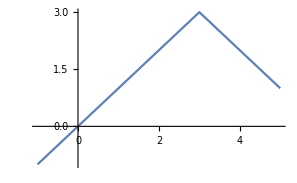

```mathematica
Plot[3-Abs[x-3],{x,-1,5}]
```

## 10.- Para aproximar las soluciones real de la ecuación x^3+x+1=0, considerar la función f(x) = x^3+x+1. ¿Es continua? ¿Es derivable? Evaluarla en -1 y 1. ¿Cuantas raíces tiene la ecuación? Aplicar el método de bisección 3 veces partiendo del intervalo [-1,1]. Octubre 22, octubre 21, enero 18

Solución:
La función f es continua en toda la recta real pues es un polinomio. También es derivable, pues es un polinomio. 
	f(-1)=-1-1+1=-1
	f(1)=1+1+1=3
Como el signo de la función f en -1 y en 1 son opuestos (siendo f continua; Teorema de Bolzano), la función se anula en algún punto entre -1 y 1. Por tanto, la ecuación tiene al menos una raíz. Para saber si tiene más, estudiamos la derivada de la función.
	f ’(x) = 3 x^2+1 
Vemos que la derivada de la función es siempre mayor que cero, la función es siempre estrictamente creciente y no puede tener más de un cero. Por tanto, hay una única solución de la ecuación y está entre -1 y 1.

Aplicamos ahora el método de bisección. Partimos del intervalo [-1,1] donde la función, que es continua, presenta cambio de signo y tiene por tanto una raíz.
	a_0= -1, b_0= 1, m_0= (a_0+b_0)/2= 0, f(a_0)=-1, f(b_0)=3, f(m_0)=1
Como en el punto medio la función tiene el mismo signo que en el extremo de la derecha reducimos el intervalo por esa parte
	a_1= -1, b_1= 0, m_1= (a_1+b_1)/2= -1/2, f(a_1)=-1, f(b_1)=1, f(m_1)=(-1/2)^3+(-1/2)+1=(-1/8)-(1/2)+1>0

Como en el punto medio la función tiene el mismo signo que en el extremo de la derecha reducimos el intervalo por esa parte
	a_2= -1, b_2= -1/2, m_2= (a_2+b_2)/2= -3/4, f(a_2)=-1, f(b_2)>0, f(m_2)=(-3/4)^3+(-3/4)+1=(-27/64)-(3/4)+1= (-27/64)-(48/64)+1=(-75/64)+1<0.
Como en el punto medio la función tiene el mismo signo que en el extremo de la izquierda, reducimos el intervalo por esa parte.
Tras tres pasos por el método de bisección hemos llegado a que la solución de la ecuación está en el intervalo [-3/4,-1/2].

## 4.- Calcular los máximos y mínimos absolutos de la función f(x) =|x^2-1| en [-1, 3]. Julio 22

Solución:
La función f es una función continua (por ser composición de funciones continuas, primero un polinomio y luego el valor absoluto) y el dominio es un intervalo cerrado y acotado. Por tanto, el teorema de Weierstrass asegura que existe máximo y mínimo absolutos.
Para encontrarlos debemos estudiar los extremos del intervalo, los puntos con derivada 0 del interior del intervalo, y los puntos donde no exista derivada de la función.
La función valor absoluto es derivable en todo punto, excepto en el 0. Veamos cuando x^2-1 es cero.
x^2-1 = 0 ⟹ x = ±1. Además, x^2-1 es mayor que cero cuando x es menor que -1 o mayor que 1. Por tanto
f(x)=Piecewise[{{x^2-1, si x <-1 ó x >1}, {1-x^2, si -1≤x ≤1}}]
La derivada es 2x o -2x, según el intervalo, y que solo se anularía en x=0 .
Por tanto debemos estudiar el valor de f en los extremos (x=-1, x=3), en los puntos con derivada cero (x=0) y los puntos del interior sin derivada (x=1).
Evaluando f(-1)=0, f(0)=1, f(1)=0, f(3)=8.
El valor máximo de f es 8 que se alcanza en el punto x=3, el valor mínimo de f es 0, que se alcanza en los puntos x=-1 y x=1.

## 4.- Calcular los máximos y mínimos absolutos de la función f(x) =x^3-3 x^2+2 en el intervalo [1, 3]. Enero 22

Solución:
La función f(x) es una función continua por ser un polinomio (también es derivable por la misma razón). Al ser una función continua en un intervalo cerrado y acotado, el [1, 3], tiene máximo y mínimo absolutos.

Los máximos y mínimos absolutos se encuentran estudiando tres tipos de puntos:
a) Los extremos del intervalo. En este caso, x=1 y x=3.
b) Los puntos del interior del intervalo con derivada cero.
f’(x)= 3 x^2-6x
Calculamos cuándo 3 x^2-6x=0, y obtenemos 3 x^2-6x = 3x(x-2) =0. Será cierto cuando x=0 o x=2. El punto x=0, no está en el intervalo. Por tanto, solo consideramos x=2.
El único punto donde se anula la derivada en el intervalo es el punto x=2.
c) Los puntos donde no existe derivada. En este caso, la derivada existe en todos los puntos.

Basta ahora evaluar la función en los puntos que hemos encontrado:
	f(1)= 1^3-3*1^2+2= 0, 
	f(2)= 2^3-3*2^2+2= 8-12+2 = -2 , 
	f(3)= 3^3-3*3^2+2= 27-27+2=2

El valor máximo de la función es 2, que se alcanza en el punto x=3. El valor mínimo de la función es -2 que se alcanza en el punto x=2.
Si dibujamos la gráfica con el Mathematica vemos lo que ocurre con la función.

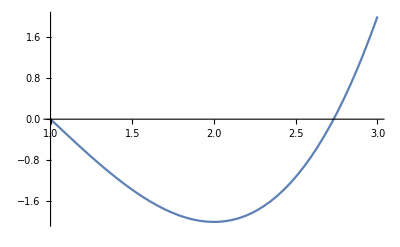

```mathematica
Plot[x^3-3 x^2+2,{x,1,3}]
```

## 4.- Calcular los máximos y mínimos absolutos de la función f(x) =|x^2-4| en el intervalo [-2,3]. Enero 21

Solución:
La función f(x) es una función continua por ser composición de funciones continuas, la función polinómica x^2-4 y la función valor absoluto. Al ser una función continua en un intervalo cerrado y acotado, el [-2,3], tiene máximo y mínimo absolutos.
Los máximos y mínimos absolutos se encuentran estudiando tres tipos de puntos:
a) Los extremos del intervalo. En este caso x=-2 y x=3.
b) Los puntos del interior del intervalo con derivada cero.
f(x)=Piecewise[{{x^2-4,, cuando x^2-4≥ 0}, {-(x^2-4),, cuando x^2-4≤ 0}}] 
Calculamos cuándo x^2-4=0, y obtenemos x=±2. Si x>2 o x<-2, x^2-4>0. En cambio, si -2<x<2, x^2-4<0. Por tanto,
f(x)=Piecewise[{{x^2-4,, si 2≤ x ≤ 3}, {-(x^2-4),, si -2≤x≤2}}] ⟹ f ‘(x)=Piecewise[{{2x,, si 2< x ≤ 3}, {-2x,, si -2≤x<2}}]
El único punto donde se anula la derivada es el punto x=0.
c) Los puntos donde no existe derivada. En este caso, en el punto x=2, que es donde cambia la definición de la función, pasando del polinomio -2x al polinomio 2x.
Basta ahora evaluar la función en los puntos que hemos encontrado en cada uno de los tipos de puntos.
f(-2)=|(-2)^2-4|=0, f(0)=|0^2-4|=4, f(2)=|2^2-4|=0, f(3)=|3^2-4|=5.
El valor máximo de la función es 5, que se alcanza en el punto x=3. El valor mínimo de la función es 0 que se alcanza en dos puntos, el punto x=-2 y el punto x=2.

Si dibujamos la gráfica con el Mathematica, obtenemos:

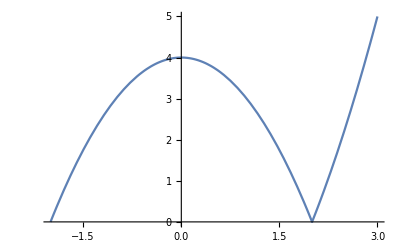

```mathematica
Plot[Abs[x^2-4],{x,-2,3}]
```

## 5.- Calcular el máximo y mínimo absolutos de la función f(x)=x^4-2 x^2 con x en el intervalo [-1/2, 2]. Enero 20

Solución:
Dado que es una función continua y derivable en un intervalo cerrado y acotado, tendrá máximo y mínimo absolutos, que alcanzará en los extremos del intervalo o en puntos con derivada cero (pues no hay puntos donde no exista la derivada).
	f’(x)= 4x^3 - 4 x =4x(x^2-1). 
La derivada se anula en 0 y 1 (también se anularía en -1, pero este punto no está en el intervalo).

Ahora, basta evaluar en los puntos de derivada 0 y en los extremos; 
	f(-1/2)= -7/16, 
	f(0)=0 ,
	f(1)=-1 ,
	f(2)=8. 
Por tanto el mínimo es -1, que se alcanza en el punto 1, y el máximo es 8, que se alcanza en el punto 2.

## 5.- Cuántas soluciones tiene la ecuación x^5+2x^3+3x+4=0. Enero 19

Solución:
La función f(x)=x^5+2x^3+3x+4 es una función continua y derivable en toda la recta real.
En x=-1, f(-1)=-2, en x=0, f(0)=4.
Por el teorema de Bolzano, hay un valor entre -1 y 0 donde f se anula, por tanto hay una solución de la ecuación. 
Para ver si hay más, consideramos la derivada de la función, f ’(x)= 5 x^4+6x^2+3. Como f’(x) es siempre mayor que cero, la función es estrictamente creciente, por tanto no puede anularse en dos puntos y la ecuación tiene sólo una solución. 

Si en dos puntos de ℝ la función valiese igual, por ejemplo 0, el Teorema de Rolle obligaría a que la derivada se anulase en un punto intermedio. Como la derivada no se anula, la función no puede valer 0 en dos puntos distintos.

## 6.- Calcular el máximo y mínimo absolutos de la función f(x)=|4-x^2|con x en [-3,1]. Enero 2018

Solución:
La función f(x) es continua (por ser diferencia y composición de funciones continuas) y en el intervalo [-3,1] (cerrado y acotado) tiene máximo y mínimo absolutos (Teorema de Weierstrass). Para calcular el máximo y el mínimo absolutos calculamos los puntos que son candidatos: extremos del intervalo, puntos donde se anula la derivada, puntos donde la función no sea derivable.

f(x)=|4-x^2|=Piecewise[{{x^2-4,, cuando 4-x^2≤0⟺4 ⩽x^2⟺x≤-2 ó 2⩽x (en este caso,-3≤x≤-2)}, {4-x^2,, cuando4-x^2≥0⟺4 ≥x^2⟺-2≤x≤2 (en este caso,-2≤x≤1)}}] 

La derivada f ’(x)=
f ’(x)=Piecewise[{{2x,, cuando -3≤x<-2)}, {-2x,, cuando-2<x≤1)}}]

En el punto -2, la función no es derivable.

	1) Extremos: -3, 1.
	2) Puntos con derivada cero: 0.
	3) Puntos donde f no es derivable: -2.

Ahora evaluamos f en esos puntos
f(-3)= |4-(-3)^2|=5, f(1)=|4-1^2|=3, f(0)=|4-0^2|=4, f(-2)=|4-(-2)^2|=0.
Por tanto, el máximo está en el punto -3, donde la función vale 5 y el mínimo está en el punto -2, donde la función vale 0.

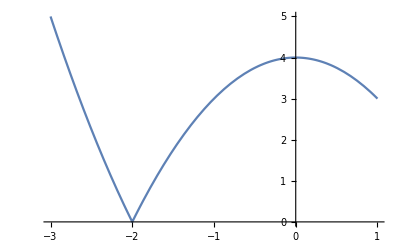

```mathematica
Plot[Abs[4-x^2],{x,-3,1}]
```

## Problemas de examen. Tema 6. Integrales

## 1.- Calcular el área de la superficie obtenida al girar la gráfica de la función f(x)= √(1+x) - 1 con x en [0,2] alrededor del eje horizontal. -Graphics3D- Superficie (4 cifras decimales): Enero 19. Aula de Informática

Solución:
Siguiendo lo estudiado en prácticas de Integrales definidas y aplicaciones, el área se obtiene calculando la integral ∫_a^b 2π f(x)√(1+f'(x)^2)ⅆx

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:=√(1+x)-1
```

```mathematica
∫_0^2 (2 π f[x] √(1+f'[x]^2) )ⅆx
```

1/6 π (√5+13 √13-6 √39+3 ArcSinh[2]-3 ArcSinh[2 √3])

```mathematica
N[%]
```

5.28925

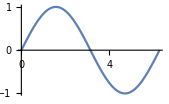
## 1.- Calcular la longitud de la gráfica de la función f(x) = sen x, con x en [0,2π] . -Graphics- Longitud (4 cifras decimales): Enero 19. Aula de Informática

Solución:
Siguiendo la Práctica de Integrales definidas y aplicaciones, la longitud se obtiene calculando la integral ∫_0^(2π) √(1+(f' [x])^2)ⅆx:

```mathematica
f[x_]:=Sin[x]
```

```mathematica
∫_0^(2π) √(1+(f' [x])^2)ⅆx
```

4 √2 EllipticE[1/2]

```mathematica
N[%]
```

7.6404

## 1.- Calcular el volumen obtenido al girar la gráfica de la función f(x)= 4-2x, con x en [0,2] alrededor del eje vertical y limitado por el plano horizontal. Volumen: -Graphics3D- Enero 19. Aula de Informática

Solución: 
Siguiendo la práctica de Integrales definidas y aplicaciones, el volumen se obtiene calculando la integral

```mathematica
∫_0^2 (2 π x  (4-2x))ⅆx
```

(16 π)/3

```mathematica
N[%]
```

16.7552

También podría razonarse que como el cuerpo obtenido es un cono, su volumen es 1/3 del área de la base (π por el radio al cuadrado) por la altura: 
1/3 (π 2^2)*4= 16 π/3.

## Sea tu DNI: AB.CDE.FGH, M = MÁXIMO {A, B, C, D, E, F, G, H} = ___, N = MIN {A, B, C, D, E, F, G, H, I}= ____ 1.- Calcular el volumen obtenido al girar la gráfica de la función f(x)= G+2+ sen (πx) con x en [N,M] alrededor del eje vertical y limitado por el plano horizontal. Volumen: -Graphics3D- Julio 18. Aula de Informática

Solución:
Siguiendo lo explicado en la Práctica sobre aplicaciones de las integrales definidas, tenemos

```mathematica
∫_n^m 2 π x(g+2+Sin[Pi x])ⅆx//Simplify
```

2 m^2 π+g m^2 π-2 n^2 π-g n^2 π+(2 (-m π Cos[m π]+n π Cos[n π]+Sin[m π]-Sin[n π]))/π

## 1.- Calcular el volumen obtenido al girar la gráfica de la función f(x)= 2+ sen (π x) con x en [0,3] alrededor del eje horizontal. -Graphics3D- Volumen: Enero 18. Aula de informática

Solución:
Siguiendo la Práctica de Integrales Definidas-Aplicaciones vemos que el volumen obtenido al girar respecto al eje horizontal OX es la integral ∫_a^b π f^2(x)ⅆx. En este caso,

```mathematica
∫_0^3 π (2+Sin[π x])^2 ⅆx
```

8+(27 π)/2

```mathematica
N[%]
```

50.4115

## Problemas de examen. Tema 7. Series.

## 5.- Calcular la suma de la serie ∑_(n=1)^∞ ((2^n + 3^n)/5^n). Julio 23

Solución: 
Se trata de una serie cuyos elementos son cocientes de expresiones que tienden a infinito. Podríamos escribir la serie de otra forma:

∑_(n=1)^∞ ((2^n +  3^n)/5^n)=∑_(n=1)^∞ (2^n/5^n+3^n/5^n)= ∑_(n=1)^∞ ((2/5)^n+(3/5)^n) = ∑_(n=1)^∞ (2/5)^n + ∑_(n=1)^∞ (3/5)^n

Se trataría de la suma de dos series que son progresiones geométricas de razón menor que uno. Como las dos pueden sumarse, la suma también podrá sumarse.

S= (2/5)^1 + (2/5)^2 + (2/5)^3+ (2/5)^4+ ....
2/5S= (2/5)^2 + (2/5)^3 + (2/5)^4+ (2/5)^5+ ....
Restando,
S- 2/5S = 3/5S = 2/5. Luego S=2/3
T= (3/5)^1 + (3/5)^2 + (3/5)^3+ (3/5)^4+ ....
3/5T= (3/5)^2 + (3/5)^3 + (3/5)^4+ (3/5)^5+ ....
Restando,
T- 3/5T = 2/5T = 3/5. Luego T=3/2
La serie suma 2/3 + 3/2 = 13/6

Con el Mathematica:

```mathematica
∑_(n=1)^∞ ((2^n+3^n)/5^n)
```

13/6

## 5.- Calcular la suma de la serie ∑_(n=1)^∞ (1/n-1/(n+3)). Enero 23

Solución: 
Se trataría de una serie de tipo racional (cociente de polinomios), aunque en este caso, la fracción está ya descompuesta y nos ahorramos esa tarea. 

Para estudiar la convergencia calculemos las sumas parciales.	
Llamando S_N a la suma parcial de la serie, tenemos que 
		S_N=(1/1-1/4)+(1/2-1/5)+(1/3-1/6)+(1/4-1/7)+(1/5-1/8)+...+(1/(N-3)-1/N)+(1/(N-2)-1/(N+1))+(1/(N-1)-1/(N+2))+(1/N-1/(N+3)) = 1/1+1/2+ 1/3 -1/(N+1)-1/(N+2)-1/(N+3) = 11/6-1/(N+1)-1/(N+2)-1/(N+3)
Observamos que en el cuarto sumando aparece 1/4 que se anularía con -1/4 del primer sumando, igualmente 1/5 aparece en el quinto sumando que se anularía con el -1/5 del segundo sumando, y así sucesivamente nos encontramos términos que se anulan. Tras simplificar, quedarían los tres primeros sumandos positivos y los tres últimos sumandos negativos.

Obtenido S_N= 1/1+1/2+ 1/3 -1/(N+1)-1/(N+2)-1/(N+3) = 11/6-1/(N+1)-1/(N+2)-1/(N+3) →  11/6. La suma de la serie será  11/6.
Con el Mathematica:

```mathematica
∑_(n=1)^∞ (1/n-1/(n+3))
```

11/6

## 4.- Estudiar la convergencia de la serie ∑_(n=1)^∞ ((2n)!)/(1*3*5*...*(2n-1)). Octubre 22, Octubre 21

Solución:
Observamos que cada sumando es un producto de términos que aumentan al aumentar n.  El criterio del cociente parece adecuado para este tipo de serie.

Llamamos a(n)= ((2n)!)/(1*3*5*...*(2n-1)) y estudiamos el cociente (a(n+1))/(a(n)) = (((2(n+1))!)/(1*3*5*...*(2(n+1)-1)))/(((2n)!)/(1*3*5*...*(2n-1))) = (((2n+2)!)/(1*3*5*...*(2n+1)))/(((2n)!)/(1*3*5*...*(2n-1))) = ((2n+2)(2n+1))/(2n+1)= (2n+2)  ⟶ ∞ > 1
Como tiende a infinito, mayor que 1, siendo una serie de términos positivos, llegamos a la conclusión que la serie no converge.

También podemos observar que los sumandos de la serie son mayores que uno, por tanto no convergen a cero y la serie no se puede sumar.
a(1)= ((2*1)!)/1=2
a(2)= ((2*2)!)/(1*3)=(1*2*3*4)/(1*3)=2*4=8
a(3)= ((2*3)!)/(1*3*5)=(1*2*3*4*5*6)/(1*3*5)=2*4*6=48
a(4)= ((2*4)!)/(1*3*5*7)=(1*2*3*4*5*6*7*8)/(1*3*5*7)=2*4*6*8=392
En el numerador están multiplicándose todos los números desde el 1 al 2n. En el denominador están solo los impares entre el 1 y 2n. Por tanto, el cociente resulta ser el producto de los pares entre el 2 y 2n, cantidades que no convergen a cero.
Es condición necesaria, aunque no suficiente, para que una serie pueda sumarse que el término tienda a cero. Concluimos que esta serie no puede sumarse.

## 5.- Calcular la suma de la serie ∑_(n=5)^∞ 1/(n^2-5n+4). Octubre 22

Solución:
Se trata de una serie de tipo racional (cociente de polinomios). Además, el grado del denominador es 2 más que el numerador. Por tanto, la serie se puede sumar. Para calcula la suma descomponemos la fracción 4/(n^2-5n+4) en fracciones simples. 
Para ello buscamos las raíces del denominador n^2-5n+4=0, n=1,4.
1/(n^2-5n+4)=A/(n-4)+B/(n-1)= (A(n-1)+B(n-4))/(n^2-5n+4)⟹1=A(n-1)+B(n-4). Si n=1, 1=A(1-1)+B(1-4)=-3B, por tanto B=-1/3. Si n=4, 1=A(4-1)+B(4-4)=3A, por tanto A=1/3.

De esta forma, 1/(n^2-5n+4)=(1/3)/(n-4)-(1/3)/(n-1).
La suma parcial S_N = ∑_(n=5)^N 1/(n^2-5n+4)= ∑_(n=5)^N ((1/3)/(n-4)-(1/3)/(n-1))=((1/3)/(5-4)-(1/3)/(5-1))+((1/3)/(6-4)-(1/3)/(6-1))+((1/3)/(7-4)-(1/3)/(7-1))+((1/3)/(8-4)-(1/3)/(8-1))+..+((1/3)/(N-1-4)-(1/3)/(N-1-1)).+((1/3)/(N-4)-(1/3)/(N-1)) =((1/3)/1-(1/3)/4)+((1/3)/2-(1/3)/5)+((1/3)/3-(1/3)/6)+((1/3)/4-(1/3)/7)+...+((1/3)/(N-5)-(1/3)/(N-2))+((1/3)/(N-4)-(1/3)/(N-1)) =(Simplificando los términos que suman y restan)= (1/3)/1+(1/3)/2+(1/3)/3- (1/3)/(N-3)- (1/3)/(N-2)-(1/3)/(N-1)⟶  (1/3)/1+(1/3)/2+(1/3)/3 = (11/3)/6= 11/18.
Por tanto, la suma de la serie  ∑_(n=5)^∞ 1/(n^2-5n+4)= 11/18.
Con el Mathematica,

```mathematica
Sum[1/(n^2-5n+4),{n,5,Infinity}]
```

11/18

## 5.- Expresar el número 12’345454545... como cociente de dos números enteros. Julio 22

Llamando x=12’345454545... 
Tenemos 10 x = 123’45454545... 
También 1000x = 12345’454545...
Restando, 1000x - 10x = 12345-123. Por tanto, 990 x = 12222, x=12222/990.  Si queremos simplificar, que no es necesario, dividimos numerador y denominador por 2 y por 9. 12222/990 = 1358/110 = 679/55.

Otra forma sería escribir el número como una suma con una serie geométrica.

12’3454545... = 12 +  3/10+ ∑_(n=1)^∞ 45/(10*100^n) = 120/10 +  3/10+45/10 ∑_(n=1)^∞ 1/100^n = 123/10 +45/10 (1/100)/(1-1/100) = 123/10 +45/10 1/(100-1) = 123/10 +45/10 1/99 = 123/10 +45/990 = 123/10 +5/110 = 123/10 +1/22 = (123*22+10)/220 =  2716/220= 2716/220 = 679/55

## 6.- Estudiar la convergencia de la serie ∑_(n=1)^∞ (n!n!)/((2n)!) . Julio 22

Solución:
Observamos que cada sumando es un producto de términos que aumentan al aumentar n.  El criterio del cociente parece adecuado para este tipo de serie.

Llamamos a(n)= (n!n!)/((2n)!) y estudiamos el cociente (a(n+1))/(a(n)) = (((n+1)!(n+1)!)/((2(n+1))!))/((n!n!)/((2n)!)) = (((n+1)!(n+1)!)/((2n+2)!))/((n!n!)/((2n)!)) = (((n+1)!(n+1)! (2n)!)/((2n+2)!))/((n!n! (2n)!)/((2n)!)) = (((n+1)!(n+1)!)/((2n+1)(2n+2)))/(n!n!)= ((n+1)(n+1))/((2n+1)(2n+2))= (n+1)/((2n+1)*2) = (n+1)/(4n+2) ⟶ 1/4 < 1
Como tiende a un valor menor que 1, siendo una serie de términos positivos, llegamos a la conclusión que la serie converge.

## 5.- Calcular la suma de la serie ∑_(n=1)^∞ (2n+1)/3^n. Enero 22

Solución: 
Para estudiar la convergencia podríamos utilizar el criterio del cociente. 
		((2(n+1)+1)/3^(n+1))/((2n+1)/3^n)=((2n+3)/3^(n+1))/((2n+1)/3^n) = ((2n+3)/3)/(2n+1)=1/3(2n+3)/(2n+1) ⟶ 1/3<1, por tanto converge.
Llamando S_N a la suma parcial de la serie, tenemos que 
		S_N=3/3+5/9+7/27+9/81+11/243+...+ (2N+1)/3^N
		S_N/3=3/9+5/27+7/81+9/243+...+(2N-1)/3^N+ (2N+1)/3^(N+1)
Restando estas dos expresiones, llegamos a 
		(2 S_N)/3=3/3+2/9+2/27+2/81+2/243+...- (2N+1)/3^(N+1)
Por tanto, multiplicando por 1/3,
		(2 S_N)/9=3/9+2/27+2/81+2/243+2/729+...+2/3^(N+1)- (2N+1)/3^(N+2)
Restando estas dos últimas igualdades,
	(2 S_N)/3 - (2 S_N)/9= (2/3- 2/9) S_N =  4/9 S_N = 3/3+2/9-3/9- (2N+1)/3^(N+1) - 2/3^(N+1) + (2N+1)/3^(N+2)= 8/9- (2N+3)/3^(N+1)  + (2N+1)/3^(N+2)→8/9
Entonces,  4/9 S_N →8/9, y   9/4(4/9 S_N) →9/4(8/9)=2. La suma de la serie será 2.

Con el Mathematica:

```mathematica
∑_(n=1)^∞ (2n+1)/3^n
```

2

## 5.- Calcular la suma de la serie ∑_(n=4)^∞ 1/(n^2-4n+3). Octubre 21

Solución:
Se trata de una serie de tipo racional (cociente de polinomios). Además, el grado del denominador es 2 más que el numerador. Por tanto, la serie se puede sumar. Para calcula la suma descomponemos la fracción 4/(n^2-4n+3) en fracciones simples. 
Para ello buscamos las raíces del denominador n^2-4n+3=0, n=1,3.
1/(n^2-4n+3)=A/(n-3)+B/(n-1)= (A(n-1)+B(n-3))/(n^2-4n+3)⟹1=A(n-1)+B(n-3). Si n=1, 1=A(1-1)+B(1-3)=-2B, por tanto B=-1/2. Si n=3, 1=A(3-1)+B(3-3)=2A, por tanto A=1/2.

De esta forma, 1/(n^2-4n+3)=(1/2)/(n-3)-(1/2)/(n-1).
La suma parcial S_N = ∑_(n=4)^N 1/(n^2-4n+3)= ∑_(n=4)^N ((1/2)/(n-3)-(1/2)/(n-1))=((1/2)/(4-3)-(1/2)/(4-1))+((1/2)/(5-3)-(1/2)/(5-1))+((1/2)/(6-3)-(1/2)/(6-1))+((1/2)/(7-3)-(1/2)/(7-1))+..+((1/2)/(N-1-3)-(1/2)/(N-1-1)).+((1/2)/(N-3)-(1/2)/(N-1)) =((1/2)/1-(1/2)/3)+((1/2)/2-(1/2)/4)+((1/2)/3-(1/2)/5)+((1/2)/4-(1/2)/6)+...+((1/2)/(N-4)-(1/2)/(N-2))+((1/2)/(N-3)-(1/2)/(N-1)) =(Simplificando los términos que suman y restan)= (1/2)/1+(1/2)/2- (1/2)/(N-2)-(1/2)/(N-1)⟶  (1/2)/1+(1/2)/2 = (3/2)/2= 3/4.
Por tanto, la suma de la serie  ∑_(n=4)^∞ 1/(n^2-4n+3)= 3/4.
Con el Mathematica,

```mathematica
Sum[1/(n^2-4n+3),{n,4,Infinity}]
```

3/4

## 5.- Calcular la suma de la serie ∑_(n=5)^∞ 4/(n^2-1). Junio 21

Solución:
Se trata de una serie de tipo racional (cociente de polinomios). Además, el grado del denominador es 2 más que el numerador. Por tanto, la serie se puede sumar. Para calcula la suma descomponemos la fracción 4/(n^2-1) en fracciones simples. 
Para ello buscamos las raíces del denominador n^2-1=0, n=±1.
4/(n^2-1)=A/(n-1)+B/(n+1)= (A(n+1)+B(n-1))/(n^2-1)⟹4=A(n+1)+B(n-1). Si n=1, 4=A(1+1)+B(1-1)=2A, por tanto A=2. Si n=-1, 4=A(-1+1)+B(-1-1)=-2B, por tanto B=-2.

De esta forma, 4/(n^2-1)=2/(n-1)-2/(n+1). La suma parcial S_N = ∑_(n=5)^N 4/(n^2-1)= ∑_(n=5)^N (2/(n-1)-2/(n+1))=(2/(5-1)-2/(5+1))+(2/(6-1)-2/(6+1))+(2/(7-1)-2/(7+1))+(2/(8-1)-2/(8+1))+..+(2/(N-1-1)-2/(N-1+1)).+(2/(N-1)-2/(N+1)) =(2/4-2/6)+(2/5-2/7)+(2/6-2/8)+(2/7-2/9)+...+(2/(N-2)-2/N)+(2/(N-1)-2/(N+1)) =(Simplificando los términos que suman y restan)= 2/4+2/5- 2/N-2/(N+1)⟶ 2/4+2/5 = 18/20= 9/10.
Por tanto, la suma de la serie  ∑_(n=5)^∞ 4/(n^2-1)= 9/10.

```mathematica
Sum[4/(n^2-1),{n,5,Infinity}]
```

9/10

## 5.- Calcular la suma de la serie ∑_(n=3)^∞ 2/(n^2-n). Febrero 21

Solución:
Se trata de una serie de tipo racional (cociente de polinomios). Además, el grado del denominador es 2 más que el numerador. Por tanto, la serie se puede sumar. Para calcula la suma descomponemos la fracción 2/(n^2-n) en fracciones simples. 
Para ello buscamos las raíces del denominador n^2-n=n(n-1)=0, n=0,1.
2/(n^2-n)=A/(n-1)+B/n= (An+B(n-1))/(n^2-n)⟹2=An+B(n-1). Si n=1, 2=A*1+B(1-1)=A, por tanto A=2. Si n=0, 2=A*0+B(0-1)=-B, por tanto B=-2.

De esta forma, 2/(n^2-n)=2/(n-1)-2/n. La suma parcial S_N = ∑_(n=3)^N 2/(n^2-n)= ∑_(n=3)^N (2/(n-1)-2/n)=(2/(3-1)-2/3)+(2/(4-1)-2/4)+(2/(5-1)-2/5)+(2/(6-1)-2/6)+..+(2/(N-1-1)-2/(N-1)).+(2/(N-1)-2/N) =(2/2-2/3)+(2/3-2/4)+(2/4-2/5)+(2/5-2/6)+...+(2/(N-2)-2/(N-1))+(2/(N-1)-2/N) =(Simplificando los términos que suman y restan)= 2/2 - 2/N⟶ 2/2 = 1
Por tanto, la suma de la serie  ∑_(n=5)^∞ 2/(n^2-n)= 1 .
Con el Mathematica

```mathematica
Sum[2/(n^2-n),{n,3,Infinity}]
```

1

## 5.- Calcular la suma de la serie ∑_(n=3)^∞ 2/(n^2-1). Enero 21

Solución:
Se trata de una serie de tipo racional (cociente de polinomios). Además, el grado del denominador es 2 más que el numerador. Por tanto, la serie se puede sumar. Para calcula la suma descomponemos la fracción 2/(n^2-1) en fracciones simples. 
Para ello buscamos las raíces del denominador n^2-1=0, n=±1.
2/(n^2-1)=A/(n-1)+B/(n+1)= (A(n+1)+B(n-1))/(n^2-1)⟹2=A(n+1)+B(n-1). Si n=1, 2=A(1+1)+B(1-1)=2A, por tanto A=1. Si n=-1, 2=A(-1+1)+B(-1-1)=2B, por tanto B=-1.

De esta forma, 2/(n^2-1)=1/(n-1)-1/(n+1). La suma parcial S_N = ∑_(n=3)^N 2/(n^2-1)= ∑_(n=3)^N (1/(n-1)-1/(n+1))=(1/(3-1)-1/(3+1))+(1/(4-1)-1/(4+1))+(1/(5-1)-1/(5+1))+(1/(6-1)-1/(6+1))+..+(1/(N-1-1)-1/(N-1+1)).+(1/(N-1)-1/(N+1)) =(1/2-1/4)+(1/3-1/5)+(1/4-1/6)+(1/5-1/7)+...+(1/(N-2)-1/N)+(1/(N-1)-1/(N+1)) =(Simplificando los términos que suman y restan)= 1/2+1/3- 1/N-1/(N+1)⟶ 1/2+1/3 = 5/6.
Por tanto, la suma de la serie  ∑_(n=3)^∞ 2/(n^2-1)= 5/6.

## 4.- Calcular la suma de la serie ∑_(n=1)^∞ (2-n)/(n^3+3 n^2+2n). Enero 20

Solución:
Dado que la diferencia de grados entre numerador y denominador es de 2 a favor del denominador, la serie converge. Para sumar, descomponemos la fracción hallando las raíces del denominador,

 (2-n)/(n^3+3 n^2+2n) = (2-n)/(n(n^2+3n+2))= (2-n)/(n(n+1)(n+2))=1/n-3/(n+1)+2/(n+2)
S_n=(1/1-3/2+2/3)+(1/2-3/3+2/4)+(1/3-3/4+2/5)+....+1/n-3/(n+1)+2/(n+2)= 1/1-3/2+1/2+2/3-3/3+1/3+....+2/(n+1)-3/(n+1)+2/(n+2)= 2/(n+1)-3/(n+1)+2/(n+2)⟶0

## 4.- Estudiar la convergencia y suma de la serie ∑_(n=1)^∞ n^2/2^n. Enero 19

Solución: 
Para estudiar la convergencia podríamos utilizar el criterio del cociente. ((n+1)^2/2^(n+1))/(n^2/2^n)=(n+1)^2/(2 n^2) ⟶ 1/2<1, por tanto converge.
Llamando S a la suma de la serie tenemos que 
		S=1/2+4/4+9/8+16/16+25/32+36/64+...
		S/2=1/4+4/8+9/16+16/32+25/64+36/128+...
Restando estas dos expresiones, llegamos a 
		S/2=1/2+3/4+5/8+7/16+9/32+11/64+13/128+...
Por tanto, multiplicando por 1/2,
		S/4=1/4+3/8+5/16+7/32+9/64+11/128+13/256+...
Restando estas dos últimas igualdades,
	S/4=1/2+2/4+2/8+2/16+2/32+2/64+2/128+2/256+...= 1/2+ 2 (1/4)/(1-1/2)= 1/2+  (1/2)/(1/2)= 3/2
Entonces, S=6.

## 4.- Calcular la suma de la serie ∑_(n=1)^∞ 2/(n^2+3n+ 2). Octubre 18

Solución:
Se trata de una serie de tipo racional (cociente de polinomios). Además, el grado del denominador es 2 más que el numerador. Por tanto, la serie se puede sumar. Para calcula la suma descomponemos la fracción 2/(n^2+3n+2) en fracciones simples. 
Para ello buscamos las raíces del denominador n^2+3n+2=0, n=-1,-2.
2/(n^2+3n+2)=A/(n+1)+B/(n+2)= (A(n+2)+B(n+1))/(n^2+3n+2)⟹2=A(n+2)+B(n+1). Si n=-1, 2=A(-1+2)+B(-1+1)=A, por tanto A=2. Si n=-2, 2=A(-2+2)+B(-2+1)=-B, por tanto B=-2.

De esta forma, 2/(n^2+3n+2)=2/(n+1)-2/(n+2). La suma parcial S_N = ∑_(n=1)^N 2/(n^2+3n+2)= ∑_(n=1)^N (2/(n+1)-2/(n+2))=(2/(1+1)-2/(1+2))+(2/(2+1)-2/(2+2))+(2/(3+1)-2/(3+2))+..+(2/(N-1+1)-2/(N-1+2)).+(2/(N+1)-2/(N+2)) =(2/2-2/3)+(2/3-2/4)+(2/4-2/5)+...+(2/(N-2)-2/(N-1))+(2/(N-1)-2/N) =(Simplificando los términos que suman y restan)= 2/2 - 2/N⟶ 2/2 = 1
Por tanto, la suma de la serie  ∑_(n=1)^∞ 2/(n^2+3n+2)= 1 .
Con el Mathematica

```mathematica
Sum[2/(n^2+3n+2),{n,1,Infinity}]
```

1

## 3.- Estudiar si la serie ∑_(n=1)^∞ (√(n + 3))/e^n es convergente o divergente. Octubre 18, Julio 18

Solución : 
Una posibilidad: 
∑_(n=1)^∞ 1/e^n es una serie que es la suma de una progresión geométrica de razón 1/e <1 y se puede sumar. 
La serie ∑_(n=1)^∞ (n + 3)/e^n sería una aritmético-geométrica con razón menor que 1 y por tanto se puede sumar.
Como √(n+3)< n+3,  la serie ∑_(n=1)^∞ (√(n + 3))/e^n converge pues lo hace ∑_(n=1)^∞ (n + 3)/e^n.

Otra forma:
Utilizando el criterio del cociente:
Llamamos a(n)= (√(n+3))/ⅇ^n y estudiamos el cociente (a(n+1))/(a(n)) = ((√((n+1)+3))/ⅇ^(n+1))/((√(n+3))/ⅇ^n) = ((√(n+4))/(ⅇ*ⅇ^n))/((√(n+3))/ⅇ^n) = ((√(n+4))/ⅇ)/(√(n+3))=((√(n+4))/ⅇ 1/(√(n+3)))/(√(n+3)1/(√(n+3)))=(√((n+4)/(n+3)))/ⅇ ⟶ 1/ⅇ < 1.
Por tanto, la serie se puede sumar.

## 4.- Calcular la suma de la serie ∑_(n=1)^∞ (2n)/(n^3+3 n^2+ 2n). Julio 18

Solución:
 ∑_(n=1)^∞ (2n)/(n^3+3 n^2+ 2n) =  ∑_(n=1)^∞ 2/(n^2+3n+ 2)
 Buscamos las raíces del denominador y descomponemos en fracciones simples.
	n^2+3n+2 = 0 ⟹ n= (-3±√(9-8))/2=  (-3±1)/2 = -1, -2
	2/(n^2+3n+2)= A/(n+1)+ B/(n+2)= (A(n+2)+B(n+1))/((n+1)(n+2))⟹ 2 = A(n+2)+B(n+1)
haciendo n=-1 y n=-2, obtenemos
		2=A
		2=-B
Por tanto,
		2/(n^2+3n+2)= 2/(n+1) - 2/(n+2)
		
Ahora calculamos las sumas parciales y el límite cuando n tiende a infinito.

s_n= a_1 + a_2 + a_3+... + a_(n-1)+ a_n = (2/(1+1) - 2/(1+2))+(2/(2+1) - 2/(2+2))+(2/(3+1) - 2/(3+2))+...+(2/(n-1+1) - 2/(n-1+2))+(2/(n+1) - 2/(n+2))
=
 (2/2 - 2/3)+(2/3 - 2/4)+(2/4 - 2/5)+...+(2/n - 2/(n+1))+(2/(n+1) - 2/(n+2))= (2/2 - 2/(n+2)) → 1.
 
 La sucesión de sumas parciales tiende a 1. Esta sería la suma de la serie.

## 4.- Estudiar la convergencia de la serie ∑_(n=1)^∞ (n!)/(1*3*5*...*(2n-1)). Enero 18

Solución:
En esta serie de términos positivos tenemos un cociente entre dos productos que dependen de n. Esta forma parece invitarnos a utilizar el criterio del cociente. Dividimos el término n+1 entre el término n.

					(((n+1)!)/(1*3*5*...*(2n-1)*(2n+1)))/((n!)/(1*3*5*...*(2n-1)))=((n+1)/(2n+1)) → 1/2 < 1
Por tanto, la serie es convergente.

Observación: Para escribir la serie anterior con el Mathematica no podemos poner “los puntos suspensivos”.

```mathematica
∑_(n=1)^∞ (n!)/(∏_(i=1)^n (2i-1))
```

(2+π)/2

## 5.- Calcular la suma de la serie ∑_(n=5)^∞ 1/(n^2-5n+6). Enero 18

Solución:
El término de la serie es una expresión racional con dos grados más en el denominador que en el numerador, por tanto se podrá sumar.
Buscamos las raíces del denominador y descomponemos en fracciones simples.
	n^2-5n+6 = 0 ⟹ n= (5±√(25-24))/2=  (5±1)/2 = 3, 2
	1/(n^2-5n+6)= A/(n-3)+ B/(n-2)= (A(n-2)+B(n-3))/((n-3)(n-2))⟹ 1 = A(n-2)+B(n-3)
haciendo n=3 y n=2, obtenemos
		1=A
		1=-B
Por tanto,
		1/(n^2-5n+6)= 1/(n-3) - 1/(n-2)
		
Ahora calculamos las sumas parciales y el límite cuando n tiende a infinito.

s_n= a_5 + a_6 + ... + a_n = (1/(5-3) - 1/(5-2))+(1/(6-3) - 1/(6-2))+(1/(7-3) - 1/(7-2))+...+(1/(n-1-3) - 1/(n-1-2))+(1/(n-3) - 1/(n-2))
=
 (1/2 - 1/3)+(1/3 - 1/4)+(1/4 - 1/5)+...+(1/(n-4) - 1/(n-3))+(1/(n-3) - 1/(n-2))= (1/2 - 1/(n-2)) → 1/2.
 
 La sucesión de sumas parciales tiende a 1/2. Esta sería la suma de la serie.

## Problemas de examen. Tema 8. Funciones de varias variables.

## 6.- Consideremos la figura formada por un rectángulo, de lados x (altura) y 2r (base), y un semicírculo de radio r. Si el perímetro de la figura resultante, L, está fijo, encontrar los valores de x y r para que el área sea máxima. Julio 23

Solución:
El área de la figura es x*2r+(π  r^2)/2. El perímetro es 2x+2r+π*r =L. Despejando x=(L-2r-π*r)/2 y sustituyendo en el área   x*2r+(π  r^2)/2 = (L-2r-π*r)r+(π  r^2)/2=  L*r-2 r^2-(π  r^2)/2 =A(r).
Como x y r no pueden ser negativos, 2x=L-r(2+π)≥0, luego r≤L/(2+π). Por tanto debemos buscar el máximo de A(r)=L*r-2 r^2-(π  r^2)/2  en el intervalo [0,L/(2+π)]. 
Es una función polinómica de grado dos con coeficiente líder negativo, es continua y derivable en el intervalo. Tendrá por tanto máximo y mínimo absoluto. 
A’(r)=L-4r-π  r = 0 ⟹ r=L/(4+π)
Evaluamos A en los extremos del intervalo y donde se anula la derivada:
A(0)=L*0-2*0^2-(π*0^2)/2=0
A(L/(4+π))= L*L/(4+π)-2(L/(4+π))^2-(π (L/(4+π))^2)/2 =L^2/(4+π)-(2 L^2)/(4+π)^2-(π L^2)/(2(4+π)^2)=L^2/(2(4+π))(2-4/(4+π)-π/(4+π))=L^2/(2(4+π))
A(L/(2+π))=L*L/(2+π)-2(L/(2+π))^2-(π (L/(2+π))^2)/2=L^2/(2+π)-(2 L^2)/(2+π)^2-(π L^2)/(2(2+π)^2)=L^2/(2(2+π))(2-4/(2+π)-π/(2+π))=L^2/(2(2+π))((4+2π-4-π)/(2+π))=L^2/(2(2+π))(π/(2+π)) 
El máximo se consigue en r=L/(4+π). El valor de x será x= (L-2r-π*r)/2 = (L-(2+π)*r)/2=(L-(2+π)*(L/(4+π)))/2=L/2(1-((2+π)/(4+π)))=L/2(2/(4+π))=L/(4+π)

(En este caso, considerando que la función A(r) es polinómica de grado dos y con coeficiente líder negativo, podríamos razonar que en todo ℝ tiene máximo absoluto y no tiene mínimo absoluto. Como A’(r) se anula en el punto  r=L/(4+π), tenemos que el máximo absoluto en toda la recta real se alcanza en ese punto. Dado que el punto r=L/(4+π) está en el intervalo que estamos estudiando, [0,L/(2+π)], (L/(4+π) es positivo y menor que L/(2+π)) ,podemos concluir que también es el máximo absoluto en dicho intervalo.)

Otra posibilidad es considerar la función área como función de dos variables, la restricción del perímetro y los multiplicadores de Lagrange.
H(x,r,λ)=2xr+(π  r^2)/2+λ(2x+2r+π*r -L)
∂_x H(x,r,λ)=0	⟹	2r +2λ=0	⟹	λ=-r
∂_r H(x,r,λ)=0	⟹	2x + rπ + λ(2+π)=0	⟹ (con λ=-r)	⟹ 2x + rπ + (-r)(2+π)=2x -2r =0	⟹	x=r
∂_λ H(x,r,λ)=0	⟹	2x+2r+π*r -L=0		⟹	(con x=r)	⟹	2x+2x+π*x -L=0	⟹	x= L/(4+π)
La solución de este sistema es x= L/(4+π), r=x= L/(4+π), λ=-r=- L/(4+π)

Por otra parte, tenemos que r y x no pueden ser negativos:
Si x=0, r =L/(2+π).
Si r=0, x=L/2
Evaluamos A(x,r)=2xr+(π  r^2)/2en los tres puntos (L/(4+π),L/(4+π)), (0,L/(2+π)), (L/2, 0)

A(x,r)=2xr+(π  r^2)/2
A(L/(4+π),L/(4+π))=2*(L/(4+π))*(L/(4+π))+(π  (L/(4+π))^2)/2=(2  L^2)/(4+π)^2+(π  L^2)/(2*(4+π)^2)= ((4+π)  L^2)/(2*(4+π)^2) = L^2/(2*(4+π))
A(0,L/(2+π))=2*0*(L/(2+π))+(π  (L/(2+π))^2)/2=(π  L^2)/(2*(2+π)^2)
A(L/2,0)=2*(L/2)*0+(π  0^2)/2=0

El mayor valor se alcanza en x=L/(4+π), r=L/(4+π). El valor máximo de A(x,r) es L^2/(2*(4+π)).

Para comparar los valores L^2/(2*(4+π)) y (π  L^2)/(2*(2+π)^2), dividimos ambos por π  L^2, y nos queda 1/(2*(4+π)*π) y 1/(2*(2+π)^2), o sea  1/(2*(4π+π^2)) y 1/(2*(4+4π+π^2)). Como el denominador de la segunda expresión es mayor, la fracción es menor. Por tanto, el mayor valor es el primero: L^2/(2*(4+π)).

## 7.- Calcular, si existe, el límite de la función f(x,y)= cos((x y (x+y))/(x^2+y^2)) en el punto (0,0). Julio 23

Solución:
La expresión que aparece en el coseno es un cociente donde tanto el numerador como el denominador se anulan en el punto (0,0).

En la expresión (x y (x+y))/(x^2+y^2) tendríamos un polinomio de grado 3 en el numerador y grado dos en el denominador. Podríamos pensar que el límite va a existir, más al ver el denominador, x^2+y^2, que al pasar a polares dejaría el módulo al cuadrado.

Cambiamos a coordenadas a polares.
x=r cos θ
y=r sin θ
		(r cos θ r sin θ (r cos θ+r sin θ))/((r cos θ)^2+(r sin θ)^2)=(r^3 cos θ  sin θ (cos θ+sin θ))/r^2=r cos θ  sin θ (cos θ+sin θ) ⟶ 0 (r tiende a cero y multiplica a una expresión acotada)
Como la función coseno es continua, f(x,y) ⟶ 1 cuando (x,y)⟶ (0,0).

Con el Mathematica podemos dibujar la gráfica.

```mathematica
Plot3D[Cos[x*y*(x+y)/(x^2+y^2)],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

## 8.- Calcular la integral de la función f(x,y)= x^2+y^2 , en el triángulo de vértices (0,1), (-1,0) y (2,0). Julio 23

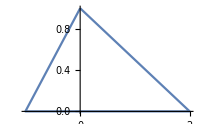
Solución:
La región está limitada por las rectas  y=x+1, y=0, y= 1-x/2.

-Graphics-
Observando la región, vemos que si consideramos la variación de la y, en el intervalo [0,1], (despejando x en las ecuaciones y=x+1, y=1-x/2) podemos dejar la x variando en [y-1, 2-2y]. Así, tenemos que calcular la integral doble: 
∫_0^1 (∫_(y-1)^(2-2y) x^2+y^2 ⅆx)ⅆy=∫_0^1 (x^3/3+xy^2|_(x=y-1)^(x=2-2y))ⅆy=∫_0^1 ((2-2y)^3/3+(2-2y)y^2-(y-1)^3/3-(y-1)y^2)ⅆy=∫_0^1 ((8-24y+24 y^2-8 y^3)/3+2 y^2-2 y^3-(y^3-3 y^2+3y-1)/3-(y^3-y^2))ⅆy = ∫_0^1 ((8-24y+24 y^2-8 y^3+6 y^2-6 y^3)/3-(y^3-3 y^2+3y-1+3 y^3-3 y^2)/3)ⅆy=∫_0^1 ((8-24y+24 y^2-8 y^3+6 y^2-6 y^3-y^3+3 y^2-3y+1-3 y^3+3 y^2)/3)ⅆy=∫_0^1 ((9-27y+36 y^2-18 y^3)/3)ⅆy=∫_0^1 (3-9y+12 y^2-6 y^3)ⅆy = 3y-(9 y^2)/2+4 y^3-6 y^4/4 |_(y=0)^(y=1) = 3-9/2+4-6/4 = (12-18+16-6)/4  =4/4=1

Con el Mathematica:

```mathematica
∫_0^1 (∫_(y-1)^(2-2y) (x^2+y^2)ⅆx)ⅆy
```

1

## 6.- Calcular la integral de la función f(x,y)= y en el semicírculo centrado en (0,0), de radio 1, con y positiva (es decir, x^2+y^2≤1, y≥0). Enero 23

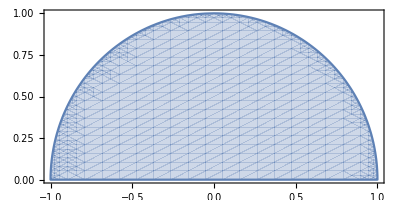
Solución:
La región está limitada por la circunferencia x^2+y^2=1 y la recta y=0.

-Graphics-
Observando la región, vemos que si consideramos la variación de la x, en el intervalo [-1,1], podemos dejar la y variando en [0, √(1-x^2)]. Así, tenemos que calcular la integral doble: 
∫_-1^1 (∫_0^(√(1-x^2)) yⅆy)ⅆx=∫_-1^1 (y^2/2)|_(y=0)^(y=√(1-x^2))ⅆx =  ∫_-1^1 ((1-x^2)/2-0)ⅆx =   ∫_-1^1 (1-x^2)/2ⅆx = (x/2-x^3/6)|_(x=-1)^(x=1)=(1/2-1^3/6)-(-1/2-(-1)^3/6)=(1/2-1/6)+1/2-1/6=1-1/3=2/3

Con el Mathematica:

```mathematica
∫_-1^1 (∫_0^(√(1-x^2)) yⅆy)ⅆx
```

2/3

## 7.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=3 y^3+x^2-9y+4x. Enero 23

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 2x+4 = 0 ⟹ x=-2
		∂_y f(x,y) = 9y^2-9 = 9(y^2-1)= 0 ⟹ y=1, y=-1
Los puntos donde se anulan las dos derivadas parciales son (-2,1), (-2,-1).
Para ver si es máximo, mínimo o punto de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(2 | 0
0 | 18y)|
Hessiano (-2,1) = |(2 | 0
0 | 18)|= 36 > 0 (máximo o mínimo relativo) (Como ∂_(x,x) f(-2,1)= 2 >0, será mínimo local)
Hessiano (-2,-1) = |(2 | 0
0 | -18)|= -36 < 0 (Punto de silla)

Como el hessiano en el punto (-2,-1) es negativo, habrá un punto de silla. Como el hessiano en el punto (-2,1) es positivo habrá un mínimo o un máximo relativo. Para saber si es máximo o mínimo vemos la derivada segunda en x (o en y) en ese punto. Como la derivada segunda es 2 >0, hay un mínimo relativo en ese punto.
Con el Mathematica podemos dibujar la gráfica.

```mathematica
Plot3D[3y^3+x^2-9y+4x,{x,-4,0},{y,-2,2}]
```

-Graphics3D-

## 8.- Calcular los extremos absolutos (máximos y mínimos) de la función f(x,y)=x-2y+7 en el conjunto de puntos que cumplen x^2+y^2≤4. Enero 23

Solución:
La función es polinómica y, por tanto, es continua y derivable. Los extremos pueden estar en el interior del círculo (x^2+y^2<4), o en el borde (en la circunferencia x^2+y^2=4).
Para encontrar los posibles puntos en el interior, hacemos derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 1 ⟹ No se anula nunca
		∂_y f(x,y) = -2 ⟹ No se anula nunca
Las derivadas parciales no se anulan en el interior del recinto.

Ahora hay que estudiar los posibles puntos en el borde del recinto; cuando x^2+y^2=4. Podemos buscar los posibles puntos utilizando la técnica de los Multiplicadores de Lagrange:
Consideramos F(x,y,t) = f(x,y) + t g(x,y), donde f(x,y)=x-2y+7, g(x,y)=x^2+y^2-4. Ahora hacemos derivadas parciales e igualamos a cero.
		∂_x F(x,y,t) = 1 + t(2x) =  0 
		∂_y F(x,y,t) = -2+t(2y) = 0
		∂_t F(x,y,t) = x^2+y^2-4 = 0
Despejando x de la primera ecuación, x=-1/(2t). Despejando y de la segunda ecuación, y=1/t. Sustituyendo estos valores en la tercera ecuación tenemos:
(-1/(2t))^2+(1/t)^2-4 = 0 ⟹ 1/(4 t^2)+(1/t^2)-4=0  ⟹ 5/(4 t^2)-4=0  ⟹ 5= 16 t^2 ⟹ t = ±√5/4.
(El caso t=0 no permitiría escribir x=-1/(2t), sin embargo, si t fuese 0, la primera ecuación quedaría como 1=0, que no tendría solución. Lo mismo sucedería en la segunda ecuación.)

Si  t = √5/4, x = -1/(2t) = -2/√5, y = 1/t = 4/√5. Un posible punto es (-2/√5, 4/√5).
Si  t = -√5/4, x = -1/(2t) = 2/√5, y = 1/t = -4/√5. Un posible punto es (2/√5, -4/√5).

Evaluamos la función f en esos puntos, 
	f(2/√5, -4/√5) = 2/√5 + 8/√5 + 7 = 10/√5 + 7 
	f(-2/√5, 4/√5) = -2/√5 - 8/√5 + 7 = -10/√5 + 7 

Por tanto, el máximo absoluto es 10/√5 + 7  y se alcanza en el punto (2/√5, -4/√5). El mínimo absoluto es -10/√5 + 7  y se alcanza en el punto (-2/√5, 4/√5)

Con el Mathematica dibujamos la gráfica:

```mathematica
Plot3D[Which[x^2+y^2<=4,x-2y+7],{x,-2,2},{y,-2,2},PlotPoints->50]
```

-Graphics3D-

## 7.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=(x^2-9)^2+ (y-1)^2. Octubre 22, Octubre 21

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 2 (x^2-9)*2x = 0 ⟹ x=0, 3, -3
		∂_y f(x,y) = 2(y-1) = 0 ⟹ y=1
Los puntos donde se anulan las dos derivadas parciales son (0,1), (3,1) y (-3,1).
Para ver si es máximo, mínimo o punto de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(12 x^2-36 | 0
0 | 2)|
Hessiano (0,1) = |(-36 | 0
0 | 2)|= -72 < 0 (Punto de silla)
Hessiano (3,1) = |(108-36 | 0
0 | 2)|= 144 > 0 (Máximo o mínimo local) Como ∂_(y,y) f(3,1)=2>0, se trata de un mínimo local.
Hessiano (-3,1) = |(108-36 | 0
0 | 2)|= 144 > 0 (Máximo o mínimo local) Como ∂_(y,y) f(-3,1)=2>0, se trata de un mínimo local.

Como el hessiano en el punto (0,1) es negativo, habrá un punto de silla. Como el hessiano en el punto (3,1) y (-3,1) es positivo habrá un mínimo o un máximo relativo. Para saber si es máximo o mínimo vemos la derivada segunda en x (o en y) en ese punto. Como la derivada segunda en y es 2 >0, hay un mínimo relativo en esos puntos.
Con el Mathematica podemos dibujar la gráfica.

```mathematica
Plot3D[(x^2-9)^2+(y-1)^2,{x,-4,4},{y,-1,3}]
```

-Graphics3D-

## 8.- Calcular si existe el límite de la función f(x,y)= x^3/(x^2+y^2) en el punto (0,0). Octubre 22, Octubre 21

Solución:
Podemos pasar a coordenadas polares.

x^3/(x^2+ y^2)= (ρ^3 (cos θ)^3)/ρ^2 = ρ  (cos θ)^3 

Vemos que cuando ρ → 0, la expresión tiende a 0, con independencia de los valores de θ.

El límite de la función en el (0,0) es cero.

Con el Mathematica podemos ver la gráfica de la función.

```mathematica
Plot3D[x^3/(x^2+y^2),{x,-1,1},{y,-1,1}]
```

-Graphics3D-

## 7.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=x^3+2 y^2-3x+4. Julio 22

Solución:
La función f(x,y)=x^3+2 y^2-3x+4 es una función polinómica, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 3 x^2-3 = 3( x^2-1) = 0 ⟹ x=1, x= -1
		∂_y f(x,y) = 4y = 0 ⟹ y=0
Los puntos donde se anulan las dos derivadas parciales son (1,0) y (-1,0).
Para ver si es máximo, mínimo o punto de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(6x | 0
0 | 4)|
Hessiano (1,0) = |(6 | 0
0 | 4)|= 24 > 0 (máximo o mínimo relativo) (Como ∂_(x,x) f(1,0)= 6 >0, será mínimo local)
Hessiano (-1,0) = |(-6 | 0
0 | 4)|= -24 < 0 (Punto de silla)

Como el hessiano en el punto (-1,0) es negativo, habrá un punto de silla. Como el hessiano en el punto (1,0) es positivo habrá un mínimo o un máximo relativo. Para saber si es máximo o mínimo vemos la derivada segunda en x (o en y) en ese punto. Como la derivada segunda es 6 >0, hay un mínimo relativo en ese punto.

## 8.- Estudiar la continuidad de la función f(x,y)=Piecewise[{{(2xy)/(x^2+y^2), si (x,y)≠(0,0)}, {0, si (x,y)=(0,0)}}] Julio 22

Solución:
La función f(x,y) en los puntos distintos del (0,0) es un cociente de dos polinomios, que son funciones continuas. Por tanto, la función es continua en todos los puntos distintos del (0,0). Faltaría estudiar la continuidad en el punto (0,0). Para que sea continua en ese punto, es necesario que exista el límite y que coincida con el valor de la función en el (0,0), que es 0.

Para estudiar el límite, podemos probar a acercarnos al punto por diversos caminos. 

Si nos acercamos al punto (0,0) por puntos de la forma (x,0) (puntos del eje horizontal) f(x,0) = (2x*0)/(x^2+0)=0.
Si nos acercamos al punto (0,0) por puntos de la forma (x,x) (puntos de la diagonal del primer y tercer cuadrante) f(x,x) = (2xx)/(x^2+x^2)= (2 x^2)/(2 x^2)= 1.
Dado que podemos acercarnos al (0,0) por dos caminos distintos, tomando valores distintos, no existe límite en el punto (0,0). Por tanto, la función no es continua en el punto (0,0). Sí es continua en el resto de puntos del plano.

## 6.- Calcular la integral de la función f(x,y)= 2 x^2+3y en el triángulo de vértices (1,1), (2,3) y (5,3). Enero 22

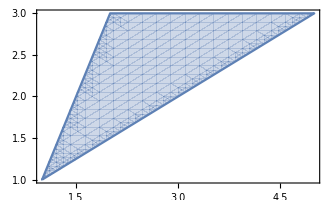
Solución:
Las rectas que pasan por los vértices son:
(2,3) y (5,3): y=3.
(1,1) y (2,3): y=2x-1, o lo que es lo mismo, x=(y+1)/2.
(1,1) y (5,3): y=(x+1)/2, o lo que es lo mismo, x= 2y-1.

-Graphics-
Observando la región, vemos que si consideramos la variación de la y, en el intervalo [1,3], podemos dejar la x variando en [(y+1)/2, 2y-1]. Así tenemos que calcular una sola integral doble: 
∫_1^3 (∫_((y+1)/2)^(2y-1) 2 x^2+3yⅆx)ⅆy=∫_1^3 (2x^3/3+3y x)|_(x=(y+1)/2)^(x=2y-1)ⅆy =  ∫_1^3 (2(2y-1)^3/3+3y (2y-1))-(2((y+1)/2)^3/3+3y (y+1)/2))ⅆy =   ∫_1^3 (3/4 (-1-y-5 y^2+7 y^3))ⅆy = 3/4 (-y-y^2/2-5 y^3/3+7 y^4/4)|_(y=1)^(y=3)=3/4 (-3-9/2-5*27/3+7*81/4)-3/4 (-1-1/2-5/3+7/4) = 3/4 (-2-8/2-130/3+7*80/4) = 3/4 (-6-130/3+140) =3/4 (134-130/3) =3/12*272 = 68

Con el Mathematica:

```mathematica
∫_1^3 (∫_((y+1)/2)^(2y-1) (2 x^2+3y)ⅆx)ⅆy
```

68

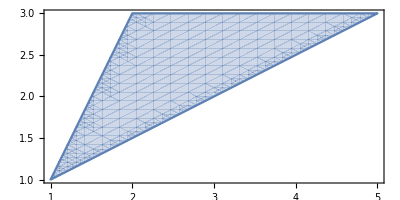

```mathematica
RegionPlot[1≤y≤3&&(y+1)/2≤x≤2y-1,{x,1,5},{y,1,3},AspectRatio->Automatic]
```

## 7.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=x^4+y^2-8 x^2-2. Enero 22

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 4 x^3-16x =4x( x^2-4) = 0 ⟹ x=0, x= 2, x=-2
		∂_y f(x,y) = 2y = 0 ⟹ y=0
Los puntos donde se anulan las dos derivadas parciales son (0,0), (2,0), (-2,0).
Para ver si es máximo, mínimo o punto de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(12 x^2-16 | 0
0 | 2)|
Hessiano (0,0) = |(-16 | 0
0 | 2)|= -32 < 0 (Punto de silla)
Hessiano (2,0) = |(32 | 0
0 | 2)|= 64 > 0 (máximo o mínimo relativo) (Como ∂_(x,x) f(2,0)= 32 >0, será mínimo local)
Hessiano (-2,0) = |(32 | 0
0 | 2)|= 64 > 0 (máximo o mínimo relativo) (como ∂_(x,x) f(-2,0)=32>0, será mínimo local)

Como el hessiano en el punto (0,0) es negativo, habrá un punto de silla. Como el hessiano en los puntos (2,0) y (-2,0) es positivo habrá un mínimo o un máximo relativo. Para saber si es máximo o mínimo vemos la derivada segunda en x (o en y) en ese punto. Como la derivada segunda es 32 >0, hay un mínimo relativo en esos dos puntos.
Con el Mathematica podemos dibujar la gráfica.

```mathematica
Plot3D[x^4+y^2-8x^2-2,{x,-3,3},{y,-1,1}]
```

-Graphics3D-

## 8.- Calcular los extremos absolutos (máximos y mínimos) de la función f(x,y)=x^3-2 y^2 en el conjunto de puntos que cumplen x^2+y^2≤1. Enero 22

Solución:
La función es polinómica y, por tanto, es continua y derivable. Los extremos pueden estar en el interior del círculo (x^2+y^2<1), o en el borde (en la circunferencia x^2+y^2=1).
Para encontrar los posibles puntos en el interior, hacemos derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 3 x^2 =0 ⟹ x=0
		∂_y f(x,y) = -4y = 0 ⟹ y=0
Las derivadas parciales se anulan en el punto (0,0) que está en el interior del recinto (0^2+0^2<1).

Ahora hay que estudiar los posibles puntos en el borde del recinto; cuando x^2+y^2=1. Podemos buscar los posibles puntos siguiendo dos ideas:
1) Multiplicadores de Lagrange:
Consideramos F(x,y,t) = f(x,y) + t g(x,y)
donde f(x,y)=x^3-2 y^2, g(x,y)=x^2+y^2-1.

		∂_x F(x,y,t) = 3 x^2 + t(2x) = x( 3x + 2t) = 0 
		∂_y F(x,y,t) = -4y+t(2y) = 2y(t-2) = 0
		∂_t F(x,y,t) = x^2+y^2-1 = 0
 La segunda ecuación se cumple cuando y=0 ó t=2. Consideremos cada caso:
 a) Si y=0, de la tercera ecuación sacamos que x=1 ó x=-1. En el caso x=1, la primera ecuación se cumpliría si t=-3/2. Si x =-1, la primera ecuación se cumpliría si t= 3/2. Por tanto, obtendríamos las soluciones (x,y,t)= (1,0,-3/2), (-1,0,3/2).
 b) Si t=2, la primera ecuación quedaría como  3 x^2 + 4x= x(3x+4)=0. Se cumpliría cuando x=0 ó x=-4/3. Cuando x=0, la tercera ecuación se cumpliría si y=1 ó y=-1. Cuando x=-4/3, la tercera ecuación no se cumpliría. Por tanto, obtenemos las soluciones (0,1,2) y (0,-1,2).
 
 Al punto interior del círculo (0,0) debemos añadir los cuatro encontrados en el borde, (1,0), (-1,0), (0,1), (0,-1). Evaluando la función f , obtenemos:
 f(0,0)=0^3-2*0^2=0, f(1,0)=1^3-2*0^2=1, f(-1,0)=(-1)^3-2*0^2=-1, f(0,1)=0^3-2*1^2=-2, f(0,-1)=0^3-2*(-1)^2=-2.
 
El máximo absoluto se encuentra en el punto (1,0) con un valor de 1, y el mínimo absoluto se alcanza en los puntos (0,1) y (0,-1) con un valor de -2.
 
Veamos ahora otra forma de estudiar el borde.
2) Se trata de buscar los posibles máximos y mínimos de f(x,y)=x^3-2 y^2 cuando x^2+y^2=1. Podríamos despejar y^2 y sustituir en la función. Tenemos que y^2=1-x^2, por tanto  f(x,y)=x^3-2(1-x^2)=x^3+2 x^2-2 que sería una función de una variable, x. Esta variable x puede moverse en el intervalo [-1,1] (para que pueda cumplirse que x^2+y^2=1).
Los extremos de x^3+2 x^2-2, en [-1,1] se encontrarían en los extremos del intervalo o en los puntos con derivada cero. La derivada es:
3 x^2+4x = x (3x+4) =0. La derivada se anula cuando x=0 ó x=-4/3. Este último valor no pertenece al intervalo. Por tanto, nos quedamos con los valores de los extremos, x=1 y x=-1 y el punto de derivada cero, x=0. Como debe cumplirse que x^2+y^2=1, los puntos candidatos a máximos o mínimos serían: (1,0) (-1,0), (0,1) y (0,-1).

Evaluamos la función f(x,y) en los cinco puntos posibles:  
 f(0,0)=0^3-2*0^2=0, f(1,0)=1^3-2*0^2=1, f(-1,0)=(-1)^3-2*0^2=-1, f(0,1)=0^3-2*1^2=-2, f(0,-1)=0^3-2*(-1)^2=-2.

El máximo absoluto se encuentra en el punto (1,0) con un valor de 1, y el mínimo absoluto se alcanza en los puntos (0,1) y (0,-1) con un valor de -2.
Con el Mathematica dibujamos la gráfica:

```mathematica
Plot3D[Which[x^2+y^2<=1,x^3-2y^2],{x,-1,1},{y,-1,1},PlotPoints->50]
```

-Graphics3D-

## 9.- Dada la función f(x,y) = 3x^3y^2 + 2x cos y + y, calcular la ecuación del plano tangente a la gráfica de la función en el punto (1,0) y utilizarlo para estimar el valor de f(0.5, 0.5). Enero 22

Solución:
La ecuación del plano tangente a la gráfica de una función de dos variables es similar a la ecuación de la recta tangente a la gráfica de una función de una variable, añadiendo un nuevo sumando. En este caso, sería:

		z=f(1,0) + ∂_x f(1,0) (x-1)+∂_y f(1,0) (y-0)
Calculamos el valor de f en el punto y sus derivadas parciales:
f(x,y) = 3x^3y^2 + 2x cos y + y
f(1,0) = 3*1^3*0^2 + 2*1* cos 0 + 0 = 0+2+0 = 2
∂_x f(x,y)= 9x^2y^2 + 2 cos y
∂_x f(1,0)= 9*1^2*0^2 + 2 cos 0 = 2
∂_y f(x,y)= 6x^3y -2x sen y + 1
∂_y f(1,0)= 6*1^3*0 -2*1* sen 0 + 1 = 1

z=f(1,0) + ∂_x f(1,0) (x-1)+∂_y f(1,0) (y-0)= 2 + 2 (x-1)+1 (y-0)= 2 + 2x-2+y = 2x+y

El valor de f(0.5,0.5) se puede aproximar utilizando el polinomio anterior y obtenemos 2*0.5+0.5=1.5

Con el Mathematica:

```mathematica
f[x_,y_]:= 3 x^3 y^2+ 2 x Cos[y]+y
```

```mathematica
f[1,0]+(D[f[x,y],x]/.{x->1,y->0}) (x-1)+(D[f[x,y],y]/.{x->1,y->0}) (y-0)//Simplify
```

2 x+y

```mathematica
Plot3D[{f[x,y],2x+y},{x,0,1.5},{y,-1,1}]
```

-Graphics3D-

```mathematica
{f[x,y],2x+y}/.{x->0.5,y->0.5}
```

{1.47133,1.5}

## 6.- Calcular la integral de la función f(x,y)= x^2+y en el triángulo de vértices (-1,0), (0,2) y (1,0). Junio 21

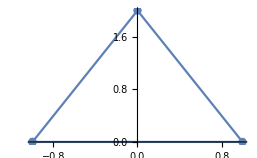
Solución:
Observamos el triángulo determinado por los puntos que nos da el problema.
-Graphics-
Las rectas que delimitan el triángulo son y=0, y=2x+2, y=2-2x.
Podríamos calcular la integral de dos formas. 
1) Observamos que la variable x varía entre -1 y 1. Para cada valor de x entre -1 y 0, la variable y varía entre 0 y 2x+2. En cambio, para cada valor de x entre 0 y 1, la variable y se mueve entre 0 y 2-2x.
2) Por otra parte, si pensamos que la variable y se mueve entre 0 y 2, podemos ver que la variable x está entre (y-2)/2 y (2-y)/2.

Así, siguiendo la primera vía la integral sería:

 ∫_-1^0 (∫_0^(2x+2) x^2+yⅆy)ⅆx + ∫_0^1 (∫_0^(-2x+2) x^2+yⅆy)ⅆx.
 
 Realizamos los cálculos:

 ∫_-1^0 (∫_0^(2x+2) x^2+yⅆy)ⅆx= ∫_-1^0 (x^2 y+y^2/2)|_(y=0)^(y=2x+2)ⅆx =  ∫_-1^0 (x^2*(2x+2)+(2x+2)^2/2- (x^2*0+0^2/2))ⅆx =  ∫_-1^0 (2 x^3+ 2 x^2+2 x^2+4x+2)ⅆx =   ∫_-1^0 (2 x^3+ 4 x^2+4x+2)ⅆx = x^4/2+ 4 x^3/3+2 x^2+2x|_(x=-1)^(x=0) = (0^4/2+ 4 0^3/3+2*0^2+2*0) - ((-1)^4/2+ 4(-1)^3/3+2(-1)^2+2(-1)) = -1/2+4/3-2+2 = (-3+8)/6= 5/6.

∫_0^1 (∫_0^(-2x+2) x^2+yⅆy)ⅆx= ∫_0^1 (x^2 y+y^2/2)|_(y=0)^(y=-2x+2)ⅆx =  ∫_0^1 (x^2*(-2x+2)+(-2x+2)^2/2- (x^2*0+0^2/2))ⅆx =  ∫_0^1 (-2 x^3+ 2 x^2+2 x^2-4x+2)ⅆx =   ∫_0^1 (-2 x^3+ 4 x^2-4x+2)ⅆx = -x^4/2+ 4 x^3/3-2 x^2+2x|_(x=0)^(x=1) = (-1^4/2+ 4 1^3/3-2*1^2+2*1) - (-0^4/2+ 4 0^3/3.2*0^2+2*0) = -1/2+4/3-2+2 = (-3+8)/6= 5/6.

El resultado sería  5/6 +  5/6 =  10/6 =  5/3

Siguiendo la segunda vía tendríamos:

∫_0^2 (∫_((y-2)/2)^((2-y)/2) x^2+yⅆx)ⅆy= ∫_0^2 (x^3/3+y x)|_(x=(y-2)/2)^(x=(2-y)/2)ⅆy =  ∫_0^2 (((2-y)/2)^3/3+y (2-y)/2- (((y-2)/2)^3/3+y (y-2)/2 ))ⅆy =  ∫_0^2 ((2-y)^3/24+(2y-y^2)/2 -(y-2)^3/24-(y^2-2y)/2 )ⅆy =  ∫_0^2 (2-y)^3/12+(2y-y^2) ⅆy= -(2-y)^4/48+y^2-y^3/3|_(y=0)^(y=2) = -(2-2)^4/48+2^2-2^3/3+(2-0)^4/48-0^2+0^3/3 =  4-8/3+16/48 =4-8/3+1/3=4-7/3 = 5/3

## 7.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)= -x^2+2x+y^2-2y+2x y + 4. Junio 21

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = -2x+2+2y = 0  ⟹ x-y=1 
		∂_y f(x,y) = 2y-2+2x = 0 ⟹ x+y=1
Resolvemos el sistema, en este caso se trata de dos ecuaciones lineales. Podemos sumar las dos ecuaciones y obtenemos x=1. Después obtenemos y=0.
 
El punto donde se anulan las dos derivadas parciales es (1,0).
Para ver si es máximo, mínimo o punto de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(-2 | 2
2 | 2)|
Hessiano (1,0) = |(-2 | 2
2 | 2)|= -8 < 0

Como el hessiano en el punto (1,0) es negativo, en ese punto hay un punto de silla.

## 8.- Calcular si existe el límite de la función f(x,y)= (3x-2y)/(x^2+ y^2) en el infinito. Junio 21

Solución:
Podemos pasar a coordenadas polares.

(3x-2y)/(x^2+ y^2)= (3ρ cos θ - 2 ρ sen θ)/ρ^2 = (3 cos θ - 2sen θ)/ρ

Vemos que cuando nos alejamos, es decir, cuando ρ → ∞, la expresión tiende a 0, con independencia de los valores de θ.

El límite de la función en el infinito es cero.

## 6.- Calcular la integral de la función f(x,y)= xy en el triángulo de vértices (0,0), (1,0) y (0,2). Febrero 21

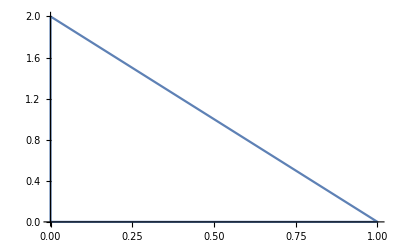
Solución:
Observamos el triángulo determinado por los puntos que nos da el problema.
-Graphics-
Las rectas que delimitan el triángulo son y=0, x=0, y=2-2x (lo que equivale a x=(2-y)/2.
Podríamos calcular la integral de dos formas. 
1) Observamos que la variable x varía entre 0 y 1. Para cada valor de x entre 0 y 1, la variable y varía entre 0 y 2-2x.
2) Por otra parte, si pensamos que la variable y se mueve entre 0 y 2, podemos ver que la variable x está entre 0 y (2-y)/2.

Así, siguiendo la primera vía la integral sería:

 ∫_0^1 (∫_0^(-2x+2) xyⅆy)ⅆx
 
 Realizamos los cálculos:

∫_0^1 (∫_0^(-2x+2) xyⅆy)ⅆx= ∫_0^1 ((x y^2)/2)|_(y=0)^(y=-2x+2)ⅆx =  ∫_0^1 ((x(-2x+2))^2/2)ⅆx =  ∫_0^1 (2 x^3- 4 x^2+2x)ⅆx = (2 x^4)/4- 4 x^3/3+x^2|_(x=0)^(x=1) = 1/2- 4/3+1  = 3/2-4/3 = (9-8)/6= 1/6.

El resultado sería  1/6.

Siguiendo la segunda vía tendríamos:

∫_0^2 (∫_0^((2-y)/2) xyⅆx)ⅆy= ∫_0^2 (x^2/2 y)|_(x=0)^(x=(2-y)/2)ⅆy =  ∫_0^2 (((2-y)/2)^2/2 y)ⅆy  =  ∫_0^2 (4y-4 y^2+y^3)/8 ⅆy= 4/8 y^2/2-4/8 y^3/3+1/8 y^4/4|_(y=0)^(y=2) = y^2/4-y^3/6+y^4/32|_(y=0)^(y=2) =2^2/4-2^3/6+2^4/32=  1-8/6+16/32=   1-8/6+1/2= 1/6

Con el Mathematica

```mathematica
∫_0^1 (∫_0^(-2x+2) (x*y)ⅆy)ⅆx
```

1/6

```mathematica
∫_0^2 (∫_0^((2-y)/2) (x*y)ⅆx)ⅆy
```

1/6

## 7.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)= -x^2+2x+y^2-4y+2. Febrero 21

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = -2x+2 = 0 ⟹ x= 1
		∂_y f(x,y) = 2y-4 = 0 ⟹ y=2
El punto donde se anulan las dos derivadas parciales es (1,2).
Para ver si es máximo, mínimo o punto de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(-2 | 0
0 | 2)|
Hessiano (1,2) = |(-2 | 0
0 | 2)|= -4 < 0

Como el hessiano en el punto (1,2) es negativo, en ese punto hay un punto de silla.

```mathematica
Plot3D[-x^2+2x+y^2-4y+2,{x,0,2},{y,1,3}]
```

-Graphics3D-

## 8.- Calcular si existe el límite de la función f(x,y)= (x + y)/xy en el infinito. Febrero 21

Solución:
Vamos a acercarnos al infinito por diferentes caminos. 
1) Por puntos de la forma (x,-x), la función vale f(x,-x)= 0/-x^2 = 0 
2) Por puntos de la forma (1,y), la función vale f(1,y)= (1+y)/y⟶ 1 (cuando y se hace muy grande, el cociente tiende a 1)
Dado que podemos aproximarnos al infinito por dos caminos distintos, tomando valores diferentes, concluimos que no existe el límite.

## 6.- Calcular la integral de la función f(x,y)= x^2+y en el rectángulo de vértices (0,0), (2,0), (0,1) y (2,1). Enero 21

Solución:
∫_0^2 (∫_0^1 x^2+yⅆy)ⅆx= ∫_0^2 (x^2 y+y^2/2)|_(y=0)^(y=1)ⅆx =  ∫_0^2 (x^2*1+1^2/2- (x^2*0+0^2/2))ⅆx =  ∫_0^2 (x^2+1/2)ⅆx = (x^3/3+x/2)|_(x=0)^(x=2) = (2^3/3+2/2)- (0^3/3+0/2)= (8/3+1)=11/3

## 7.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=x^2+2x+y^2-4y+8. Enero 21

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 2x+2 = 0 ⟹ x= -1
		∂_y f(x,y) = 2y-4 = 0 ⟹ y=2
El punto donde se anulan las dos derivadas parciales es (-1,2).
Para ver si es máximo, mínimo o punto de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(2 | 0
0 | 2)|
Hessiano (-1,2) = |(2 | 0
0 | 2)|= 4 > 0

Como el hessiano en el punto (-1,2) es positivo, en ese punto hay un mínimo o un máximo relativo. Para saber si es máximo o mínimo vemos la derivada segunda en x (o en y) en ese punto. Como la derivada segunda es 2 >0, hay un mínimo relativo en ese punto.

## 8.- Calcular si existe el límite de la función f(x,y)= x^2/(2 x^2- 3 y^2) en el punto (0,0). Enero 21

Solución:
Observamos que cuando x e y están próximos a cero, tanto el numerador como el denominador están próximos a cero. Tendríamos una indeterminación.
Vamos a acercarnos al punto (0,0) desde diferentes direcciones. 
1) Por puntos de la forma (x,0), la función vale f(x,0)= x^2/(2 x^2) = 1/2 
2) Por puntos de la forma (0,y), la función vale f(0,y)= 0/(-3 y^2)=0 
Dado que podemos aproximarnos al (0,0) por dos caminos distintos, tomando valores diferentes, concluimos que no existe el límite.

## 6.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)= x^4 + y^4 - 4xy +1. Enero 20

Solución:
Calculamos las derivadas parciales e igualamos a 0,
∂_x f[x,y] = 4 x^3-4 y = 0
∂_y f[x,y] = -4 x+4 y^3 = 0
Resolvemos el sistema, y=x^3, x=y^3, por tanto, x=y^3=x^9, de donde x(1-x^8)=0, x=0, 1, -1. Los puntos donde se anulan las derivadas parciales son (0,0), (1,1), (-1,-1).
Haciendo las derivadas segundas,
∂_(x,x) f[x,y] = 12 x^2
∂_(x,y) f[x,y] = -4
∂_(y,x) f[x,y] = -4
 ∂_(y,y) f[x,y] = 12 y^2 
 Hess(x,y)=(12 x^2 | -4
-4 | 12 y^2) 
En el punto (0,0) el determinante es negativo, por tanto hay un punto de silla. En los puntos (1,1) y (-1,-1), el determinante es positivo y la derivada segunda respecto a x, es positiva, luego son mínimos relativos.

## 7.- Estudiar, utilizando el cambio a coordenadas polares, el límite de la función f(x,y)= (x^2 y)/(x^2+y^2) en el punto (0,0). Enero 20

Solución.
Hacemos el cambio a coordenadas polares f(x,y)= (x^2 y)/(x^2+y^2)=  (r^2 cos^2 θ r sen θ)/r^2= r cos^2 θ  sen θ ⟶0 (cuando (x,y)⟶(0,0), es decir cuando r ⟶0). El límite existe y vale 0.

## 6.- Calcular si existe el límite de la función f(x,y)= (x^3+y^3)/(x^2+y^2) en el punto (0,0). Enero 2019

Solución.
Al acercarnos al punto (0,0), tanto el numerador como el denominador tienden a cero. Cambiando a coordenadas polares, x=ρ cos θ, y= ρ sen θ, nos queda la expresión  (x^3+y^3)/(x^2+y^2) = ((ρ cos θ)^3+(ρ sen θ)^3)/((ρ cos θ)^2+(ρ sen θ)^2)=(ρ^3((cos θ)^3+(sen θ)^3))/ρ^2=ρ((cos θ)^3+(sen θ)^3)⟶0 , cuando ρ⟶0.

## 7.- Calcular los máximos y mínimos absolutos de la función f(x,y)=x^2-y^2 en el recinto dado por x^2+ 2 y^2≤ 1. Enero 19

Solución:
Los máximos o mínimos pueden estar en el interior de la elipse (cuando x^2+ 2 y^2< 1) o en el borde (x^2+ 2 y^2= 1).
Para el interior, hacemos derivadas parciales y calculamos dónde se anulan:
∂_x f= 2x=0, ∂_y f= -2y=0 ⟹ x=0, y=0. Las derivadas parciales se anulan en el punto (0,0) que está dentro de la elipse pues  0^2+ 2*0^2< 1.
Respecto al borde utilizamos la técnica de los multiplicadores de Lagrange. Para ello consideramos F(x,y,λ)=x^2-y^2 + λ(x^2+ 2 y^2- 1). Haciendo derivadas parciales e igualando a cero tenemos:
∂_x F= 2x +2xλ=0 ⟹x(1+λ)=0 
∂_y F= -2y + 4yλ=0  ⟹y(-1+2λ)=0  
∂_λ F= x^2+ 2 y^2- 1=0
De la primera ecuación, una posibilidad es x=0. En este caso, de la tercera ecuación, y=±√(1/2). Con lo cual, para que se cumpla también la segunda ecuación λ debe ser 1/2. Obtenemos así unos puntos posibles (0,√(1/2)),  (0,-√(1/2)).
De la primera ecuación, si x no es cero, tenemos que λ=-1, entonces la segunda ecuación quedaría como -3y=0. Por tanto, y=0. Ahora en la tercera ecuación, x=±1. Por tanto aparecen los puntos (1,0) y (-1,0).
Juntando los cinco puntos candidatos, evaluamos la función f en ellos y obtenemos:
f(0,0)=0, f(1,0)=1, f(-1,0)=1, f(0,√(1/2))=-1/2,  f(0,-√(1/2))=-1/2.
De donde concluimos que f, en el recinto dado, tiene máximos absolutos en (1,0) y (-1,0) y mínimos absolutos en (0,√(1/2)) y  (0,-√(1/2)).

## 8.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=(x^2(x-2))^2+ y^2. Enero 19

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 2(x(x-2))^2 + 2x^2(x-2)= 2x(x-2)(x-2+x) =0 ⟹ x=0, (x-2)=0 ó (x-2+x)=0 ⟹ x=0, 2, 1
		∂_y f(x,y) = 2y = 0 ⟹ y=0
Los puntos donde se anulan las dos derivadas parciales son (0,0), (2,0) y (1,0).
Para ver si son máximos, mínimos y puntos de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(12 x^2-24x+8 | 0
0 | 2)|
Hessiano (0,0) = |(8 | 0
0 | 2)|= 16 > 0

Hessiano (2,0) = |(8 | 0
0 | 2)|= 16 > 0
Hessiano (1,0) = |(-4 | 0
0 | 2)|= -8 < 0

Como el hessiano en los puntos (0,0) y (2,0) es positivo habrá un máximo o un mínimo. Para saber si es máximo o mínimo vemos la derivada segunda en x (o en y) en esos puntos. Como la derivada segunda es 8 >0, hay mínimos relativos en esos puntos.

Como el hessiano en el punto (1,0) es negativo, en el punto (1,0) hay un punto de silla.

## 3.- Calcular la integral de la función f(x,y)= x^2+y^2 en el cuadrilátero de vértices (0,0), (1,0), (2,1) y (1,1), Integral: Enero 19. Aula de Informática

Solución:
El recinto es el cuadrilátero . Para calcular la integral, tenemos que las ecuaciones de las rectas de los lados son y=x, y=x-1, y=0, y=1. Parece más sencillo decir que la y varía entre 0 y 1, y para cada valor de y, la x varía entre y e y+1.

```mathematica
∫_0^1 (∫_y^(y+1) (x^2+y^2)ⅆx)ⅆy
```

3/2

## 3.- Calcular la integral de la función f(x,y)= 1-x-y en el triángulo de vértices (0,0), (1,0) y (0,1), para obtener el volumen de la siguiente figura. -Graphics3D-Integral: Enero 19. Aula de Informática

Solución:
El recinto es el triángulo . Para calcular la integral, tenemos que las ecuaciones de las rectas de los lados son y=1-x, y=0, x=0. Podemos plantear cualquiera de las dos integrales dobles con similar dificultad. Si por ejemplo tomamos que x varía de 0 a 1, la y variará entre 0 y 1-x.

```mathematica
∫_0^1 (∫_0^(1-x) (1-x-y)ⅆy)ⅆx
```

1/6

## 3.- Calcular la integral de la función f(x,y)= x^2+2 y^2 en el cuadrilátero de vértices (0,0), (1,0), (2,1) y (1,1), Integral: Enero 19. Aula de Informática

Solución:
El recinto es el cuadrilátero . Para calcular la integral, tenemos que las ecuaciones de las rectas de los lados son y=x, y=x-1, y=0, y=1. Parece más sencillo decir que la y varía entre 0 y 1, y para cada valor de y, la x varía entre y e y+1.

```mathematica
∫_0^1 (∫_y^(y+1) (x^2+2 y^2)ⅆx)ⅆy
```

11/6

## 3.- Calcular la integral de la función f(x,y)= 2 x^2+y^2 en el cuadrilátero de vértices (0,0), (1,0), (2,1) y (1,1), Integral: Enero 19. Aula de Informática

Solución:
El recinto es el cuadrilátero . Para calcular la integral, tenemos que las ecuaciones de las rectas de los lados son y=x, y=x-1, y=0, y=1. Parece más sencillo decir que la y varía entre 0 y 1, y para cada valor de y, la x varía entre y e y+1.

```mathematica
∫_0^1 (∫_y^(y+1) (2 x^2+y^2)ⅆx)ⅆy
```

8/3

## 7.- Calcular si existe el límite de la función f(x,y)= x/(x+2y) en el punto (0,0). Enero 19, Octubre 18, julio 18

Solución:
La función f es un cociente de dos polinomios, por tanto es continua en todos los puntos donde está definida.
 Por ello, el límite en todos los puntos donde está definida es el valor de la función. El problema es que en el punto (0,0) el denominador se anula y la función no está definida en ese punto. Al acercarnos al punto (0,0) tanto el numerador como el denominador se acercan a 0, sería una indeterminación y habría que hacer cálculos para ver si hay o no límite y cuánto valdría.

Probamos a acercarnos al (0,0) por diferentes caminos:

1) Nos acercamos por puntos de la forma x=0, f(0,y)= 0/(2y)=0. Por tanto, el limite por esta dirección sería 0.
2) Nos acercamos por puntos de la forma y=0, f(x,0)= x/(x+2*0) = 1 . Por tanto, el limite por esta dirección sería 1.
Como hemos encontrado dos direcciones con límites diferentes, concluimos que no existe el límite en el punto (0,0).

## 5.- Calcular los máximos y mínimos absolutos de la función f(x,y)=2 x^2- y^2 en el recinto dado por x^2+ y^2≤ 1. Octubre 18

Solución:
Los máximos o mínimos pueden estar en el interior del círculo (cuando x^2+ y^2< 1) o en el borde (x^2+ y^2= 1).
Para el interior, hacemos derivadas parciales y calculamos dónde se anulan:
∂_x f= 4x=0, ∂_y f= -2y=0 ⟹ x=0, y=0. Las derivadas parciales se anulan en el punto (0,0) que está dentro del círculo pues  0^2+ 0^2< 1.
Respecto al borde podemos utilizar diferentes técnicas:
PRIMERA FORMA:
1) Por multiplicadores de Lagrange. Para ello consideramos F(x,y,λ)=2 x^2-y^2 + λ(x^2+ y^2- 1). Haciendo derivadas parciales e igualando a cero tenemos:
∂_x F= 4x +2xλ=0 ⟹	x(2+λ)=0 	⟹	x=0 ó λ=-2 
∂_y F= -2y + 2yλ=0  ⟹y(-1+λ)=0 ⟹y=0 ó λ=1  
∂_λ F= x^2+ y^2- 1=0
De la primera ecuación, una posibilidad es x=0. En este caso, de la tercera ecuación, y= ±1. Con lo cual, para que se cumpla también la segunda ecuación λ debe ser 1. Obtenemos así unas soluciones posibles (0,1,1),  (0,-1,1).
De la primera ecuación, si x no es cero, tenemos que λ=-2, entonces la segunda ecuación quedaría como 3y=0. Por tanto, y=0. Ahora en la tercera ecuación, x=±1. Por tanto aparecen los puntos (1,0,-2) y (-1,0,-2).
Hemos encontrado 4 puntos posibles en el borde: (0,1), (0,-1), (1,0) y (-1,0).

Juntando los cinco puntos candidatos, evaluamos la función f en ellos y obtenemos:
f(0,0)=0, f(1,0)=2, f(-1,0)=2, f(0,1)=-1,  f(0,-1)=-1.
De donde concluimos que f, en el recinto dado, tiene máximos absolutos en (1,0) y (-1,0) y mínimos absolutos en (0,1) y  (0,-1).
SEGUNDA FORMA:
2) Podríamos despejar una de las variables. Si x^2+ y^2= 1, y^2= 1- x^2, por tanto f(x,y)=2 x^2- (1- x^2) = 3 x^2-1. Nos queda una función solo de x, con x en [-1,1]. Estudiamos los posibles máximos y mínimos de f(x)= 3 x^2-1, con x en [-1,1]. En el interior estudiamos la derivada f’(x)=6x, se anula cuando 6x=0. Por tanto x=0. Los extremos son x=-1 y x=1.
Encontrados los valores de x, calculamos los de y, sabiendo que x^2+ y^2= 1.
x=0	⟹	y^2= 1	⟹	y=1, y=-1 	⟹ Puntos (0,1), (0,-1)
x=1	⟹	y^2= 0	⟹	y=0		⟹ Punto (1,0)
x=-1	⟹	y^2= 0	⟹	y=0		⟹ Punto (-1,0)
Consideramos los 4 puntos del borde y el punto de interior y evaluamos f(x,y)
f(0,0)=0, f(1,0)=2, f(-1,0)=2, f(0,1)=-1,  f(0,-1)=-1.
De donde concluimos que f, en el recinto dado, tiene máximos absolutos en (1,0) y (-1,0) y mínimos absolutos en (0,1) y  (0,-1).
TERCERA FORMA:
3) Podemos parametrizar los puntos de la circunferencia. Los puntos de la circunferencia x^2+ y^2= 1, pueden ponerse como (cos t, sen t) con t en [0,2π]. Así  f(x,y)=2 x^2- y^2= 2 cos^2 t- sen^2 t = 2 cos^2 t- (1-cos^2 t) = 3 cos^2 t- 1. 
Nos encontramos con una función de t, f(t)=3 cos^2 t- 1, en el intervalo [0,2π]. En el interior del intervalo, estudiamos la derivada f’(t)=6cos t sen t, que se anula cuando se anula el seno o el coseno, es decir,  t=π, t=π/2, t=3π/2. Los extremos del intervalo son t=0, t=2π.
Encontrados los valores de t, calculamos los de x e y

t=0		⟹ (cos 0, sen 0)= (1,0)
t=π/2	⟹ (cos π/2, sen π/2)= (0,1)
t=π		⟹ (cos π, sen π)= (-1,0)
t=3π/2	⟹ (cos 3π/2, sen 3π/2)= (0,-1)
t=2π		⟹ (cos 2π, sen 2π)= (1,0)

Consideramos los 4 puntos del borde y el punto de interior y evaluamos f(x,y)
f(0,0)=0, f(1,0)=2, f(-1,0)=2, f(0,1)=-1,  f(0,-1)=-1.
De donde concluimos que f, en el recinto dado, tiene máximos absolutos en (1,0) y (-1,0) y mínimos absolutos en (0,1) y  (0,-1).

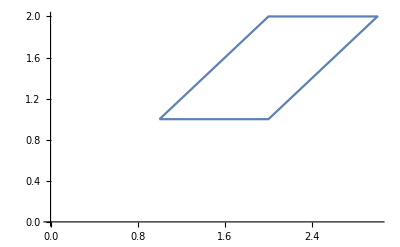

```mathematica
ListPlot[{{1,1},{2,1},{3,2},{2,2},{1,1}},Joined->True,AxesOrigin->{0,0}]
```

## 6.- Calcular el valor de la integral de la función f(x,y) = x+2y en el paralelogramo de vértices (1,1), (2,1), (2,2), (3,2). Octubre 18, Julio 18

Solución:
Observamos el paralelogramo determinado por los puntos que nos da el problema.
-Graphics-
Las rectas que delimitan el paralelogramo son:
	y=1 (la que pasa por (1,1) y (2,1)), 
	y=2 (la que pasa por (2,2) y (3,2)),
	y=x ó x=y (la que pasa por (1,1) y (2,2)),
	y=x-1 ó x=y+1(la que pasa por (2,1) y (3,2)).
Podríamos calcular la integral de dos formas. 
1) Observamos que la variable x varía entre 1 y 3. Para cada valor de x entre 1 y 2, la variable y varía entre 1 y x. En cambio, para cada valor de x entre 2 y 3, la variable y se mueve entre x-1 y 2.
2) Por otra parte, si pensamos que la variable y se mueve entre 1 y 2, podemos ver que la variable x está entre y e y+1.

Así, siguiendo la primera vía la integral sería:

 ∫_1^2 (∫_1^x (x+2y)ⅆy)ⅆx + ∫_2^3 (∫_(x-1)^2 (x+2y)ⅆy)ⅆx.
 
 Realizamos los cálculos:

 ∫_1^2 (∫_1^x (x+2y)ⅆy)ⅆx= ∫_1^2 (x y+y^2)|_(y=1)^(y=x)ⅆx =  ∫_1^2 (x*x+x^2- (x*1+1^2))ⅆx =  ∫_1^2 (2 x^2- x-1)ⅆx =    (2 x^3)/3-x^2/2-x|_(x=1)^(x=2) = ((2*2^3)/3-2^2/2-2) - ((2*1^3)/3-1^2/2-1) = 16/3-4-2/3+3/2 = (32-24-4+9)/6= 13/6.

∫_2^3 (∫_(x-1)^2 (x+2y)ⅆy)ⅆx= ∫_2^3 (x y+y^2)|_(y=x-1)^(y=2)ⅆx =  ∫_2^3 (x*2+2^2- (x(x-1)+(x-1)^2))ⅆx =  ∫_2^3 (2x+4-(x^2-x+x^2-2x+1))ⅆx =∫_2^3 (2x+4-(2 x^2-3x+1))ⅆx=∫_2^3 (5x+3-2 x^2)ⅆx=  (5 x^2)/2 +3x-(2 x^3)/3|_(x=2)^(x=3) = ((5*3^2)/2 +3*3-(2*3^3)/3) - ( (5*2^2)/2 +3*2-(2*2^3)/3) = (45/2 +9-18)-( 10 +6-16/3) = 45/2 -9- 16+16/3 = (135-150+32)/6 =17/6.

El resultado sería  13/6 +  17/6 =  30/6 =5

Siguiendo la segunda vía tendríamos:

∫_1^2 (∫_y^(y+1) (x+2y)ⅆx)ⅆy = ∫_1^2 (x^2/2+2y x)|_(x=y)^(x=y+1)ⅆy =  ∫_1^2 ((y+1)^2/2+2y (y+1)- (y^2/2+2y y))ⅆy =  ∫_1^2 ((y^2+2y+1)/2+2 y^2+2y- (y^2/2+2 y^2))ⅆy  =   ∫_1^2 (1/2+3y)ⅆy = 1/2 y+(3 y^2)/2|_(y=1)^(y=2) = (1/2*2+(3*2^2)/2)-(1/2*1+(3*1^2)/2) = (1+6)-(1/2+3/2) = 7-2 = 5.

Como es lógico, las dos vías nos llevan a la solución: la integral vale 5.

Con el Mathematica:

```mathematica
∫_1^2 (∫_1^x (x+2y)ⅆy)ⅆx+∫_2^3 (∫_(x-1)^2 (x+2y)ⅆy)ⅆx
```

5

```mathematica
∫_1^2 (∫_y^(y+1) (x+2y)ⅆx)ⅆy
```

5

## 9.- Calcular el plano tangente a la gráfica de la función f(x,y) = e^(x+2y) en el punto (0,0) y estimar con su ayuda el valor de f(0.2, -0.1). Octubre 18

Solución:
La ecuación del plano tangente a la gráfica de una función de dos variables es similar a la ecuación de la recta tangente a la gráfica de una función de una variable, añadiendo un nuevo sumando. En este caso, sería:

		z=f(0,0) + ∂_x f(0,0) (x-0)+∂_y f(0,0) (y-0)
Calculamos el valor de f en el punto y sus derivadas parciales:
f(x,y) = e^(x+2y)
f(0,0) = e^(0+2*0) = e^0 = 1
∂_x f(x,y)= e^(x+2y)
∂_x f(0,0)= e^(0+2*0) = e^0 = 1
∂_y f(x,y)= 2 e^(x+2y)
∂_y f(0,0)= 2 e^(0+2*0) = 2 e^0 = 2

z=f(0,0) + ∂_x f(0,0) (x-0)+∂_y f(0,0) (y-0)= 1 + 1 (x-0)+2 (y-0)= 1 + x + 2y

El valor de f(0.2,-0.1) se puede aproximar utilizando el polinomio anterior y obtenemos 1+0,2+2*(-0,1)=1

Con el Mathematica:

```mathematica
f[x_,y_]:=ⅇ^(x+2y)
```

```mathematica
f[0,0]+(D[f[x,y],x]/.{x->0,y->0})(x-0) + (D[f[x,y],y]/.{x->0,y->0})(y-0)
```

1+x+2 y

```mathematica
%/.{x->0.2,y->-0.1}
```

1.

## 5.- Calcular los máximos y mínimos absolutos de la función f(x,y)=x^2-2 y^2 en el recinto dado por x^2+ y^2≤ 1. Julio 18

Solución:
Los máximos o mínimos pueden estar en el interior del círculo (cuando x^2+ y^2< 1) o en el borde (x^2+ y^2= 1).
Para el interior, hacemos derivadas parciales y calculamos dónde se anulan:
∂_x f= 2x=0, ∂_y f= -4y=0 ⟹ x=0, y=0. Las derivadas parciales se anulan en el punto (0,0) que está dentro del círculo pues  0^2+ 0^2< 1.
Respecto al borde podemos utilizar diferentes técnicas:
PRIMERA FORMA:
1) Por multiplicadores de Lagrange. Para ello consideramos F(x,y,λ)=x^2-2 y^2 + λ(x^2+ y^2- 1). Haciendo derivadas parciales e igualando a cero tenemos:
∂_x F= 2x + 2xλ=0 	⟹	x(2+2λ)=0 	⟹	x=0 ó λ=-1 
∂_y F= -4y + 2yλ=0  	⟹	y(-4+2λ)=0	⟹	y=0 ó λ=2  
∂_λ F= x^2+ y^2- 1=0
De la primera ecuación, una posibilidad es x=0. En este caso, de la tercera ecuación, y= ±1. Con lo cual, para que se cumpla también la segunda ecuación λ debe ser 2. Obtenemos así unas soluciones posibles (0,1,2),  (0,-1,2).
De la primera ecuación, si x no es cero, tenemos que λ=-1, entonces la segunda ecuación quedaría como -6y=0. Por tanto, y=0. Ahora en la tercera ecuación, x=±1. Por tanto aparecen los puntos (1,0,-1) y (-1,0,-1).
Hemos encontrado 4 puntos posibles en el borde: (0,1), (0,-1), (1,0) y (-1,0).

Juntando los cinco puntos candidatos, evaluamos la función f en ellos y obtenemos:
f(0,0)=0, f(1,0)=1, f(-1,0)=1, f(0,1)=-2,  f(0,-1)=-2.
De donde concluimos que f, en el recinto dado, tiene máximos absolutos en (1,0) y (-1,0) y mínimos absolutos en (0,1) y  (0,-1).
SEGUNDA FORMA:
2) Podríamos despejar una de las variables. Si x^2+ y^2= 1, y^2= 1- x^2, por tanto f(x,y)=x^2-2 y^2=x^2- 2(1- x^2) = 3 x^2-2. Nos queda una función solo de x, con x en [-1,1]. Estudiamos los posibles máximos y mínimos de f(x)= 3 x^2-2, con x en [-1,1]. En el interior estudiamos la derivada f’(x)=6x, se anula cuando 6x=0. Por tanto x=0. Los extremos son x=-1 y x=1.
Encontrados los valores de x, calculamos los de y, sabiendo que x^2+ y^2= 1.
x=0	⟹	y^2= 1	⟹	y=1, y=-1 	⟹ Puntos (0,1), (0,-1)
x=1	⟹	y^2= 0	⟹	y=0		⟹ Punto (1,0)
x=-1	⟹	y^2= 0	⟹	y=0		⟹ Punto (-1,0)
Consideramos los 4 puntos del borde y el punto de interior y evaluamos f(x,y)
f(0,0)=0, f(1,0)=1, f(-1,0)=1, f(0,1)=-2,  f(0,-1)=-2.
De donde concluimos que f, en el recinto dado, tiene máximos absolutos en (1,0) y (-1,0) y mínimos absolutos en (0,1) y  (0,-1).
TERCERA FORMA:
3) Podemos parametrizar los puntos de la circunferencia. Los puntos de la circunferencia x^2+ y^2= 1, pueden ponerse como (cos t, sen t) con t en [0,2π]. Así  f(x,y)=x^2- 2 y^2= cos^2 t- 2 sen^2 t = cos^2 t- 2(1-cos^2 t) = 3 cos^2 t- 2. 
Nos encontramos con una función de t, f(t)=3 cos^2 t- 2, en el intervalo [0,2π]. En el interior del intervalo, estudiamos la derivada f’(t)=6cos t sen t, que se anula cuando se anula el seno o el coseno, es decir,  t=π, t=π/2, t=3π/2. Los extremos del intervalo son t=0, t=2π.
Encontrados los valores de t, calculamos los de x e y

t=0		⟹ (cos 0, sen 0)= (1,0)
t=π/2	⟹ (cos π/2, sen π/2)= (0,1)
t=π		⟹ (cos π, sen π)= (-1,0)
t=3π/2	⟹ (cos 3π/2, sen 3π/2)= (0,-1)
t=2π		⟹ (cos 2π, sen 2π)= (1,0)

Consideramos los 4 puntos del borde y el punto de interior y evaluamos f(x,y)
f(0,0)=0, f(1,0)=1, f(-1,0)=1, f(0,1)=-2,  f(0,-1)=-2.
De donde concluimos que f, en el recinto dado, tiene máximos absolutos en (1,0) y (-1,0) y mínimos absolutos en (0,1) y  (0,-1).

## 9.- Calcular el plano tangente a la gráfica de la función f(x,y) = e^(x+2y) en el punto (0,0) y estimar con su ayuda el valor de f(0.1, -0.2). Julio 18

Solución:
La ecuación del plano tangente a la gráfica de una función de dos variables es similar a la ecuación de la recta tangente a la gráfica de una función de una variable, añadiendo un nuevo sumando. En este caso, sería:

		z=f(0,0) + ∂_x f(0,0) (x-0)+∂_y f(0,0) (y-0)
Calculamos el valor de f en el punto y sus derivadas parciales:
f(x,y) = e^(x+2y)
f(0,0) = e^(0+2*0) = e^0 = 1
∂_x f(x,y)= e^(x+2y)
∂_x f(0,0)= e^(0+2*0) = e^0 = 1
∂_y f(x,y)= 2 e^(x+2y)
∂_y f(0,0)= 2 e^(0+2*0) = 2 e^0 = 2

z=f(0,0) + ∂_x f(0,0) (x-0)+∂_y f(0,0) (y-0)= 1 + 1 (x-0)+2 (y-0)= 1 + x + 2y

El valor de f(0.1,-0.2) se puede aproximar utilizando el polinomio anterior y obtenemos 1+0,1+2*(-0,2)=0.7

Con el Mathematica:

```mathematica
f[x_,y_]:=ⅇ^(x+2y)
```

```mathematica
f[0,0]+(D[f[x,y],x]/.{x->0,y->0})(x-0) + (D[f[x,y],y]/.{x->0,y->0})(y-0)
```

1+x+2 y

```mathematica
%/.{x->0.1,y->-0.2}
```

0.7

## 7.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=(x^2-4)^2+ y^2. Enero 18

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 2(x^2-4)2x = 0 ⟹ x=0 ó x^2-4= 0 ⟹ x=0, 2, -2
		∂_y f(x,y) = 2y = 0 ⟹ y=0
Los puntos donde se anulan las dos derivadas parciales son (0,0), (2,0) y (-2,0).
Para ver si son máximos, mínimos y puntos de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(12 x^2-16 | 0
0 | 2)|
Hessiano (0,0) = |(-16 | 0
0 | 2)|= -32 < 0

Hessiano (2,0) = |(32 | 0
0 | 2)|= 64 > 0
Hessiano (-2,0) = |(32 | 0
0 | 2)|= 64 > 0

Como el hessiano en el punto (0,0) es negativo, en el punto (0,0) hay un punto de silla.

Como el hessiano en los puntos (2,0) y (-2,0) es positivo habrá un máximo o un mínimo. Para saber si es máximo o mínimo vemos la derivada segunda en x (o en y) en esos puntos. Como la derivada segunda es 32 >0, hay mínimos relativos en esos puntos.

## 8.- Calcular si existe el límite de la función f(x,y)= x^2/(x^2+y^2) en el punto (0,0). Enero 18

Solución:
La función f es un cociente de dos polinomios, por tanto es continua en todos los puntos donde está definida. Por ello, el límite en todos los puntos donde está definida es el valor de la función. El problema es que en el punto (0,0) el denominador se anula y la función no está definida en ese punto. Al acercarnos al punto (0,0) tanto el numerador como el denominador se acercan a 0, sería una indeterminación y habría que hacer cálculos para ver si hay o no límite y cuánto valdría.

Probamos a acercarnos al (0,0) por diferentes caminos:

1) Nos acercamos por puntos de la forma x=0, f(0,y)= 0/y^2=0. Por tanto, el limite por esta dirección sería 0.
2) Nos acercamos por puntos de la forma x=y, f(x,x)= x^2/(x^2+x^2) = 1/2. Por tanto, el limite por esta dirección sería 1/2.
Como hemos encontrado dos direcciones con límites diferentes, concluimos que no existe el límite en el punto 0.

## 3.- Calcular la integral de la función f(x,y)= 1-x-y en el triángulo de vértices (0,0), (1,0) y (0,1), para obtener el volumen de la siguiente figura. -Graphics3D-Integral: Enero 18. Aula de Informática

Solución:
Siguiendo lo explicado en Prácticas, sobre integrales dobles:

```mathematica
∫_0^1 (∫_0^(1-x) (1-x-y)ⅆy)ⅆx
```

1/6

## 3.- Calcular la integral de la función f(x,y)= x^2+y^2 en el triángulo de vértices (0,0), (1,0) y (1,1), para obtener el volumen de la siguiente figura. -Graphics3D- Integral: Enero 18. Aula de Infromática

Solución: Seguimos lo que aparece en Prácticas:
El conjunto donde tenemos que realizar la integral es el triángulo de vértices (0,0), (1,0) y (1,1).

```mathematica
RegionPlot[0≤x≤1&&0≤y≤x,{x,0,1},{y,0,1},AspectRatio->Automatic]
```

-Graphics-

En este caso, podemos considerar una cualquiera de las variables, por ejemplo la x. La variable x se mueve entre 0 y 1. Una vez fijado el valor de x, entre 0 y 1. El valor de y se moverá entre 0 y x. La variable y se movería desde el 0 hasta el punto de la recta que une (0,0) y (1,1). Se trata de la recta y=x.

```mathematica
∫_0^1 ∫_0^x (x^2+y^2)ⅆyⅆx
```

1/3

## Problemas de examen. Tema 9. Ecuaciones diferenciales.

## 9.- Encontrar las soluciones de la ecuación diferencial y’’ - y = x - 3. Julio 23

Solución:
Se trata de una ecuación diferencial lineal de coeficientes constantes completa. 
1) Se resuelve en primer lugar, la ecuación diferencial homogénea: y’’ - y = 0. 
	Para ello se resuelve la ecuación polinómica asociada: x^2-1 = 0;  x^2= 1; x= 1, -1.
	Si las soluciones de la ecuación polinómica son 1 y -1, la solución general de la ecuación diferencial homogénea es:
	y_h(x) =  C1  ⅇ^x  + C2  ⅇ^-x , con C1 y C2 números reales cualquiera.
2) A continuación se busca una solución particular de la ecuación diferencial completa: y’’ - y = x-3.
	Nos fijamos en que el término independiente es un polinomio de grado 1. (Que no es solución de la ecuación homogénea.) Probaremos con una función del tipo  y_p(x) = a + b x.
	y_p(x) = a + b x 
	y_p'(x) = b 
	y_p''(x) = 0 
Ahora sustituimos en la ecuación diferencial:
	y_p'' - y_p = 0  - (a + b x ) = -a - b x = x-3
De donde a=3, b= -1. 
	La solución particular es  y_p(x) = 3 - x.
La solución general es y(x) = 3-x+C1 ⅇ^x+C2  ⅇ^-x, con C1 y C2 números reales cualquiera

Con el Mathematica

```mathematica
DSolve[y''[x]-y[x]==x-3,y[x],x]
```

{{y[x]→3-x+ⅇ^x C[1]+ⅇ^-x C[2]}}

## 9.- Encontrar la solución del problema de valores iniciales y’ + y = x, con la condición y(0)=1. Enero 23

Solución:
Se trata de una ecuación diferencial lineal de coeficientes constantes completa. 
1) Se resuelve en primer lugar, la ecuación diferencial homogénea: y’ + y = 0. 
	Para ello se resuelve la ecuación polinómica asociada: x+1 = 0;  x=- 1.
	Si la solución de la ecuación polinómica es -1, la solución general de la ecuación diferencial homogénea es:
	y_h(x) =  C ⅇ^-x , con C número real cualquiera.
2) A continuación se busca una solución particular de la ecuación diferencial completa: y’ + y = x.
	Nos fijamos en que el término independiente es un polinomio de grado 1. (Que no es solución de la ecuación homogénea.) Probaremos con una función del tipo  y_p(x) = a + b x.
	y_p(x) = a + b x 
	y_p'(x) = b 
Ahora sustituimos en la ecuación diferencial:
	y_p' + y_p = b  + (a + b x ) = b+a + b x = x
De donde b=1, b+a= 0. Por tanto, b=1, a=-b=-1
	La solución particular es  y_p(x) = -1 +x.
La solución general es y(x) = -1+x+C ⅇ^-x, con C número real cualquiera.

A continuación consideramos la condición inicial, y(0)=1.

y(0) = -1+0+C ⅇ^-0 = -1+C = 1, de donde C=2.

Por tanto, la solución del problema es y(x) = -1+x+2 ⅇ^-x

Con el Mathematica

```mathematica
DSolve[{y'[x]+y[x]==x,y[0]==1},y[x],x]
```

{{y[x]→ⅇ^-x (2-ⅇ^x+ⅇ^x x)}}

## 9.- Resolver la ecuación diferencial y’’ - 4y = 4 t + 1. Octubre 22

Solución:
Se trata de una ecuación diferencial lineal de coeficientes constantes completa. 
1) Se resuelve en primer lugar, la ecuación diferencial homogénea: y’’ -4 y = 0. 
	Para ello se resuelve la ecuación polinómica asociada: x^2-4 = 0;  x= -2, 2.
	Si las soluciones de la ecuación polinómica son -2 y 2, la solución general de la ecuación diferencial homogénea es:
	y_h(t) =  C_1 ⅇ^(-2t)+ C_2 ⅇ^(2t) , con  C_1 , C_2  números reales cualquiera.
2) A continuación se busca una solución particular de la ecuación diferencial completa: y’’ - 4y = 4 t + 1.
	Nos fijamos en que el término independiente es un polinomio de grado 1. (Que no es solución de la ecuación homogénea.) Probaremos con una función del tipo  y_p(t) = a + b t.
	y_p(t) = a + b t 
	y_p'(t) = b
	y_p'’(t) = 0 
Ahora sustituimos en la ecuación diferencial:
	y_p'' - 4 y_p = 0  - 4 (a + b t) = -4a -4bt = 4t+1
De donde -4b=4, -4a=1. Por tanto, b=-1, a=-1/4
	La solución particular es  y_p(t) = -1/4 - t.
La solución general es y(x) = -1/4-t+  C_1 ⅇ^(-2t)+C_2 ⅇ^(2t) , con  C_1 , C_2 números reales cualquiera.

Con el Mathematica

```mathematica
DSolve[y''[t]-4y[t]==4t+1,y[t],t]
```

{{y[t]→1/4 (-1-4 t)+ⅇ^(2 t) C[1]+ⅇ^(-2 t) C[2]}}

## 9.- Resolver el problema de valores iniciales y’ = x y con la condición inicial y(0)=1. Julio 22

Solución:

Tratamos primero de resolver la ecuación diferencial encontrando la solución general. Después impondremos la condición inicial y buscaremos la solución del problema de valores iniciales.
La ecuación diferencial y’ = x y es una ecuación diferencial de variables separadas. Podemos escribir y’ como dy/dx. Una solución fácil de encontrar es la función constante y(x)=0. Si y es distinto de cero,

dy/dx= x y ⟹ dy/y= x dx ⟹  ∫1/y ⅆy = ∫xⅆx ⟹ Log |y| = x^2/2  + C ⟹  |y| = e^(x^2/2+C)  = e^(x^2/2) e^C⟹ y = ±e^(x^2/2) e^C (la exponencial multiplicada por una constante diferente de cero) 
Uniendo con la solución cero, podemos escribir como solución general y(x) = K e^(x^2/2), con K un número real cualquiera.
Para encontrar la solución particular del problema de valores iniciales, imponemos la condición inicial y(0)=1,
y(0) = K e^(0^2/2) = K, por tanto K debe ser 1.
La solución del PVI es y(x) = e^(x^2/2).

## 10.- Resolver la ecuación diferencial y’ - y = 3 x^2 - 2x + 1. Julio 22

Solución:
Se trata de una ecuación diferencial lineal de orden 1 con coeficientes constantes completa. 

Para resolverla, comenzamos por estudiar la ecuación homogénea, y’-y=0.
La ecuación algebraica asociada es x-1=0. La solución es x=1, por tanto, la solución general de la homogénea es yh(x) = C e^x.

Ahora consideramos la ecuación completa. El término independiente es un polinomio de grado 2, por ello vamos a buscar una solución particular que sea un polinomio de grado dos.
yp(x) = a x^2 + bx + c
yp’(x) = 2a x + b
Sustituimos en la ecuación diferencial yp’ - yp = (2ax+b)-(a x^2 + bx + c) = -a x^2 + (2a-b)x + b-c = 3 x^2 - 2x + 1.
De aquí obtenemos que -a=3, 2a-b=-2, b-c=1. Por tanto, a=-3, b=2+2a=2-6=-4, c=b-1=-4-1=-5.
La solución particular es yp(x)=-3 x^2 - 4x - 5. La solución general de la ecuación completa es y(x) =  C e^x- 3 x^2 - 4x - 5, con C un número real cualquiera.

## 10.- Resolver la ecuación diferencial y’’ - y = 3 x^2-2x+1. Enero 22

Solución:
Se trata de una ecuación diferencial lineal de coeficientes constantes completa. 
1) Se resuelve en primer lugar, la ecuación diferencial homogénea: y’’ - y = 0. 
	Para ello se resuelve la ecuación polinómica asociada: x^2 - 1 = 0; x^2 = 1;  x=± 1.
	Si las soluciones de la ecuación polinómica son 1 y -1, la solución general de la ecuación diferencial homogénea es:
	y_h(x) = C_1 ⅇ^x +  C_2 ⅇ^-x , con C_1 , C_2 números reales cualesquiera
2) A continuación se busca una solución particular de la ecuación diferencial completa: y’’ - y = 3 x^2 - 2x + 1.
	Nos fijamos en que el término independiente es un polinomio de grado 2. (Que no es solución de la ecuación homogénea.) Probaremos con una función del tipo  y_p(x) = a + b x + c x^2.
	y_p(x) = a + b x + c x^2
	y_p'(x) = b + 2 c x
	y_p''(x) = 2c
Ahora sustituimos en la ecuación diferencial:
	y_p'' - y_p = 2c  - (a + b x + c x^2) = 2c - a - b x - c x^2 = 3 x^2-2x+1
De donde -c=3, -b=-2, 2c-a= 1. Por tanto, c=-3, b=2, a=2c-1=-6-1=-7
	La solución particular es  y_p(x) = -7 +2x-3x^2.
La solución general es y(x) = -7+2x-3 x^2+C_1 ⅇ^x +  C_2 ⅇ^-x , con C_1 , C_2 números reales cualesquiera.

Con el Mathematica

```mathematica
DSolve[y''[x]-y[x]==3x^2-2x+1,y[x],x]
```

{{y[x]→-7+2 x-3 x^2+ⅇ^x C[1]+ⅇ^-x C[2]}}

Observación:
Si la ecuación hubiese sido y’’’ - y’’ = 3 x^2 - 2x + 1, al resolver la ecuación diferencial homogénea: y’’’ - y’’ = 0 habríamos tenido como ecuación polinómica asociada: x^3 - x^2 = x^2(x-1) = 0; con lo que x^2 = 0 ó x-1=0.
	Tenemos una solución doble. La solución general de la ecuación diferencial homogénea es:
	y_h(x) = C_1 ⅇ^(1*x) +  C_2 ⅇ^(0*x) + C_3 x ⅇ^(0*x) =  C_1 ⅇ^x +  C_2 *1 + C_3 x *1 = C_1 ⅇ^x +  C_2 + C_3 x, con C_1 , C_2, C_3 números reales cualesquiera
2) A continuación se busca una solución particular de la ecuación diferencial completa: y’’’ - y’’ = 3 x^2 - 2x + 1.
	Ahora tenemos que los polinomios de grado uno son soluciones de la homogénea, por ello en lugar de probar con un polinomio de grado 2, como hicimos anteriormente, multiplicaremos por x^2, y probaremos con una función del tipo  y_p(x) = a x^2 + b x^3 + c x^4.
	y_p(x) = a x^2 + b x^3 + c x^4
	y_p'(x) = 2 a x + 3 b x^2 + 4 c x^3
	y_p''(x) = 2 a + 6 b x + 12 c x^2
	y_p'''(x) =  6 b + 24 c x
	
Ahora sustituimos en la ecuación diferencial:
	y_p''' - y''_p = (6 b + 24 c x)  - (2 a + 6 b x + 12 c x^2) = 6b-2a + (24c-6b) x -12 c x^2 = 3 x^2-2x+1
De donde -12 c=3, 24c-6b=-2, 6b-2a= 1. Por tanto, c=-(1/4), b=-(2/3), a=-(5/2)
	La solución particular es  y_p(x) = -(5/2) x^2  -(2/3) x^3 -(1/4) x^4.
La solución general es y(x) = -(5/2)x^2-(2/3)x^3-(1/4)x^4 + C_1 ⅇ^x +  C_2 + C_3 x  , con C_1 , C_2, C_3 números reales cualesquiera.

```mathematica
DSolve[y'''[x]-y''[x]==3x^2-2x+1,y[x],x]
```

{{y[x]→-(5 x^2)/2-(2 x^3)/3-x^4/4+ⅇ^x C[1]+C[2]+x C[3]}}

## 2.- Supongamos que un café sale de la máquina a 80 grados y tras un minuto en una sala que se encuentra a 20 grados, la temperatura baja hasta los 70 grados. Suponemos la ley de enfriamiento de Newton, es decir, que la temperatura del café sigue la ecuación diferencial y’=K(M-y), donde M es la temperatura del medio ambiente, K una constante que depende de cómo se pierde el calor e y(x) la temperatura del café en el momento x. ¿Qué temperatura tendrá el café a los 3 minutos de salir de la máquina? 1) 44.1127, 2) 40.0939, 3) 48.9352, 4) 61.6667, 5) 54.7222 Enero 22. Aula de Informática

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[{y'[x]==K(20-y[x]),y[0]==80},y[x],x]
```

{{y[x]→20 ⅇ^(-K x) (3+ⅇ^(K x))}}

```mathematica
y[x_]:=20 ⅇ^(-K x) (3+ⅇ^(K x))
```

```mathematica
Solve[y[1]==70,K,Reals]
```

{{K→Log[2]+Log[3]-Log[5]}}

```mathematica
y[3]/.%//N
```

{54.7222}

## 9.- Resolver la ecuación diferencial y’’ - 4y = 4 t + 2. Octubre 21

Solución:
Se trata de una ecuación diferencial lineal de coeficientes constantes completa. 
1) Se resuelve en primer lugar, la ecuación diferencial homogénea: y’’ -4 y = 0. 
	Para ello se resuelve la ecuación polinómica asociada: x^2-4 = 0;  x= -2, 2.
	Si las soluciones de la ecuación polinómica son -2 y 2, la solución general de la ecuación diferencial homogénea es:
	y_h(t) =  C_1 ⅇ^(-2t)+ C_2 ⅇ^(2t) , con  C_1 , C_2  números reales cualquiera.
2) A continuación se busca una solución particular de la ecuación diferencial completa: y’’ - 4y = 4 t + 2.
	Nos fijamos en que el término independiente es un polinomio de grado 1. (Que no es solución de la ecuación homogénea.) Probaremos con una función del tipo  y_p(t) = a + b t.
	y_p(t) = a + b t 
	y_p'(t) = b
	y_p'’(t) = 0 
Ahora sustituimos en la ecuación diferencial:
	y_p'' - 4 y_p = 0  - 4 (a + b t) = -4a -4bt = 4t+2
De donde -4b=4, -4a=2. Por tanto, b=-1, a=-1/2
	La solución particular es  y_p(t) = -1/2 - t.
La solución general es y(x) = -1/2-t+  C_1 ⅇ^(-2t)+C_2 ⅇ^(2t) , con  C_1 , C_2 números reales cualquiera.

Con el Mathematica

```mathematica
DSolve[y''[t]-4y[t]==4t+2,y[t],t]
```

{{y[t]→1/2 (-1-2 t)+ⅇ^(2 t) C[1]+ⅇ^(-2 t) C[2]}}

## 9.- Resolver la ecuación diferencial y’’ - y = 2 x + 1 Junio 21

Solución:
Se trata de una ecuación diferencial lineal de coeficientes constantes completa. 
1) Se resuelve en primer lugar, la ecuación diferencial homogénea: y’’ - y = 0. 
	Para ello se resuelve la ecuación polinómica asociada: x^2 - 1 = 0; x^2 = 1;  x=± 1.
	Si las soluciones de la ecuación polinómica son 1 y -1, la solución general de la ecuación diferencial homogénea es:
	y_h(x) = C_1 ⅇ^x +  C_2 ⅇ^-x , con C_1 , C_2 números reales cualesquiera
2) A continuación se busca una solución particular de la ecuación diferencial completa: y’’ - y = 2 x + 1
	Nos fijamos en que el término independiente es un polinomio de grado 1. Probaremos con una función del tipo  y_p(x) = a + b x 
	y_p(x) = a + b x 
	y_p'(x) = b
	y_p''(x) = 0
Ahora sustituimos en la ecuación diferencial:
	y_p'' - y_p = -a - bx = 2x + 1
	De donde -b=2 y -a=1. Por tanto, a=-1, b=-2
	La solución particular es  y_p(x) = -1-2x
La solución general de la ecuación diferencia es y(x) = -1 -2x + C_1 ⅇ^x +  C_2 ⅇ^-x , con C_1 , C_2 números reales cualesquiera.

## 9.- Resolver la ecuación diferencial y’’ - 9y = 2 cos 3x. Febrero 21

Solución:
Se trata de una ecuación diferencial lineal de coeficientes constantes completa. 
1) Se resuelve en primer lugar, la ecuación diferencial homogénea: y’’ -9y = 0. 
	Para ello se resuelve la ecuación polinómica asociada: x^2-9 = 0;  x= -3, 3.
	Si las soluciones de la ecuación polinómica son -3 y 3, la solución general de la ecuación diferencial homogénea es:
	y_h(x) =  C_1 ⅇ^(-3x)+ C_2 ⅇ^(3x) , con  C_1 , C_2  números reales cualquiera.
2) A continuación se busca una solución particular de la ecuación diferencial completa: y’’ - 9y = 2 cos 3x.
	Nos fijamos en que el término independiente es una función coseno. (Que no es solución de la ecuación homogénea.) Probaremos con una función del tipo  y_p(x) = a cos 3x + b sen 3x.
	y_p(x) = a cos 3x + b sen 3x
	y_p’(x) = -3a sen 3x + 3b cos 3x
	y_p’’(x) = -9a cos 3x -9b sen 3x 
Ahora sustituimos en la ecuación diferencial:
	y_p'' - 9 y_p = -9a cos 3x -9b sen 3x   - 9 ( a cos 3x + b sen 3x) = -18a cos 3x -18b sen 3x = 2 cos 3x
De donde -18 a = 2, -18b=0. Por tanto, a=1/9, b=0.
	La solución particular es  y_p(x) = (1/9) cos 3x.
La solución general es y(x) = y_p(x) + y_h(x) = (1/9) cos 3x + C_1 ⅇ^(-3x)+ C_2 ⅇ^(3x), con  C_1 , C_2 números reales cualquiera.

Con el Mathematica

```mathematica
DSolve[y''[x]-9y[x]==2 Cos[3x],y[x],x]
```

{{y[x]→ⅇ^(3 x) C[1]+ⅇ^(-3 x) C[2]-1/9 Cos[3 x]}}

## 9.- Resolver la ecuación diferencial y’’ - 4y = 2 x^2 + 3 ⅇ^x. Enero 21

Solución:
Se trata de una ecuación diferencial lineal de coeficientes constantes completa. 
1) Se resuelve en primer lugar, la ecuación diferencial homogénea: y’’ - 4y = 0. 
	Para ello se resuelve la ecuación polinómica asociada: x^2 - 4 = 0; x^2 = 4;  x=± 2.
	Si las soluciones de la ecuación polinómica son 2 y -2, la solución general de la ecuación diferencial homogénea es:
	y_h(x) = C_1 ⅇ^(2x) +  C_2 ⅇ^(-2x) , con C_1 , C_2 números reales cualesquiera
2) A continuación se busca una solución particular de la ecuación diferencial completa: y’’ - 4y = 2 x^2 + 3 ⅇ^x.
	Nos fijamos en que el término independiente es la suma de un polinomio de grado 2 y un múltiplo de ⅇ^x. (Ninguna de estas funciones es solución de la ecuación homogénea.) Probaremos con una función del tipo  y_p(x) = a + b x + c x^2 + d ⅇ^x.
	y_p(x) = a + b x + c x^2 + d ⅇ^x
	y_p'(x) = b + 2 c x + d ⅇ^x
	y_p''(x) = 2c + d ⅇ^x
Ahora sustituimos en la ecuación diferencial:
	y_p'' - y_p = 2c + d ⅇ^x - 4 (a + b x + c x^2 + d ⅇ^x) = 2c - 4a - 4b x - 4c x^2 + (d-4d) ⅇ^x  = 2 x^2 + 3 ⅇ^x
	De donde 2c-4a=0, -4b=0, -4c= 2, -3d=3. Por tanto, d=-1, b=0, c= -1/2, a= -1/4
	La solución particular es  y_p(x) = -(1/4) -(1/2) x^2 - ⅇ^x.
La solución general es y(x) = -(1/4)-(1/2)x^2-ⅇ^x +C_1 ⅇ^(2x) +  C_2 ⅇ^(-2x) , con C_1 , C_2 números reales cualesquiera.

## 8.- Resolver la ecuación diferencial y’’ + 2y’ - 3y = 10 e^(2 t). Enero 20

Solución: Comenzamos con la ecuación homogénea: y’’ + 2y’ - 3y =0. 
Buscamos las raíces del polinomio asociado: x^2+2x-3=0=(x+3)(x-1), x=1, -3. 
La solución general de la homogénea es y_h(t)=C_1 e^t+C_2 e^(-3 t).
Ahora buscamos una solución particular de la completa del mismo tipo que el término independiente, es decir una exponencial de 2t;
y_p(t)=C e^(2t).
De donde y'_p(t)= 2C e^(2t), y''_p(t)=4C e^(2t)
Sustituimos en la ecuación diferencial: 
4C e^(2t) + 4C e^(2t)- 3C e^(2t) = 10 e^(2 t), de donde 5C e^(2t) = 10 e^(2t) , por tanto C=2.

La solución general de la completa es y_c(t) = 2 e^(2 t)+C_1 e^t+C_2e^(-3 t).

Observación:
Si el término independiente hubiese sido 10 e^t, el problema hubiese cambiado, pues tendríamos una solución de la ecuación homogénea. Tendríamos que haber probado con funciones de la forma

y_p(t)=C t e^t.
De donde y'_p(t)= C e^t+ C t e^t, y''_p(t)= C e^t+   C e^t + C t e^t
Sustituimos en la ecuación diferencial: 
2C e^t+  C t e^t + 2 (C e^t+ 2C t e^t)+ 3C t e^t = 10 e^t, de donde 4C e^t = 10 e^t , por tanto C=5/2.

La solución general de la completa sería en este caso y_c(t) = (5/2)te^t+C_1 e^t+C_2e^(-3 t).

## 2.- Determinar los valores del parámetro m para los que la función h(x) = x^m es una solución de la ecuación diferencial x^2y’’ - 7xy’ + 15 y = 0. Enero 2020. Aula de Informática

Se podría sustituir en la ecuación la función h(x)=x^m y encontrar cuándo es solución:
Si h(x) =x^m, h’(x)= m x^(m-1), h’’(x)=m(m-1) x^(m-2). (Los casos m=0 o 1, se pueden estudiar aparte)

x^2m(m-1) x^(m-2)  - 7xm x^(m-1) + 15 x^m = m(m-1) x^m  - 7m x^m + 15 x^m = (m(m-1)  - 7m + 15 )x^m=0 cuando  m(m-1)  - 7m + 15=0, resolviendo esta ecuación m^2  - 8m + 15=0, encontramos, m=5 ó 3. 

Otra posibilidad es, utilizando el Mathematica, resolver la ecuación de partida y ver las posibles soluciones.

```mathematica
DSolve[x^2 y''[x]-7 x y'[x] +15 y[x]==0,y[x],x]
```

{{y[x]→x^3 C[1]+x^5 C[2]}}

## 8.- Resolver la ecuación diferencial y’’ + 2y’ - 3y = 10 e^(2 t). Enero 20

Solución:
Comenzamos con la ecuación homogénea: y’’ + 2y’ - 3y =0. 
Buscamos las raíces del polinomio asociado: x^2+2x-3=0=(x+3)(x-1), x=1, -3. 
La solución general de la homogénea es y_h(t)=C_1 e^t+C_2 e^(-3 t).
Ahora buscamos una solución particular de la completa del mismo tipo que el término independiente, es decir una exponencial de 2t;
y_p(t)=C e^(2t).
De donde y'_p(t)= 2C e^(2t), y''_p(t)=4C e^(2t)
Sustituimos en la ecuación diferencial: 
4C e^(2t) + 4C e^(2t)- 3C e^(2t) = 10 e^(2 t), de donde 5C e^(2t) = 10 e^(2t) , por tanto C=2.

La solución general de la completa es y_c(t) = 2 e^(2 t)+C_1 e^t+C_2e^(-3 t).

Observación:
Si el término independiente hubiese sido 10 e^t, el problema hubiese cambiado, pues tendríamos una solución de la ecuación homogénea. Tendríamos que haber probado con funciones de la forma

y_p(t)=C t e^t.
De donde y'_p(t)= C e^t+ C t e^t, y''_p(t)= C e^t+   C e^t + C t e^t
Sustituimos en la ecuación diferencial: 
2C e^t+  C t e^t + 2 (C e^t+ 2C t e^t)+ 3C t e^t = 10 e^t, de donde 4C e^t = 10 e^t , por tanto C=5/2.

La solución general de la completa sería en este caso y_c(t) = (5/2)te^t+C_1 e^t+C_2e^(-3 t).

## 9.- Calcular el valor de a para que la función y(x)=1/(1+ax) sea solución de la ecuación diferencial y’ = y^2. Enero 19

Solución:
Para que la función y(x) sea solución necesitamos que cumpla la ecuación diferencial. Por tanto,
		y’(x) = -a/(1+a x)^2 = (y(x))^2= 1/(1+a x)^2
De donde obtenemos a=-1.

## 2.- La temperatura de un cuerpo que se está enfriando se aproxima por la solución de la ecuación diferencial y’= K (20-y), para una cierta constante K, sabiendo que y(0)=40 e y(2)=30, calcular y(5). y(5): Enero 19. Aula de Informática

Solución:
Resolvemos con el Mathematica la ecuación diferencial con una condición inicial:

```mathematica
DSolve[{y'[x]==k (20-y[x]),y[0]==40},y[x],x]
```

{{y[x]→20 ⅇ^(-k x) (1+ⅇ^(k x))}}

Ahora calculamos k, sabiendo que en x=2 la función vale 30. 
		30 = 20 ⅇ^(-2k) (1+ⅇ^(2k))=20 ⅇ^(-2k) +20;
		10= 20 ⅇ^(-2k); -2k = log (1/2) ; k = - log(1/2)/2=log(2)/2
Con lo cual, y(5)= 20 ⅇ^(-5k) (1+ⅇ^(5k))= 20 ⅇ^(-5k)+20 = 20 + 20  ⅇ^(-5log (2)/2)= 20 + 20*2^(-5/2), aproximadamente 23,5355

```mathematica
Solve[20 ⅇ^(-2k) (1+ⅇ^(2k))==30,k]
```

{{k→ConditionalExpression[1/2 (2 ⅈ π C[1]+Log[2]),C[1]∈Integers]}}

```mathematica
k=1/2 (Log[2])
```

Log[2]/2

```mathematica
20 ⅇ^(-k x) (1+ⅇ^(k x))/.x->5//Simplify
```

5/2 (8+√2)

```mathematica
N[%]
```

23.5355

## 2.- Dado el problema de valores iniciales y’ = 2 y (20-y) con y(0)=1, escribir y(0.1) con 8 cifras decimales. Enero 19. Aula de informática

Solución:
Resolvemos con el Mathematica la ecuación diferencial con la condición inicial:

```mathematica
DSolve[{y'[x]==2 y[x](20-y[x]),y[0]==1},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→(20 ⅇ^(40 x))/(19+ⅇ^(40 x))}}

```mathematica
N[(20 ⅇ^4)/(19+ⅇ^4),10]
```

14.83682674

## 2.- Dado el problema de valores iniciales y’ = 2 y (10-y) con y(0)=1, escribir y(0.1) con 8 cifras decimales. Enero 19. Aula de Informática.

Solución:
Resolvemos con el Mathematica la ecuación diferencial con una condición inicial:

```mathematica
DSolve[{y'[x]==2y[x] (10-y[x]),y[0]==1},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→(10 ⅇ^(20 x))/(9+ⅇ^(20 x))}}

```mathematica
N[(10 ⅇ^2)/(9+ⅇ^2),9]
```

4.5085306

## 2.- La temperatura de un cuerpo que se está enfriando se aproxima por la solución de la ecuación diferencial y’= K (20-y), para una cierta constante K, sabiendo que y(0)=40 e y(2)=30, calcular y(5). Aula de informática

Solución:
Resolvemos con el Mathematica la ecuación diferencial con una condición inicial:

```mathematica
DSolve[{y'[x]==k (20-y[x]),y[0]==40},y[x],x]
```

{{y[x]→20 ⅇ^(-k x) (1+ⅇ^(k x))}}

Ahora calculamos k, sabiendo que en x=2 la función vale 30. 
		30 = 20 ⅇ^(-2k) (1+ⅇ^(2k))=20 ⅇ^(-2k) +20;
		10= 20 ⅇ^(-2k); -2k = log (1/2) ; k = - log(1/2)/2=log(2)/2
Con lo cual, y(5)= 20 ⅇ^(-5k) (1+ⅇ^(5k))= 20 ⅇ^(-5k)+20 = 20 + 20  ⅇ^(-5log (2)/2)= 20 + 20*2^(-5/2), aproximadamente 23,5355

```mathematica
Solve[20 ⅇ^(-2k) (1+ⅇ^(2k))==30,k]
```

{{k→ConditionalExpression[1/2 (2 ⅈ π C[1]+Log[2]),C[1]∈Integers]}}

```mathematica
k=1/2 (Log[2])
```

Log[2]/2

```mathematica
20 ⅇ^(-k x) (1+ⅇ^(k x))/.x->5//Simplify
```

5/2 (8+√2)

```mathematica
N[%]
```

23.5355

## 2.- La temperatura de un cuerpo que se está enfriando se aproxima por la solución de la ecuación diferencial y’= K (10-y), para una cierta constante K, sabiendo que y(0)=40 e y(2)=30, calcular y(5). y(5): Enero 19. Aula de Informática.

Solución:
Resolvemos con el Mathematica la ecuación diferencial con una condición inicial:

```mathematica
DSolve[{y'[x]==k (10-y[x]),y[0]==40},y[x],x]
```

{{y[x]→10 ⅇ^(-k x) (3+ⅇ^(k x))}}

Ahora calculamos k, sabiendo que en x=2 la función vale 30. 
		30 = 10 ⅇ^(-2k) (3+ⅇ^(2k))=30 ⅇ^(-2k) +10;
		20= 30 ⅇ^(-2k); -2k = log (2/3) ; k = - log(2/3)/2
Con lo cual, y(5)= 10 ⅇ^(-5k) (3+ⅇ^(5k))= 30 ⅇ^(-5k)+10 = 10 + 30  ⅇ^(5log(2/3)/2)= 10 + 30 (2/3)^(5/2), aproximadamente 20,886621

```mathematica
Solve[10 ⅇ^(-2k) (3+ⅇ^(2k))==30,k]
```

{{k→ConditionalExpression[1/2 (2 ⅈ π C[1]+Log[3/2]),C[1]∈Integers]}}

```mathematica
k=1/2 (Log[3/2])
```

1/2 Log[3/2]

```mathematica
10 ⅇ^(-k x) (3+ⅇ^(k x))/.x->5//Simplify
```

10/9 (9+4 √6)

```mathematica
N[%]
```

20.8866

## 8.- Resolver la ecuación diferencial y’ - y = x - e^x. Octubre 18. Aula de Informática.

Solución:
Se trata de una ecuación diferencial lineal con coeficientes constantes de primer orden completa. Para encontrar sus soluciones comenzamos estudiando la ecuación diferencial homogénea asociada; y’ - y = 0. Para resolverla consideramos la ecuación polinómica asociada X-1=0.  La solución de esta ecuación es X=1. Por tanto, la solución general de la ecuación diferencial homogénea es y_h(x) = C_1 ⅇ^(1*x) =C_1 ⅇ^x donde C_1 es una constante real cualesquiera.

Una vez resuelta la homogénea, pasamos a estudiar la ecuación completa y buscar una solución particular. Dado que el término independiente es una suma de polinomio de primer grado y exponencial, intentamos encontrar una solución que sea suma de polinomio de primer grado y exponencial. Vemos también que ⅇ^x es solución de la homogénea. Por ello, probamos con funciones del tipo:
	y_p(x) = A x ⅇ^x+ B x + C
Derivamos
	y_p'(x) = A ⅇ^x + A x ⅇ^x+ B
Sustituimos
	y_p’ - y_p = A ⅇ^x + A x ⅇ^x+ B -  (A x ⅇ^x+ B x + C) = A ⅇ^x +  B -  B x - C 

que debe ser igual a  x -  ⅇ^x 
Igualando,  
A ⅇ^x +  B -  B x - C  = x -  ⅇ^x 

A debe ser -1, B debe ser -1 y C debe ser igual a B. 

Por tanto, A=-1, B=-1, C=-1.

La solución particular es y_p(x) = -x ⅇ^x - x -1
La solución general de la ecuación diferencial completa es la suma de la solución general de la homogénea y la particular de la completa.
	y(x) = -x ⅇ^x - x -1 + C_1 ⅇ^x , donde C_1 es una constante real cualquiera.
Con el Mathematica podemos comprobar también la solución.

```mathematica
DSolve[y'[x]-y[x]==x-E^x,y[x],x]//Simplify
```

{{y[x]→-1-(1+ⅇ^x) x+ⅇ^x C[1]}}

## 2.- Dado el problema de valores iniciales y’ = 2 y (20-y) con y(G)=M, escribir y(G+1) con 8 cifras decimales. (G y M son ciertas cifras de vuestro DNI) Julio 2018. Aula de informática

Solución:
Supongamos G=3, M=5:

```mathematica
DSolve[y'[x]==2y[x](20-y[x]),y[x],x]
```

{{y[x]→(20 ⅇ^(40 x))/(ⅇ^(40 x)+ⅇ^(20 C[1]))}}

```mathematica
DSolve[{y'[x]==2y[x](20-y[x]),y[3]==5},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→(20 ⅇ^(40 x))/(3 ⅇ^120+ⅇ^(40 x))}}

```mathematica
(20 ⅇ^(40 x))/(3 ⅇ^120+ⅇ^(40 x))/.{x->4}
```

(20 ⅇ^160)/(3 ⅇ^120+ⅇ^160)

```mathematica
Simplify[%]
```

(20 ⅇ^40)/(3+ⅇ^40)

## 8.- Resolver la ecuación diferencial y’ - y = x + e^x. Julio 2018

Solución:
Se trata de una ecuación diferencial lineal con coeficientes constantes de primer orden completa. Para encontrar sus soluciones comenzamos estudiando la ecuación diferencial homogénea asociada; y’ - y = 0. Para resolverla consideramos la ecuación polinómica asociada X-1=0.  La solución de esta ecuación 1. Por tanto, la solución general de la ecuación diferencial homogénea es y_h(x) = C_1 ⅇ^x  donde C_1 es una constante real cualesquiera.

Una vez resuelta la homogénea, pasamos a estudiar la ecuación completa y buscar una solución particular. Dado que el término independiente es una suma de polinomio de primer grado y exponencial, intentamos encontrar una solución que sea suma de polinomio de primer grado y exponencial. Vemos también que ⅇ^x es solución de la homogénea. Por ello, probamos con funciones del tipo:
	y_p(x) = A x ⅇ^x+ B x + C
Derivamos
	y_p'(x) = A ⅇ^x + A x ⅇ^x+ B
Sustituimos
	y_p’ - y_p = A ⅇ^x + A x ⅇ^x+ B -  (A x ⅇ^x+ B x + C) = A ⅇ^x +  B -  B x - C 

que debe ser igual a  x +  ⅇ^x 
Igualando,  
A ⅇ^x +  B -  B x - C  = x +  ⅇ^x 

A debe ser 1, B debe ser -1 y C debe ser igual a B. 

Por tanto, A=1, B=-1, C=-1.

La solución particular es y_p(x) = x ⅇ^x - x -1
La solución general de la ecuación diferencial completa es la suma de la solución general de la homogénea y la particular de la completa.
	y(x) = x ⅇ^x - x -1 + C_1 ⅇ^x , donde C_1 es una constante real cualquiera.
Con el Mathematica podemos comprobar también la solución.

```mathematica
DSolve[y'[x]-y[x]==x+ⅇ^x,y[x],x]//Simplify
```

{{y[x]→-1+(-1+ⅇ^x) x+ⅇ^x C[1]}}

## 9.- Resolver la ecuación diferencial y’’ - 4y = 4 t^2 + 2. Enero 18

Solución:
Se trata de una ecuación diferencial lineal con coeficientes constantes de segundo orden completa. Para encontrar sus soluciones comenzamos estudiando la ecuación diferencial homogénea asociada; y’’ - 4y = 0. Para resolverla consideramos la ecuación polinómica asociada X^2-4=0.  Las soluciones de esta ecuación son 2 y -2. Por tanto, la solución general de la ecuación diferencial homogénea es y_h(t) = C_1 ⅇ^(2t) + C_2 ⅇ^(-2t), donde C_1 y C_2 son dos constantes reales cualesquiera.

Una vez resuelta la homogénea, pasamos a estudiar la ecuación completa y buscar una solución particular. Dado que el término independiente es un polinomio de segundo grado, intentamos encontrar una solución que sea un polinomio de segundo grado:
	y_p(t) = A t^2+ B t + C
Derivamos
	y_p'(t) = 2A t + B
	y_p’’(t) = 2A
Sustituimos
	y_p’’ - 4y_p = 2A - 4(A t^2+ B t + C) = - 4A t^2- 4 B t + 2A-4C = 4 t^2 + 2.
Igualando los coeficientes de las potencias de t, obtenemos -4A=4, -4B=0, 2A-4C=2. Por tanto, A=-1, B=0, C=-1.
La solución particular es y_p(t) = - t^2-1.
La solución general de la ecuación diferencial completa es la suma de la solución general de la homogénea y la particular de la completa.
	y(t)= - t^2-1 + C_1 ⅇ^(2t) + C_2 ⅇ^(-2t), donde C_1 y C_2 son dos constantes reales cualesquiera

## 2.- Una sustancia radiactiva se está desintegrando según la ecuación diferencial y’= - K y, para una cierta constante K sabiendo que y(0)=40 e y(2)=20, calcular y(5). Enero 18. Aula de informática

Solución:
La solución de la ecuación diferencial y’=-K y es y(x)= C ⅇ^-Kx con C número real. Imponiendo que y(0) sea 40, tenemos que C=40. Como y(2) debe ser 20 tenemos que y(2)= 40 ⅇ^(-2K) = 20. Despejamos: ⅇ^(-2K)=1/2. Tomamos logaritmos, -2K = log(1/2). K= (-ln(1/2))/2. Por tanto, y(x)= 40 ⅇ^-Kx = 40 (1/2)^(x/2). Evaluando en x=5, y(5)=40 (1/2)^(5/2)=5√2

## 2.- Una sustancia radiactiva se está desintegrando según la ecuación diferencial y’= - K y, para una cierta constante K sabiendo que y(0)=40 e y(2)=20, calcular y(5). y(5): Enero 18. Aula de Informática.

Solución: 
La solución de la ecuación diferencial y’=- K y es y(x)= C ⅇ^-Kx con C número real. Imponiendo que y(0) sea 40, tenemos que C=40. Como y(2) debe ser 20 tenemos que y(2)= 40 ⅇ^(-2K) = 20. Despejamos: ⅇ^(-2K)=1/2. Tomamos logaritmos, -2K = ln(1/2). K= (-ln(1/2))/2. Por tanto, y(x)= 40 ⅇ^-Kx = 40 (1/2)^(x/2). Evaluando en x=5, y(5)=40 (1/2)^(5/2)=5√2

```mathematica
40(1/2)^(5/2)
```

5 √2

```mathematica
N[%]
```

7.07107

## 2.- Una sustancia radiactiva se está desintegrando según la ecuación diferencial y’= - K y, para una cierta constante K sabiendo que y(0)=40 e y(2)=20, calcular y(6). y(6): Enero 18. Aula de Informática

Solución: La solución de la ecuación diferencial y’=-K y es y(x)= C ⅇ^-Kx con C número real. Imponiendo que y(0) sea 40, tenemos que C=40. Como y(2) debe ser 20 tenemos que y(2)= 40 ⅇ^(-2K) = 20. Despejamos: ⅇ^(-2K)=1/2. Tomamos logaritmos, -2K = ln(1/2). K= (-ln(1/2))/2. Por tanto, y(x)= 40 ⅇ^-Kx = 40 (1/2)^(x/2). Evaluando en x=6, y(6)=40 (1/2)^3=5

```mathematica
40(1/2)^(3)
```

5

## Problemas de examen. Tema 11. Interpolación polinomial. Aproximación.

## 13.- Para aproximar la raíz cúbica de 2, calcular el polinomio de Taylor de grado 3 en el punto 1 de la función raíz cúbica y obtener una aproximación de la raíz cúbica de 2. Julio 23

Solución:
El polinomio de Taylor de grado 3 de una función f(x) en el punto x_0 es f(x_0) + f ‘ (x_0) (x-x_0) + (f''(x_0))/(2!)(x-x_0)^2+ (f'''(x_0))/(3!)(x-x_0)^3
En este caso x_0=1. La función f(x)=x^(1/3) . Calculamos las derivadas
f(x) = x^(1/3)
f ’(x)= (1/3) x^(1/3-1) = (1/3) x^(-2/3)
f’’(x) = -(2/9) x^(-5/3)
f’’’(x) = (10/27) x^(-8/3)

f(1) = 1
f ‘(1)= (1/3) 
f’’(1) = -(2/9) 
f’’’(1) = (10/27)

El polinomio de Taylor es: p(x) = 1 + (1/3) (x-1) - (2/9)/(2!)(x-1)^2+ (10/27)/(3!)(x-1)^3 = 1 + (x-1)/3 - 1/9(x-1)^2+ 5/81 (x-1)^3 . En el punto x=2 vale 1 + 1/3 - 1/9 + 5/81 = (81+27-9+5)/81= 104/81

Con el Mathematica

```mathematica
f[x_]:= x^(1/3)
```

```mathematica
f[1]+f'[1](x-1)+f''[1]/(2!)(x-1)^2 + f'''[1]/(3!)(x-1)^3
```

1+1/3 (-1+x)-1/9 (-1+x)^2+5/81 (-1+x)^3

```mathematica
%/.x->2
```

104/81

## 14.- Calcular la función de la forma f(x) = a x^2+b , con a y b números reales, que mejor aproxima, en el sentido de los mínimos cuadrados, los valores (-2,2), (-1,1), (0,0), (1,1) y (2,2). Julio 23

Solución:
Se trata de buscar la función de esa forma 

E(a,b)= (a*(-2)^2+b-2 )^2+(a*(-1)^2+b-1 )^2 + (a*0^2+b-0 )^2 + (a*1^2+b- 1)^2+ (a*2^2+b-2 )^2 =  (4a+b-2 )^2+(a+b-1 )^2 + (b )^2 + (a+b- 1)^2+ (4a+b-2 )^2 = (4a+b-2 )^2+(a+b-1 )^2 + b^2 + (a+b- 1)^2+ (4a+b-2 )^2.

Calculamos las derivadas parciales e igualamos a cero.

∂_a E(a,b) = 2(4a+b-2 )*4+ 2(a+b-1 )  + 2(a+b- 1) + 2(4a+b-2 )*4 = 32a+8b-16 + 2a+2b-2   + 2a+2b- 2 + 32a+8b-16 = 68a+20b-36 
∂_b E(a,b) = 2(4a+b-2 )+ 2(a+b-1 )  + 2b + 2(a+b- 1) + 2(4a+b-2 ) = 8a+2b-4 + 2a+2b-2  + 2 b + 2a+2b- 2 + 8a+2b-4 = 20a+10b-12 

68a+20b-36=0,   17 a + 5 b = 9
20a+10b-12=0,   10 a + 5b = 6
Si restamos las dos ecuaciones 7 a = 3, a = 3/7. 
b= (6-10a)/5=(6-30/7)/5 =(12/7)/5 = 12/35.

```mathematica
p[x_]:=a x^2 + b
```

```mathematica
error[a_,b_]:=(p[-2]-2)^2+(p[-1]-1)^2+(p[0]-0)^2+ (p[1]-1)^2+(p[2]-2)^2
```

```mathematica
Solve[{D[error[a,b],a]==0,D[error[a,b],b]==0},{a,b}]
```

{{a→3/7,b→12/35}}

## 10.- Calcular la función spline de grado 2 y clase 1, en los nodos 1, 2, 3 que interpola los datos f(1)=1, f ‘(1)=2, f (2)= -1, f(3)=2. Julio 23

Solución:
Tenemos que buscar un polinomio en el intervalo [1,2] y otro en el [2,3]. Los dos polinomios deben ser de grado menor o igual a dos y deben “unir” con clase 1 en el punto 2 (es decir deben tener el mismo valor en el punto 2 y la misma derivada).
s(x)=Piecewise[{{p1(x) =a+b(x-1)+(c(x-1))^2, 1≤x≤2}, {p2(x)=d+e(x-2)+(f(x-2))^2, 2≤x≤3}}]
Para calcular el polinomio p1(x) usamos los datos: f(1)=1, f ‘(1)=2, f (2)= -1
p1(1)=a+0+0 = 1
p1’(1)=0+b+0 = 2
p1(2)=1+2(2-1)+c*1=-1 ⟹ c=-4

Una vez calculado el polinomio p1(x) = 1 +2(x-1) - 4(x-1)^2, calculamos su derivada en el punto 2, p1’(x) = 2 - 8 (x-1), p1’(2)=-6.
El polinomio p2(x) debe cumplir
p2(2) = d + 0 + 0 = -1
p2’(2) = 0 + e + 0 = -6
p2(3) = -1 - 6(3-2) + f (3-2)^2 = 2  ⟹ f =2+1+6=9

Por tanto, el polinomio p2(x)=-1-6(x-2)+9 (x-2)^2 y tenemos calculada la función spline.

Con el Mathematica

```mathematica
p1[x_]:=a + b (x-1)+ c (x-1)^2
```

```mathematica
p2[x_]:= d + e (x-2) + f (x-2)^2
```

```mathematica
Solve[{p1[1]==1,p1'[1]==2,p1[2]==-1,p2[2]==-1, p1'[2]==p2'[2],p2[3]==2},{a,b,c,d,e,f}]
```

{{a→1,b→2,c→-4,d→-1,e→-6,f→9}}

```mathematica
{p1[x],p2[x]}/.%
```

{{1+2 (-1+x)-4 (-1+x)^2,-1-6 (-2+x)+9 (-2+x)^2}}

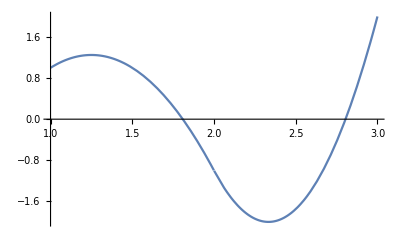

```mathematica
Plot[Which[1≤x≤2,1+2 (-1+x)-4 (-1+x)^2,2≤x≤3,-1-6 (-2+x)+9 (-2+x)^2],{x,1,3}]
```

## 13.- En ocasiones es difícil encontrar la solución de una ecuación diferencial. Sin embargo, es frecuente conocer el valor de la función en un punto, y usando la ecuación diferencial podríamos encontrar el valor de las derivadas de la función desconocida en ese punto. Calcular el polinomio de Taylor de grado 3 en el punto 1 de la función y(x) solución de la ecuación diferencial y’ = x+y+1 con la condición inicial y(1)=2. Enero 23

Solución:
El polinomio de Taylor de grado 3 de una función f(x) en el punto x_0 es f(x_0) + f ‘ (x_0) (x-x_0) + (f''(x_0))/(2!)(x-x_0)^2+ (f'''(x_0))/(3!)(x-x_0)^3
En este caso x_0=1. La función y(x) en ese punto vale 2.

Para las derivadas, aunque desconocemos la función y(x), podemos usar la ecuación diferencial: 
y’(x)=x+y(x)+1 llegamos a que y’(1)=1+y(1)+1=1+2+1=4.

Derivando en la ecuación diferencial y’’(x) = 1+y’(x) = 1+x+y(x)+1 luego y’’(1) = 1+1+y(1)+1=5
Derivando otra vez, y’’’=0+1+y’+0 = 1+x+y+1 luego y’’’(1) = 1+1+y(1)+1 = 5

El polinomio de Taylor pedido es: p(x) = 2 + 4 (x-1) + 5/(2!)(x-1)^2+ 5/(3!)(x-1)^3 = 2 + 5 (x-1) + 5/2(x-1)^2+ 5/6 (x-1)^3

```mathematica
y[1]=2
```

2

```mathematica
y'[x_]:=x+y[x]+1
```

```mathematica
y''[x]
```

y''[x]

## 10.- Calcula el polinomio de P_4 que interpola f(1)=1, f ‘(1)=2, f (2)=-1, f(3)=2, f ‘(3)=1. Enero 23

Solución:
Utilizando la idea de Newton, podríamos escribir el polinomio en la forma 
		p(x) = a + b (x-1) + c (x-1)^2 + d  (x-1)^2(x-2) + e (x-1)^2(x-2)(x-3).
Los coeficientes a, b, c, d y e se pueden calcular sustituyendo los datos. Así encontraríamos primero a, y sucesivamente, b, c, d y e.

También podemos utilizar la ley de recurrencia de las diferencias divididas. 
p(x) = f[1] + f[1,1] (x-1) + f[1,1,2] (x-1)^2 + f[1,1,2,3] (x-1)^2(x-2) +  f[1,1,2,3,3] (x-1)^2(x-2)(x-3)

f(1) = f[1] = 1, 	f[1,1] = f’[1] =2 ,  					f[1,1,2] = (f[1,2]-f[1,1])/(2-1) = (-2-2)/1 = -4, 	
f(1) = f[1] = 1, 	f[1,2] = (f[2]-f[1])/(2-1)=-2				f[1,2,3] = (f[2,3]-f[1,2])/(3-1) = (3+2)/2 = 5/2
f(2) = f[2] = -1, 	f[2,3] = (f[3]-f[2])/(3-2) = 3			f[2,3,3] = (f[3,3]-f[2,3])/(3-2) = (1-3)/1=-2
f(3) = f[3] = 2, 	f[3,3] = f’[3] = 1 
f(3) = f[3] = 2

f[1,1,2] = -4, 	f[1,1,2,3]=(f[1,2,3]-f[1,1,2])/(3-1)=(5/2-(-4))/2=13/4,	 f[1,1,2,3,3]=(f[1,2,3,3]-f[1,1,2,3])/(3-1)=(-9/4-13/4)/2=-22/8=-11/4
f[1,2,3] = 5/2	f[1,2,3,3]=(f[2,2,3]-f[1,2,3])/(3-1)=(-2-5/2)/2=-9/4
f[2,3,3] = -2

El polinomio que interpola es:
p(x) = 1 + 2 (x-1) -4 (x-1)^2 + (13/4) (x-1)^2(x-2) +  (-11/4) (x-1)^2(x-2)(x-3)

Con el Mathematica:

```mathematica
InterpolatingPolynomial[{{1,1,2},{2,-1},{3,2,1}},x]
```

1+(2+(-4+(13/4-11/4 (-3+x)) (-2+x)) (-1+x)) (-1+x)

## 12.- Calcula el polinomio de ℙ_4 que interpola f(0)=1, f (-1)=2, f(1)=2, f ‘(0)=3, f ‘’(0)=2. Octubre 22, Octubre 21

Solución:
En primer lugar ordenamos los datos, agrupándolos por el punto correspondiente.
 f(0)=1, f ‘(0)=3, f ‘’(0)=2,f (-1)=2, f(1)=2 .
Utilizando la idea de Newton, podríamos escribir el polinomio en la forma 
		p(x) = a + b (x-0) + c (x-0)^2 + d  (x-0)^3 + e (x-0)^3(x+1)
Los coeficientes a, b, c, d y e se pueden calcular sustituyendo los datos. Así encontraríamos primero a, y sucesivamente, b, c, d y e.

También podemos utilizar la ley de recurrencia de las diferencias divididas. 
p(x) = f[0] + f[0,0] (x-0) + f[0,0,0] (x-0)^2 + f[0,0,0,-1] (x-0)^3 +  f[0,0,0,-1,1] (x-0)^3(x+1)

f(0) = f[0] = 1, 	f[0,0] = f’(0) =3,  							f[0,0,0] = f’’(0)/2!= 2/2=1, 	
f(0) = f[0] = 1, 	f[0,0] = f’(0) =3,								f[-1,0,0] = (f[-1,0]-f[0,0])/(-1-0) = (-1-3)/(-1) =4
f(0) = f[0] = 1, 	f[-1,0] = (f[-1]-f[0])/(-1-0) = (2-1)/(-1)=-1			f[1,-1,0] = (f[1,-1]-f[-1,0])/(1-0) = (0-(-1))/1=1
f(-1) = f[-1] = 2, 	f[1,-1] = (f[1]-f[-1])/(1-(-1)) = (2-2)/(1-(-1))=0 
f(1) = f[1] = 2

f[0,0,0] = 1, 	f[-1,0,0,0]=(f[-1,0,0]-f[0,0,0])/((-1)-0)=(4-1)/(-1)=-3,	 f[1,-1,0,0,0]=(f[1,-1,0,0]-f[-1,0,0,0])/(1-0)=(-3-(-3))/1=0
f[-1,0,0] = 4	f[1,-1,0,0]=(f[1,-1,0]-f[-1,0,0])/(1-0)=(1-4)/1=-3
f[1,-1,0] = 1

El polinomio que interpola es:
p(x) = 1 + 3 (x-0) + 1 (x-0)^2 -3  (x-0)^3 +0* (x-0)^3(x+1)= 1 + 3x +  x^2 - 3  x^3

Con el Mathematica:

```mathematica
InterpolatingPolynomial[{{0,1,3,2},{-1,2},{1,2}},x]
```

1+x (3+(1-3 x) x)

```mathematica
Collect[%,x]
```

1+3 x+x^2-3 x^3

## 14.- Calcular el polinomio de Taylor de grado 3 de la función f(x)=√(x+1) en el punto 0. Octubre 22

Solución:
El polinomio de Taylor de grado 3 de una función f(x) en el punto x_0 es f(x_0) + f ‘ (x_0) (x-x_0) + (f''(x_0))/(2!)(x-x_0)^2+ (f'''(x_0))/(3!)(x-x_0)^3
En este caso x_0=0. La función es f(x)=√(x+1) . Calculamos las derivadas
f(x) = (x+1)^(1/2)
f ’(x)= (1/2) (x-1)^(1/2-1) = (1/2) (x+1)^(-1/2)
f’’(x) = -(1/4) (x+1)^(-3/2)
f’’’(x) = (3/8) (x+1)^(-5/2)

f(0) = 1
f ‘(0)= (1/2) 
f’’(1) = -(1/4) 
f’’’(1) = (3/8)

El polinomio de Taylor es: p(x) = 1 + (1/2) (x-0) - (1/4)/(2!)(x-0)^2+ (3/8)/(3!)(x-0)^3 = 1 + x/2 - 1/8x^2+ 1/16 x^3. 

Con el Mathematica

```mathematica
f[x_]:= √(x+1)
```

```mathematica
f[0]+f'[0](x-0)+f''[0]/(2!)(x-0)^2 + f'''[0]/(3!)(x-0)^3
```

1+x/2-x^2/8+x^3/16

## 13.- Calcula el polinomio de P_4 que interpola a la función |x| en los puntos -2, -1, 0, 1, 2. Julio 22

Solución:
Se trata de interpolar los valores de la función valor absoluto en los puntos dados. (-2,2), (-1,1), (0,0), (1,1), (2,2)

Utilizando la idea de Newton, podríamos escribir el polinomio en la forma 
		p(x) = a + b (x+2) + c (x+2) (x+1) + d (x+2)(x+1)x+ e (x+2)(x+1)x(x-1).
Los coeficientes a, b, c, d y e se pueden calcular sustituyendo los datos. Así encontraríamos primero a, y sucesivamente, b, c, d y e.

También podemos utilizar la ley de recurrencia de las diferencias divididas. 
p(x) = f[-2] + f[-2,-1] (x+2) + f[-2,-1,0] (x+2) (x+1) + f[-2,-1,0,1] (x+2)(x+1)x + f[-2,-1,0,1,2] (x+2)(x+1)x(x-1)

f(-2) = f[-2] = 2, f[-2,-1] = (f[-1]-f[-2])/(-1+2) = (1-2)/(-1+2)=-1 ,  	f[-2,-1,0] = (f[-1,0]-f[-2,-1])/(0+2) = (-1+1)/2 = 0, 	
f(-1) = f[-1] = 1, f[-1,0] = (0-1)/(0+1) = -1,					f[-1,0,1] = (1+1)/(1+1)=1						
f(0) = f[0] = 0,    f[0,1] = (1-0)/(1-0)=1						f[0,1,2] = (1-1)/(2-0)=0
f(1) = f[1] = 1,    f[1,2] = (2-1)/(2-1)=1
f(2) = f[2] = 2

f[-2,-1,0,1]=(f[-1,0,1]-f[-2,-1,0])/(1-(-2))=(1-0)/(1+2)=1/3	f[-2,-1,0,1,2]=(f[-1,0,1,2]-f[-2,-1,0,1])/(2-(-2))=(-1/3-1/3)/4 = -1/6
f[-1,0,1,2]=(0-1)/(2+1)=-1/3


El polinomio que interpola es:
p(x) = f[-2] + f[-2,-1] (x+2) + f[-2,-1,0] (x+2) (x+1) + f[-2,-1,0,1] (x+2)(x+1)x + f[-2,-1,0,1,2] (x+2)(x+1)x(x-1) =
 2 -1 (x+2) + 0 (x+2) (x+1) + (1/3) (x+2)(x+1)x + (-1/6) (x+2)(x+1)x(x-1)= -x + (1/3) (x+2)(x+1)x + (-1/6) (x+2)(x+1)x(x-1)

## 14.- Calcular el polinomio de Taylor de grado 3 de la función f(x)= Log[x] en el punto 1. Utilizarlo para dar una aproximación del Log[2]. Julio 22, Febrero 21

Solución:
El polinomio de Taylor de grado 3 de una función f(x) en el punto x_0 es f(x_0) + f ‘ (x_0) (x-x_0) + (f''(x_0))/(2!)(x-x_0)^2+ (f'''(x_0))/(3!)(x-x_0)^3
En este caso x_0=1, f(x)=Log (x) , f ‘(x)= 1/x = x^-1,  f ‘’(x)= - 1 x^-2, f ‘’’(x)= 2  x^-3. En el punto 1, la función y derivadas valen:
f(1) = 0, f ‘(1) = 1, f ‘’(1) = -1, f ‘’’(1) = 2.

El polinomio de Taylor pedido es: p(x) = (x-1) - 1/2 (x-1)^2+ 2/(3!)(x-1)^3
Para aproximar el Log[2], f(2), evaluamos el polinomio en el punto 2, p(2)=(2-1) - 1/2 (2-1)^2+ 2/(3!)(2-1)^3 =1 - 1/2 + 1/3 = (6-3+2)/6=5/6 = 0.8333

```mathematica
f[x_]:=Log[x]
```

```mathematica
∑_(i=0)^3 ((D[f[y],{y,i}]/.{y->1})(x-1)^i/(i!))
```

-1-1/2 (-1+x)^2+1/3 (-1+x)^3+x

```mathematica
%/.x->2
```

5/6

```mathematica
N[%]
```

0.833333

## 13.- Calcular el polinomio de P_4 que interpola f(0)=0, f(2)=2, f ‘(2)=-1, f’’(2)=2, f(3)=4. Enero 22

Solución:
Utilizando la idea de Newton, podríamos escribir el polinomio en la forma 
		p(x) = a + b (x-0) + c (x-0) (x-2) + d (x-0) (x-2)^2+ e (x-0)(x-2)^3.
Los coeficientes a, b, c, d y e se pueden calcular sustituyendo los datos. Así encontraríamos primero a, y sucesivamente, b, c, d y e.

También podemos utilizar la ley de recurrencia de las diferencias divididas. 
p(x) = f[0] + f[0,2] (x-0) + f[0,2,2] (x-0) (x-2) + f[0,2,2,2] (x-0) (x-2)^2+ f[0,2,2,2,3] (x-0) (x-2)^3

f(0) = f[0] = 0, f[0,2] = (f[2]-f[0])/(2-0) = (2-0)/(2-0)=1 ,  	f[0,2,2] = (f[2,2]-f[0,2])/(2-0) = (-1-1)/2 = -1, 	
f(2) = f[2] = 2, f[2,2] = f ‘(2) = -1,						f[2,2,2] = f’’(2)/2! = 2/2 = 1
f(2) = f[2] = 2, f[2,2] = f’(2) = -1						f[2,2,3] = (f[2,3]-f[2,2])/(3-2) = (2-(-1))/1=3
f(2) = f[2] = 2, f[2,3] = (f[3]-f[2])/(3-2) = (4-2)/(3-2) = 2
f(3) = f[3] = 4

f[0,2,2] = -1, 	f[0,2,2,2]=(f[2,2,2]-f[0,2,2])/(2-0)=(1-(-1))/2=1,	 f[0,2,2,2,3]=(f[2,2,2,3]-f[0,2,2,2])/(3-0)=(2-1)/3=1/3
f[2,2,2] = 1	f[2,2,2,3]=(f[2,2,3]-f[2,2,2])/(3-2)=(3-1)/1=2
f[2,2,3] = 3

El polinomio que interpola es:
p(x) = 0 + 1 (x-0) + (-1) (x-0) (x-2) + 1 (x-0) (x-2)^2+ (1/3) (x-0) (x-2)^3 = x - x(x-2) + x (x-2)^2+ (1/3) x (x-2)^3

Con el Mathematica:

```mathematica
InterpolatingPolynomial[{{0,0},{2,2,-1,2},{3,4}},x]
```

(1+(-1+(1+1/3 (-2+x)) (-2+x)) (-2+x)) x

## 14.- Calcular el polinomio de Taylor de grado 3 de la función f(x)= x^(1/3) en el punto 1. Utilizarlo para aproximar la raíz cúbica de 2. Enero 22

Solución:
El polinomio de Taylor de grado 3 de una función f(x) en el punto x_0 es f(x_0) + f ‘ (x_0) (x-x_0) + (f''(x_0))/(2!)(x-x_0)^2+ (f'''(x_0))/(3!)(x-x_0)^3
En este caso x_0=1, f(x)=x^(1/3) = x^(1/3), f ’(x)= (1/3) x^(-2/3), f ‘‘(x)= (-2/9) x^(-5/3), f ‘’‘(x)= (10/27) x^(-8/3). En el punto 1, la función y derivadas valen:
f(1)=1, f ‘(1) = 1/3, f ‘’(1) = -2/9, f ‘’’(1) = 10/27.

El polinomio de Taylor pedido es: p(x) = 1 + (1/3) (x-1) - 2/18(x-1)^2+ 10/162(x-1)^3
Para aproximar la raíz cúbica de 2, f(2), evaluamos el polinomio en el punto 2, p(2)=1 + (1/3) - 1/9 + 5/81 = (81+27-9+5)/81=104/81
Con el Mathematica,

```mathematica
f[x_]:=x^(1/3)
```

```mathematica
∑_(i=0)^3 ((D[f[y],{y,i}]/.{y->1})(x-1)^i/(i!))
```

1+1/3 (-1+x)-1/9 (-1+x)^2+5/81 (-1+x)^3

```mathematica
%/.x->2
```

104/81

```mathematica
p[2]
```

104/81

## 14.- Calcular el polinomio de Taylor de grado 3 de la función f(x)=√(x-2) en el punto 3. Octubre 21

Solución:
El polinomio de Taylor de grado 3 de una función f(x) en el punto x_0 es f(x_0) + f ‘ (x_0) (x-x_0) + (f''(x_0))/(2!)(x-x_0)^2+ (f'''(x_0))/(3!)(x-x_0)^3
En este caso x_0=3. La función f(x)=√(x-2) . Calculamos las derivadas
f(x) = (x-2)^(1/2)
f ’(x)= (1/2) (x-2)^(1/2-1) = (1/2) (x-2)^(-1/2)
f’’(x) = -(1/4) (x-2)^(-3/2)
f’’’(x) = (3/8) x^(-5/2)

f(3) = 1
f ‘(3)= (1/2) 
f’’(3) = -(1/4) 
f’’’(3) = (3/8)

El polinomio de Taylor es: p(x) = 1 + (1/2) (x-3) - (1/4)/(2!)(x-3)^2+ (3/8)/(3!)(x-1)^3 = 1 + (x-3)/2 - 1/8(x-3)^2+ 1/16 (x-3)^3 .

Con el Mathematica

```mathematica
f[x_]:= √(x-2)
```

```mathematica
f[3]+f'[3](x-3)+f''[3]/(2!)(x-3)^2 + f'''[3]/(3!)(x-3)^3
```

1+1/2 (-3+x)-1/8 (-3+x)^2+1/16 (-3+x)^3

## 12.- Calcula el polinomio de P_3 que interpola f(1) = 1, f(2) = 2, f (3)= -1, f ‘(3) = 3. Junio 21

Solución:
Utilizando la idea de Newton, podríamos escribir el polinomio en la forma 
		p(x) = a + b (x-1) + c (x-1) (x-2) + d (x-1) (x-2) (x-3).
Los coeficientes a, b, c y d se pueden calcular sustituyendo los datos. Así encontraríamos primero a, y sucesivamente, b, c y d.

También podemos utilizar la ley de recurrencia de las diferencias divididas. 
p(x) = f[1] + f[1,2] (x-1) + f[1,2,3] (x-1) (x-2) + f[1,2,3,3] (x-1) (x-2)(x-3)

f(1) = f[1] = 1,  f[1,2] = (f[2]-f[1])/(2-1) = 1 ,  	f[1,2,3] = (f[2,3]-f[1,2])/(3-1) = (-3-1)/2 = -2, 	f[1,2,3,3]=(f[2,3,3]-f[1,2,2])/(3-1)=(6-(-2))/2=4
f(2) = f[2] = 2,  f[2,3] = (f[3]-f[2])/(3-2) = -3,	f[2,3,3] = (f[3,3]-f[2,3])/(3-2) = (3-(-3))/(3-2)=6
f(3) = f[3] = -1, f[3,3] = f ’(3)= 3
f(3) = f[3] = -1

El polinomio que interpola es p(x) =  1 + 1 (x-1) - 2 (x-1) (x-2) + 4  (x-1) (x-2) (x-3) = -28+51 x -26 x^2 + 4 x^3

## 14.- Calcular el polinomio de Taylor de grado 2 de la función f(x)= x^(1/3) en el punto 1. Utilizarlo para aproximar 2^(1/3). Junio 21

Solución:
El polinomio de Taylor de grado 2 de una función f(x) en el punto x_0 es f(x_0) + f ‘ (x_0) (x-x_0) + (f''(x_0))/(2!)(x-x_0)^2
En este caso x_0=1, f(x)=x^(1/3) = x^(1/3), f ’(x)= (1/3) x^(-2/3), f ‘‘(x)= (-2/9) x^(-5/3). En el punto 1, la función y derivadas valen:
f(1)=1, f ‘(1) = 1/3, f ‘’(1) = -2/9.

El polinomio de Taylor pedido es: p(x) = 1 + (1/3) (x-1) - 2/18(x-1)^2

Para aproximar la raíz cúbica de 2, es decir, f(2), evaluamos el polinomio en el punto 2, p(2)=1 + (1/3) - 2/18 = (18+6-2)/18=22/18= 11/9

## 12.- Calcula el polinomio de P_3 que interpola f(1) = 1, f(2) = 2, f ‘(2)= -1, f ‘’(2) = 3. Febrero 21

Solución:
Utilizando la idea de Newton, podríamos escribir el polinomio en la forma 
		p(x) = a + b (x-1) + c (x-1) (x-2) + d (x-1) (x-2) (x-2).
Los coeficientes a, b, c y d se pueden calcular sustituyendo los datos. Así encontraríamos primero a, y sucesivamente, b, c y d.

También podemos utilizar la ley de recurrencia de las diferencias divididas. 
p(x) = f[1] + f[1,2] (x-1) + f[1,2,2] (x-1) (x-2) + f[1,2,2,2] (x-1) (x-2)(x-2)

f(1) = f[1] = 1, 	f[1,2] = (f[2]-f[1])/(2-1) = 1 ,  	f[1,2,2] = (f[2,2]-f[1,2])/(2-1) = (-1-1)/1 = -2, 	f[1,2,2,2]=(f[2,2,2]-f[1,2,2])/(2-1)=((3/2)-(-2))/1=7/2
f(2) = f[2] = 2, 	f[2,2] = f’(2) = -1,			f[2,2,2] = f’’(2)/2! = 3/2
f(2) = f[2] = 2, 	f[2,2] = f ’(2)= -1
f(2) = f[2] = 2

El polinomio que interpola es p(x) =  1 + 1 (x-1) - 2 (x-1) (x-2) + (7/2)  (x-1) (x-2) (x-2) = -18+35 x -39/2 x^2 + 7/2 x^3
Con el Mathematica:

```mathematica
InterpolatingPolynomial[{{1,1},{2,2,-1,3}},x]
```

1+(1+(-2+7/2 (-2+x)) (-2+x)) (-1+x)

```mathematica
Collect[%,x]
```

-18+35 x-(39 x^2)/2+(7 x^3)/2

## 14.- Calcular el polinomio de Taylor de grado 3 de la función f(x)= √x en el punto 1. Utilizarlo para aproximar la raíz cuadrada de 2. Enero 21

Solución:
El polinomio de Taylor de grado 3 de una función f(x) en el punto x_0 es f(x_0) + f ‘ (x_0) (x-x_0) + (f''(x_0))/(2!)(x-x_0)^2+ (f'''(x_0))/(3!)(x-x_0)^3
En este caso x_0=1, f(x)=√x = x^(1/2), f ’(x)= (1/2) x^(-1/2), f ‘‘(x)= (-1/4) x^(-3/2), f ‘’‘(x)= (3/8) x^(-5/2). En el punto 1, la función y derivadas valen:
f(1)=1, f ‘(1) = 1/2, f ‘’(1) = -1/4, f ‘’’(1) = 3/8.

El polinomio de Taylor pedido es: p(x) = 1 + (1/2) (x-1) - 1/8(x-1)^2+ 1/16(x-1)^3
Para aproximar la raíz cuadrada de 2, f(2), evaluamos el polinomio en el punto 2, p(2)=1 + (1/2) - 1/8 + 1/16 = (16+8-2+1)/16=23/16

## 12.- Calcula el polinomio de P_3 que interpola f(1)=1, f(2)=2, f ‘(2)=-1, f(3)=2. Enero 21

Solución:
Utilizando la idea de Newton, podríamos escribir el polinomio en la forma 
		p(x) = a + b (x-1) + c (x-1) (x-2) + d (x-1) (x-2)^2.
Los coeficientes a, b, c y d se pueden calcular sustituyendo los datos. Así encontraríamos primero a, y sucesivamente, b ,c y d.

También podemos utilizar la ley de recurrencia de las diferencias divididas. 
p(x) = f[1] + f[1,2] (x-1) + f[1,2,2] (x-1) (x-2) + f[1,2,2,3] (x-1) (x-2)^2

f(1) = f[1] = 1, f[1,2] = (f[2]-f[1])/(2-1) = 1 ,  	f[1,2,2] = (f[2,2]-f[1,2])/(2-1) = (-1-1)/1 = -2, 	f[1,2,2,3]=(f[2,2,3]-f[1,2,2])/(3-1)=(1-(-2))/2=3/2
f(2) = f[2] = 2, f[2,2] = f ’(2) = -1,		f[2,2,3] = (f[2,3]-f[2,2])/(3-2) = (0-(-1))/1=1
f(2) = f[2] = 2, f[2,3] = (f[3]- f[2])/(3-2) = 0
f(3) = f[3] = 2

El polinomio que interpola es p(x) =  1 + 1 (x-1) - 2 (x-1) (x-2) + 3/2  (x-1) (x-2)^2=10+19 x-(19 x^2)/2+(3 x^3)/2

## 11.- Calcula el polinomio de P_3 que interpola f(0)=1, f(1)=3, f(2)=6, f(3)=10 mediante el método de las diferencias divididas. Enero 20

Solución:
(0,1)     (3-1)/(1-0)=2      (3-2)/(2-0)=1/2    (1/2-1/2)/(3-0)=0
(1,3)     (6-3)/(2-1)=3      (4-3)/(3-1)=1/2
(2,6)     (10-6)/(3-2)=4
(3,10)
p(x) = 1 + 2 (x-0) + 1/2 (x-0)(x-1) + 0 (x-0)(x-1)(x-2) = 1 + 2x  + x^2/2-x/2 = 1+ 3x/2 + x^2/2

## 12.-Calcular el polinomio de Taylor de grado 5 de la función f(x) = cos(x-1) en el punto 1. Enero 20

Solución:
f(x)=cos(x-1), f’(x)=-sen(x-1), f’’(x)=-cos(x-1), f’’’(x)=sen(x-1), f’’’’(x)=cos(x-1), f’’’’’(x)=-sen(x-1)
f(1)=1, f’(1)=0, f’’(1)=-1, f’’’(1)=0, f’’’’(1)=1, f’’’’’(1)=0.
p(x)=1-(x-1)^2/2+(x-1)^4/24

## 6.- Los datos siguientes representan el crecimiento bacterial en un cultivo líquido durante cierto número de días Día | 0 | 4 | 8 | 12 | 16 | 20 Cantidad | 75 | 96 | 110 | 137 | 161 | 197 Usar el polinomio de interpolación para aproximar la cantidad de bacterias que había los días 7 y 14. Polinomio: 75+(21/4+(-7/32+(5/96+(-3/512+(67 (-16+x))/122880) (-12+x)) (-8+x)) (-4+x)) x = 75+(1607 x)/120-(695 x^2)/192+(255 x^3)/512-(85 x^4)/3072+(67 x^5)/122880 Bacterias día 7: 104.932 Bacterias día 14: 149.949 Enero 20. Aula de Informática

```mathematica
InterpolatingPolynomial[{{0,75},{4,96},{8,110},{12,137},{16,161},{20,197}},x]
```

75+(21/4+(-7/32+(5/96+(-3/512+(67 (-16+x))/122880) (-12+x)) (-8+x)) (-4+x)) x

```mathematica
p[x_]:=75+(21/4+(-7/32+(5/96+(-3/512+(67 (-16+x))/122880) (-12+x)) (-8+x)) (-4+x)) x
```

```mathematica
Collect[p[x],x]
```

75+(1607 x)/120-(695 x^2)/192+(255 x^3)/512-(85 x^4)/3072+(67 x^5)/122880

```mathematica
p[7]//N
```

104.932

```mathematica
p[14]//N
```

149.949

## 11.- Calcula el polinomio de P_4 que interpola f(0)=2, f ‘(0)=1, f’’(0)=2, f(2)=3, f ‘(2)=2. Enero 19

Solución:
El polinomio de interpolación escrito en la forma de Newton será
	p(x) = A + B x + C x^2+ D x^3+ E x^3(x-2).
Ahora podemos imponer las condiciones de interpolación o aplicar la fórmula de las diferencias divididas.
Si imponemos las condiciones de interpolación:
	p(0)=2 = A
	p’(0)=1=B
	p’’(0)=2=2C
Con esto tenemos p(x) = 2 + x + x^2+ D x^3+ E x^3(x-2).
	p(2)=3=2+2+4+8D; D=-5/8
Tenemos que p(x) = 2 + x + x^2 -5/8 x^3+ E x^3(x-2).
	p’(x)= 1 + 2 x - 15/8 x^2 + E (4x^3- 6 x^2)
	p’(2)= 2 = 1 + 4 - 15/2 + 8 E ⟹ 9/2= 8E, E=9/16
	p(x) = 2 + x + x^2 -5/8 x^3+ 9/16 x^3(x-2).

## 12.- Calcular el polinomio de Taylor de grado 3 de la función f(x)=√(1 + x) en el punto x=0. Enero 19

Solución:
El polinomio de Taylor debe valer igual que la función en el punto 0 y también sus derivadas (en este caso hasta la tercera).

p(x) = f(0)+f ‘(0) (x-0) + f ‘’(0)(x-0)^2/(2!) + f ‘’’(0)(x-0)^3/(3!) 
f(x)=√(1 + x), f ‘(x)= 1/(2 √(1 + x)), f ‘’(x)=-1/(4 (1+x)^(3/2)), f ‘’’(x)=3/(8 (1+x)^(5/2))
f(0) = 1, f ‘(0) = 1/2, f ‘’(0) = -1/4, f ‘’’(0) = 3/8

p(x) = 1 + 1/2 x  -1/4x^2/(2!) + 3/8x^3/(3!) =1 + x/2 - x^2/8 + x^3/16

## 12.- Calcula el polinomio de P_3 que interpola f(1)=1, f ‘(1)=2, f(2)=1, f ‘(2)=-1. Octubre 18, Julio 18

Solución:
Utilizando la idea de Newton, podríamos escribir el polinomio en la forma 
		p(x) = a + b (x-1) + c (x-1)^2 + d (x-1)^2(x-2).
Los coeficientes a, b, c y d se pueden calcular sustituyendo los datos. Así encontraríamos primero a, y sucesivamente, b ,c y d.

También podemos utilizar la ley de recurrencia de las diferencias divididas. 
p(x) = f[1] + f[1,1] (x-1) + f[1,1,2] (x-1)^2 + f[1,1,2,2] (x-1)^2 (x-2)

f(1) = f[1] = 1, f[1,1] = f’(1)=2 ,  						f[1,1,2] = (f[1,2]-f[1,1])/(2-1) = (0-2)/(2-1) = -2, 	f[1,1,2,2]=(f[1,2,2]-f[1,1,2])/(2-1)=(-1-(-2))/1=1
f(1) = f[1] = 1, f[1,2] = (f[2]-f[1])/(2-1) = (1-1)/(2-1)=0,	f[1,2,2] = (f[2,2]-f[1,2])/(2-1) = (-1-0)/1=-1
f(2) = f[2] = 1, f[2,2] = f’(2)= -1
f(2) = f[2] = 1

El polinomio que interpola es p(x) =  1 + 2 (x-1) -2 (x-1)^2 + 1 (x-1)^2(x-2)=1 + 2 (x-1) -2 (x-1)^2 +  (x-1)^2(x-2) = -5 + 11x - 6 x^2+ x^3

Con el Mathematica,

```mathematica
InterpolatingPolynomial[{{1,1,2},{2,1,-1}},x]
```

1+(2+(-4+x) (-1+x)) (-1+x)

```mathematica
Collect[%,x]
```

-5+11 x-6 x^2+x^3

## 14.- Calcular el polinomio de Taylor de grado 4 de la función f(x)=cos x en el punto 0. Octubre 18, Julio 18

Solución:
El polinomio de Taylor de grado 4 de una función f(x) en el punto x_0 es f(x_0) + f ‘ (x_0) (x-x_0) + (f''(x_0))/(2!)(x-x_0)^2+ (f'''(x_0))/(3!)(x-x_0)^3 +  (f''''(x_0))/(4!)(x-x_0)^4
En este caso x_0=0. La función f(x)= cos x . Calculamos las derivadas
f(x) = cos x
f ’(x)= - sen x
f’’(x) = - cos x 
f’’’(x) = sen x
f’’’’(x)=cos x

f(0) = 1
f ‘(0)= 0
f’’(0) = -1
f’’’(0) = 0
f’’’’(0)=1

El polinomio de Taylor es: p(x) = 1 + 0* (x-0) - 1/(2!)(x-0)^2+ 0/(3!)(x-0)^3 + 1/(4!)(x-0)^4= 1  - 1/2x^2+ 1/24x^4 .

Con el Mathematica

```mathematica
f[x_]:= Cos[x]
```

```mathematica
f[0]+f'[0](x-0)+f''[0]/(2!)(x-0)^2 + f'''[0]/(3!)(x-0)^3 + f''''[0]/(4!)(x-0)^4
```

1-x^2/2+x^4/24

## 12.- Calcula el polinomio de P_4 que interpola f(0)=1, f ‘(0)=2, f’’(0)=2, f(2)=3, f(3)=2. Enero 18

Solución:
El polinomio de interpolación escrito en la forma de Newton será
	p(x) = A + B x + C x^2+ D x^3+ E x^3(x-2).
Ahora podemos imponer las condiciones de interpolación o aplicar la fórmula de las diferencias divididas.
Si imponemos las condiciones de interpolación:
	p(0)=1 = A
	p’(0)=2=B
	p’’(0)=2=2C
Con esto tenemos p(x) = 1 + 2 x + x^2+ D x^3+ E x^3(x-2).
	p(2)=3=1+4+4+8D; D=-6/8=-3/4
	p(3)=2= 1 + 6 + 9 + (-3/4)  27+ E 27; 2-16+81/4 = 27E;  25/4 = 27E; E=25/108
	
	 p(x) = 1 + 2 x + x^2 -(3/4) x^3+ (25/108) x^3(x-2).

## 14.- Calcular el polinomio de Taylor de grado 5 de la función f(x)=sen x en el punto 0. Enero 18

Solución:
El polinomio de Taylor debe valer igual que la función en el punto 0 y también sus derivadas (en este caso hasta la quinta).

p(x) = f(0)+f ’(0) (x-0) + f ’’(0)(x-0)^2/(2!) + f ‘’’(0)(x-0)^3/(3!) + f ‘’’’(0)(x-0)^4/(4!) +f ‘’’’’(0)(x-0)^5/(5!) 
f(x)=sen x, f ’(x)= cos x, f ’’(x)=-sen x, f ‘’’(x)=-cos x, f ‘’’’(x)=sen x, f ‘’’’’(x) = cos x
f(0) = 0, f ‘(0) = 1, f ‘’(0) = 0, f ‘’’(0) = -1, f ‘’’’(0) = 0, f ‘’’’’(0) = 1

p(x) = x - x^3/(3!) + x^5/(5!) = x - x^3/6 + x^5/120

## Problemas de examen. Tema 12. Resolución numérica de ecuaciones no lineales.

## 11.- Para calcular la raíz cúbica de dos, consideramos la función f(x)= x^3-2, y aplicamos el método de Newton para resolver ecuaciones no lineales comenzando con el valor inicial x_0=2. Calcular las dos siguientes aproximaciones utilizando el método de Newton. Enero 23

Solución: 
La función f es polinómica. Por tanto, f es continua y derivable cuantas veces queramos en toda la recta real. Vamos a aplicar el método de Newton para aproximar las raíces de una ecuación comenzando con la aproximación inicial x_0=2.
El método de Newton, partiendo de una aproximación inicial, y considerando las rectas tangentes a la gráfica de la función, y los puntos donde las tangentes se anulan, va generando una sucesión de aproximaciones que se espera converja a un cero de la función. En concreto, los valores se obtienen mediante la fórmula:
x_(n+1)=x_n- f(x_n)/f'(x_n).

En nuestro caso, 
x_0=2, 
f(x) = x^3-2
f ’(x) = 3 x^2

x_1=x_0- f(x_0)/f'(x_0) = 2- f(2)/f'(2) = 2- 6/12= 3/2
x_2=x_1- f(x_1)/f'(x_1) = 3/2 - f(3/2)/f'(3/2) = 3/2 - ((3/2)^3-2)/(3(3/2)^2) = 3/2 - (11/8)/(27/4) = 3/2 - 11/54=81/54-11/54=70/54=35/27.

Con el Mathematica:

```mathematica
f[x_]:=x^3-2
```

```mathematica
x0=2;x1=x0-f[x0]/f'[x0];x2=x1-f[x1]/f'[x1];{x0,x1,x2}
```

{2,3/2,35/27}

## 11.- Dada la función f(x) = x^3+2x+1, ¿cuántas soluciones reales tiene exactamente la ecuación f(x)=0? Considerando el intervalo [-1,0] estudiar si podemos emplear el método de bisección para aproximar una solución de la ecuación f(x)=0 y, en caso afirmativo, realizar 3 divisiones del intervalo para aproximar la solución. Julio 22

Solución:
La función f es un polinomio, por tanto continua y derivable cuantas veces deseemos en toda la recta real. Además es un polinomio de grado impar, esto hace que tenga al menos una raíz (evaluando en números suficientemente grandes positivos y negativos, encontramos valores de distinto signo).
Por ejemplo, f(-2)= -8-4+1 <0, f(2) = 8+4+1 >0. Como f es una función continua en todo R, al cambiar de signo entre el -2 y el 2, el teorema de Bolzano nos dice que la función debe anularse en algún punto entre -2 y 2. 
La ecuación f(x)=0 tiene al menos una solución.

Para saber si hay más estudiamos la derivada de la función. f ’(x) = 3 x^2+2. La derivada es siempre positiva y nunca se anula, por tanto, por el teorema de Rolle, la función no puede anularse en dos puntos (pues si lo hiciese, la derivada debería anularse en un punto intermedio. Lo que no ocurre.)

La ecuación f(x)=0 tiene una única solución. 
Consideremos el intervalo [-1,0]. Veamos si podemos aplicar el método de bisección.
1) la función f es continua en [-1,0] (de hecho es continua en todo R).
2) la función cambia de signo en el intervalo [-1,0], f(-1)=-1-2+1<0, f(0)=1>0.
Podemos aplicar el método de bisección en el intervalo [-1,0].
a0=-1, b0=0, m0 = (a0+b0)/2 = -1/2, f(-1/2) = -1/8 -1+1<0. Por tanto, tenemos cambio de signo en el intervalo [-1/2,0].
a1=-1/2, b1=0, m1=(a1+b1)/2 = -1/4, f(-1/4)= -1/64-2/4+1 >0. Por tanto, tenemos cambio de signo en el intervalo [-1/2,-1/4].
a2=-1/2, b2=-1/4, m2= (a2+b2)/2=(-1/2-1/4)/2=-3/8, f(-3/8)= -27/512 - 6/8 + 1 = (-27-384+512)/512 >0. Por tanto, tenemos un cambio de signo en el intervalo [-1/2,-3/8].

## 4.- Realizar cuatro iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+ 2x + cos x -2=0 partiendo de x_0=0. El valor de x_4 con 10 cifras decimales es: 1) 0.3393167250, 2) 0.4988619908, 3) 0.5652441238, 4) 0.6443318729, 5) 0.8575419966 Enero 22. Aula de Informática.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=x^3+2x+Cos[x]-2
```

```mathematica
s=0;Do[s=s-f[s]/f'[s],{4}];Print["Una aproximación sería ",N[s,10]]
```

Una aproximación sería 0.4988619908

## 11.- Dada la función f(x) = x^3+2x-1, ¿cuántas soluciones tiene la ecuación f(x)=0? Comenzando con el valor aproximado x_0=0, calcular dos aproximaciones a una solución utilizando el método de Newton para resolver ecuaciones no lineales. Enero 22

Solución: 
La función f es polinómica. Por tanto, f es continua y derivable cuantas veces queramos en toda la recta real. Al ser de grado impar, toma signos opuestos al tender x a más  o menos infinito. En concreto, al tener el coeficiente líder positivo, cuando x → +∞, f(x) → +∞, mientras que cuando x → -∞, f(x) → -∞. De aquí obtenemos que f tomará valores positivos y valores negativos, y utilizando el teorema de Bolzano sabremos que f debe anularse en algún punto. Es decir, la ecuación f(x)=0 tiene al menos una solución. Para saber si hay más consideramos la derivada de la función f’(x)= 3 x^2+2 es siempre positiva y mayor que cero, por tanto f(x) será una función estrictamente creciente y no podrá anularse en más de un punto.

La ecuación f(x)= x^3+2x-1=0 tiene una sola solución.

Vamos a aplicar el método de Newton para aproximar las raíces de una ecuación comenzando con la aproximación inicial x_0=0.
El método de Newton, partiendo de una aproximación inicial, y considerando las rectas tangentes a la gráfica de la función, y los puntos donde las tangentes se anulan, va generando una sucesión de aproximaciones que se espera converja a un cero de la función. En concreto, los valores se obtienen mediante la fórmula:
x_(n+1)=x_n- f(x_n)/f'(x_n).

En nuestro caso, 
x_0=0, 
x_1=x_0- f(x_0)/f'(x_0) = 0- f(0)/f'(0) = - (-1)/2= 1/2
x_2=x_1- f(x_1)/f'(x_1) = 1/2 - f(1/2)/f'(1/2) = 1/2 - ((1/2)^3+2(1/2)-1)/(3(1/2)^2+2) = 1/2 - (1/8+1-1)/(3/4+2) = 1/2 - (1/8)/(11/4) = 1/2 - 1/22 = 10/22 = 5/11.

Con el Mathematica:

```mathematica
f[x_]:=x^3+2x-1
```

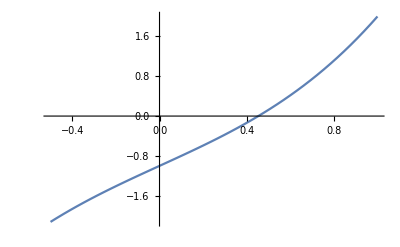

```mathematica
Plot[f[x],{x,-1/2,1}]
```

```mathematica
x0=0;x1=x0-f[x0]/f'[x0];x2=x1-f[x1]/f'[x1];{x0,x1,x2}
```

{0,1/2,5/11}

## 10.- Estudiar los intervalos de el crecimiento de la función f(x) = x^3+2x-3. ¿Cuántos ceros tiene? Evaluarla en -1 y 1. Aplicar el método de bisección 2 veces partiendo del intervalo [-1,1]. Junio 21

Solución:
La función f(x) = x^3+2x-3 es continua y derivable en toda la recta real (se trata de un polinomio). Para estudiar el crecimiento, calculamos su derivada; f ’(x) = 3x^2+2. Vemos que la derivada es siempre mayor que cero, por tanto la función es estrictamente creciente en toda la recta real. Al ser la derivada estrictamente positiva, la función es  estrictamente creciente, podría tener como mucho un cero. Para saber si tiene alguno, tratamos de buscar signos opuestos. Por ejemplo, si evaluamos en los puntos 0 y 2, obtenemos
f(0)=-3 <0
f(2)=8+4-3>0
Al haber cambio de signo, y la función continua en el intervalo [0,2], el teorema de  Bolzano nos dice que habrá al menos un punto donde se anula. Como es estrictamente creciente, como mucho hay un cero. Por tanto, f tiene un único cero y la ecuación  x^3+2x-3 =0 tiene una única solución.

Si evaluamos en los puntos propuestos -1 y 1.
f(-1)= -1-2-3 = -6 <0
f(1)=1+2-3 = 0
En el punto 1 hay un cero. Dado que la función es estrictamente creciente, solo tiene un cero.

Si quisiéramos aplicar el método de bisección para aproximar la solución de f(x)=0 partiendo del intervalo [-1,1], seguiríamos los siguientes pasos:
1) Se trata de una función continua en este intervalo (los polinomios están definidos y son funciones continuas en todo punto).
2) Comprobamos si hay cambio de signo en el intervalo inicial. Para ello evaluamos en los extremos:
	f(-1)=-6<0
	f(1)=0
Dado que en uno de los extremos del intervalo elegido la función se anula, hemos encontrado una solución de la ecuación 0 = x^3+2x-3, x=1.

Para utilizar el método de bisección necesitamos un intervalo donde se produzca cambio de signo de la función en los extremos.

## 4.- Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+2x+1=0 partiendo de x_0=-2. Escribir valor de x_5 con 10 cifras decimales: Febrero 21. Aula de Informática.

```mathematica
x0=-2;
```

```mathematica
h[x_]:=x^3+2x+1
```

```mathematica
x1=x0-h[x0]/h'[x0]
```

-17/14

```mathematica
x2=x1-h[x1]/h'[x1]
```

-6285/8813

```mathematica
x3=x2-h[x2]/h'[x2]
```

-1181027022047/2413366135369

```mathematica
x4=x3-h[x3]/h'[x3]
```

-17350907135779988805460449109686244055/38211180030994919512515279408659263181

```mathematica
N[x5,20]
```

-0.4533978931376927114

```mathematica
x5=x4-h[x4]/h'[x4]
```

-66239044616239855126316915726128640907368903089545413824501563678964999425360538850844095374347564515986327291491/146094734048805284309751253526702576567995747072754084953619010306042489581229845704427375937139418385247212205057

```mathematica
N[%,20]
```

-0.4533978931376927114

## 10.- Estudiar los intervalos de crecimiento de la función f(x) = x^3+2x+2. ¿Cuántos ceros tiene? Evaluarla en -1 y 1. Aplicar el método de bisección 2 veces partiendo del intervalo [-1,1]. Febrero 21

Solución: La función f(x) = x^3+2x+2 es continua y derivable en toda la recta real (se trata de un polinomio). Para estudiar el crecimiento, calculamos su derivada; f ’(x) = 3x^2+2. Vemos que la derivada es siempre mayor que cero, por tanto la función es estrictamente creciente en toda la recta real. Al ser la derivada estrictamente positiva, la función estrictamente creciente, podría tener como mucho un cero. Para saber si tiene alguno, tratamos de buscar signos opuestos. Por ejemplo, en los puntos propuestos -1 y 1.
f(-1)= -1-2+2=-1 <0
f(1)=1+2+2 = 5>0
Hay un cambio de signo, y por el teorema de  Bolzano, hay al menos un cero. Por tanto, concluimos que hay un solo cero, y que está entre -1 y 1.
Para aplicar el método de bisección, consideramos el punto medio del intervalo m= (-1+1)/2=0. 
Evaluamos en el punto medio, f(0)=2>0. Por tanto, el cambio de signo se produce en el intervalo [-1,0].
Volvemos a aplicar el método de bisección, m= (-1+0)/2=-1/2. Evaluamos f(-1/2)=(-1/2)^3+2(-1/2)+2 = 7/8 >0.
El cero de la función debe estar en el intervalo [-1,-1/2].

## 4.- Realizar cinco iteraciones por el método de la secante para aproximar la solución de la ecuación x^3+ x + 1 = 0 partiendo de x_0=-2, x_1=-1. Escribir x_5 con 10 cifras decimales. x_5= Enero 21. Aula de Informática.

```mathematica
Clear[f,x,a,b,c]
```

```mathematica
f[x_]:=x^3+x+1
```

```mathematica
a=-2;b=-1;Do[c=b; b=(a f[b]-b f[a])/(f[b]-f[a]); a=c;Print["Una aproximación sería ",N[b,10],". La función vale ",N[f[b],10]],{4}];
```

Una aproximación sería -0.875. La función vale -0.544921875

Una aproximación sería -0.7253218884. La función vale -0.1069078166

Una aproximación sería -0.6887893621. La función vale -0.01557224017

Una aproximación sería -0.6825607566. La función vale -0.0005584322777

## 4.- Realizar cuatro iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+2x+1=0 partiendo de x_0=-2. El valor de x_4 con 10 cifras decimales es: 1) -0.4540793328, 2) 0.4540792113, 3) -0.4540790157, 4) -0.4540796425, 5) -0.4540792217 Enero 21. Aula de Informática.

```mathematica
f[x_]:=x^3+2x+1
```

```mathematica
x0=-2;
```

```mathematica
x1=x0-f[x0]/f'[x0];
```

```mathematica
x2=x1-f[x1]/f'[x1];
```

```mathematica
x3=x2-f[x2]/f'[x2];
```

```mathematica
x4=x3-f[x3]/f'[x3];
```

```mathematica
N[x4,20]
```

-0.45407933284724094968

## 10.- Estudiar los intervalos de el crecimiento de la función f(x) = x^3+2x+1. ¿Cuántos ceros tiene? Evaluarla en -1 y 1. Aplicar el método de bisección 2 veces partiendo del intervalo [-1,1]. Enero 21

Solución: La función f(x) = x^3+2x+1 es continua y derivable en toda la recta real (se trata de un polinomio). Para estudiar el crecimiento, calculamos su derivada; f ’(x) = 3x^2+2. Vemos que la derivada es siempre mayor que cero, por tanto la función es estrictamente creciente en toda la recta real. Al ser la derivada estrictamente positiva, la función estrictamente creciente, podría tener como mucho un cero. Para saber si tiene alguno, tratamos de buscar signos opuestos. Por ejemplo, en los puntos propuestos -1 y 1.
f(-1)= -1-2+1=-2 <0
f(1)=1+2+1 = 4>0
Hay un cambio de signo, y por el teorema de  Bolzano, hay al menos un cero. Por tanto, concluimos que hay un solo cero, y que está entre -1 y 1.
Para aplicar el método de bisección, consideramos el punto medio del intervalo m= (-1+1)/2=0. 
Evaluamos en el punto medio, f(0)=1>0. Por tanto, el cambio de signo se produce en el intervalo [-1,0].
Volvemos a aplicar el método de bisección, m= (-1+0)/2=-1/2. Evaluamos f(-1/2)=(-1/2)^3+2(-1/2)+1 = - 1/8 <0.
El cero de la funcion debe estar en el intervalo [-1/2,0].

## 4.- Realizar cinco iteraciones por el método de la secante para aproximar la solución de la ecuación 8 x^2 - 9x + cos x=0 partiendo de x_0= -1, x_1=1/2. Escribir x_5 con 7 cifras decimales. Enero 20. Aula de Informática.

x_5= 0.141898529575

```mathematica
f[x_]:=8x^2-9x+Cos[x]
```

```mathematica
x0=-1; x1=1/2;
```

```mathematica
x2=x1-f[x1](x1-x0)/(f[x1]-f[x0]);
```

```mathematica
x3=x2-f[x2](x2-x1)/(f[x2]-f[x1]);
```

```mathematica
x4=x3-f[x3](x3-x2)/(f[x3]-f[x2]);
```

```mathematica
x5=x4-f[x4](x4-x3)/(f[x4]-f[x3]);
```

```mathematica
N[x5,12]
```

0.141898529575

## 9.- Para aproximar una solución real de la ecuación x^3-2x-1=0 realizar tres iteraciones del método de Newton-Raphson partiendo del valor inicial x_0=0. Enero 20

Solución:
f(x)=x^3-2x-1, x_(n+1)= x_n -f(x_n)/f’(x_n) = x_n-(x_n^3-2 x_n-1)/(3 x_n^2-2), 
x_0=0,
x_1= x_0-(x_0^3-2 x_0-1)/(3 x_0^2-2) =1/(-2) = -1/2
x_2=x_1-(x_1^3-2 x_1-1)/(3 x_1^2-2) = -1/2-(-1/8+1-1)/(3/4-2)=-1/2-(-1/8)/(-5/4)=-1/2-1/10=-6/10=-3/5
x_3=-3/5-(-27/125+6/5-1)/(3*9/25-2) =-3/5-(-27/125+150/125-125/125)/(135/125-250/125) =-3/5-(2/115)=-71/115

## 4.- Realizar cinco iteraciones por el método de la secante para aproximar la solución de la ecuación 8 x^2 - 9x + cos x=0 partiendo de x_0=1/2, x_1=2. Escribir x_5 con 7 cifras decimales. x_5=0.970644695525 Enero 20. Aula de Informática.

```mathematica
f[x_]:=8x^2-9x+Cos[x]
```

```mathematica
x0=1/2; x1=2;
```

```mathematica
x2=x1-f[x1](x1-x0)/(f[x1]-f[x0]);
```

```mathematica
x3=x2-f[x2](x2-x1)/(f[x2]-f[x1]);
```

```mathematica
x4=x3-f[x3](x3-x2)/(f[x3]-f[x2]);
```

```mathematica
x5=x4-f[x4](x4-x3)/(f[x4]-f[x3]);
```

```mathematica
N[x5,12]
```

0.970644695525

## 4.- Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+ 2x + cos x=0 partiendo de x_0=-2. Escribir x_5 con 12 cifras decimales. x_5= Enero 19. Aula de Informática.

Solución: Siguiendo la práctica de ecuaciones no lineales:

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:=x^3+2x+Cos[x]
```

```mathematica
x=-2;
Do[x=x-f[x]/f'[x];Print[N[x,12]],{5}];Print["Una aproximación sería ",N[x,15],". La función vale ",N[f[x],12]]
```

-1.16722119889

-0.663150544281

-0.452249271241

-0.420278167268

-0.419659987914

Una aproximación sería -0.419659987913863. La función vale -6.56047157627×10^-7

## 4.- Realizar cinco iteraciones por el método de la secante para aproximar la solución de la ecuación x^3+ x + 1 = 0 partiendo de x_0=-2, x_1=-1. Escribir x_5 con 10 cifras decimales. x_5= Enero 19. Aula de Informática.

```mathematica
Clear[f,x,a,b,c]
```

```mathematica
f[x_]:=x^3+x+1
```

```mathematica
a=-2;b=-1;Do[c=b; b=(a f[b]-b f[a])/(f[b]-f[a]); a=c;Print["Una aproximación sería ",N[b,10],". La función vale ",N[f[b],10]],{4}];
```

Una aproximación sería -0.875. La función vale -0.544921875

Una aproximación sería -0.7253218884. La función vale -0.1069078166

Una aproximación sería -0.6887893621. La función vale -0.01557224017

Una aproximación sería -0.6825607566. La función vale -0.0005584322777

## 4.- Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+ 2x + sen x +1 =0 partiendo de x_0=-2. Escribir x_5 con 12 cifras decimales. x_5= Enero 19. Aula de Informática.

Solución: Siguiendo la práctica de ecuaciones no lineales:

```mathematica
f[x_]:=x^3+2x+Sin[x]+1
```

```mathematica
x=-2;
Do[x=x-f[x]/f'[x];Print[N[x,12]],{5}];Print["Una aproximación sería ",N[x,12],". La función vale ",N[f[x],12]]
```

-1.12327545921

-0.54987916884

-0.340125668858

-0.323952953512

-0.323885621116

Una aproximación sería -0.323885621116. La función vale -3.68424462046×10^-9

## 4.- Realizar cinco iteraciones por el método de la secante para aproximar la solución de la ecuación x^3+ x + 1 = 0 partiendo de x_0=-2, x_1=-1. Escribir x_5 con 10 cifras decimales. x_5= Enero 19.Aula de Informática.

```mathematica
Clear[f,x,a,b,c]
```

```mathematica
f[x_]:=x^3+x+1
```

```mathematica
a=-2;b=-1;Do[c=b; b=(a f[b]-b f[a])/(f[b]-f[a]); a=c;Print["Una aproximación sería ",N[b,10],". La función vale ",N[f[b],10]],{4}];
```

Una aproximación sería -0.875. La función vale -0.544921875

Una aproximación sería -0.7253218884. La función vale -0.1069078166

Una aproximación sería -0.6887893621. La función vale -0.01557224017

Una aproximación sería -0.6825607566. La función vale -0.0005584322777

## 4.- Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+ 2x + cos x=0 partiendo de x_0=-2. Escribir x_5 con 12 cifras decimales. x_5= Enero 19. Aula de Informática.

Solución:
Siguiendo la práctica de ecuaciones no lineales:

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:=x^3+2x+Cos[x]
```

```mathematica
x=-2;
Do[x=x-f[x]/f'[x];Print[N[x,12]],{5}];Print["Una aproximación sería ",N[x,12],". La función vale ",N[f[x],12]]
```

-1.16722119889

-0.663150544281

-0.452249271241

-0.420278167268

-0.419659987914

Una aproximación sería -0.419659987914. La función vale -6.56047157627×10^-7

## 4.- Realizar cinco iteraciones por el método de la secante para aproximar la solución de la ecuación x^3+ x + 1 = 0 partiendo de x_0=-2, x_1=-1. Escribir x_5 con 10 cifras decimales. x_5= Enero 19. Aula de Informática.

```mathematica
Clear[f,x,a,b,c]
```

```mathematica
f[x_]:=x^3+x+1
```

```mathematica
a=-2;b=-1;Do[c=b; b=(a f[b]-b f[a])/(f[b]-f[a]); a=c;Print["Una aproximación sería ",N[b,10],". La función vale ",N[f[b],10]],{4}];
```

Una aproximación sería -0.875. La función vale -0.544921875

Una aproximación sería -0.7253218884. La función vale -0.1069078166

Una aproximación sería -0.6887893621. La función vale -0.01557224017

Una aproximación sería -0.6825607566. La función vale -0.0005584322777

## 4.- Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+ 2x + sen x +1 =0 partiendo de x_0=-2. Escribir x_5 con 12 cifras decimales. x_5= Enero 19. Aula de Informática.

Solución:
Siguiendo la práctica de ecuaciones no lineales:

```mathematica
f[x_]:=x^3+2x+Sin[x]+1
```

```mathematica
x=-2;
Do[x=x-f[x]/f'[x];Print[N[x,12]],{5}];Print["Una aproximación sería ",N[x,12],". La función vale ",N[f[x],12]]
```

-1.12327545921

-0.54987916884

-0.340125668858

-0.323952953512

-0.323885621116

Una aproximación sería -0.323885621116. La función vale -3.68424462046×10^-9

## 10.- Aproximar una solución de la ecuación x^2-2=0, aplicando el método de Newton a la función f(x) = x^2-2, con punto inicial x_0=1 y haciendo dos iteraciones. Octubre 18, Julio 18

Solución:
f(x)=x^2-2, x_(n+1)= x_n -f(x_n)/f’(x_n) = x_n-(x_n^2-2)/(2 x_n), 
x_0=1,
x_1= x_0-(x_0^2-2)/(2 x_0) = 1-(1^2-2)/(2*1) = 1-(-1)/2 = 3/2
x_2=x_1-(x_1^2-2)/(2 x_1) = (3/2)-((3/2)^2-2)/(2*(3/2))=3/2-(1/4)/3=3/2-1/12=17/12
Con el Mathematica

```mathematica
f[x_]:=x^2-2
```

```mathematica
x0=1;
```

```mathematica
x1=x0-f[x0]/f'[x0]
```

3/2

```mathematica
x2=x1-f[x1]/f'[x1]
```

17/12

## 4.- Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+x+M=0 partiendo de x_0=N. Escribir x_5 con 10 cifras decimales. x_5= Junio 18. Aula de Informática

```mathematica
Clear[ff]
```

```mathematica
m=7;n=2;
```

```mathematica
ff[x_]:=x^3+x+m
```

```mathematica
s=n;
Do[s=s-ff[s]/ff'[s];Print[N[s,15]],{5}];Print["Una aproximación sería ",N[s,15],". La función vale ",N[ff[s],10]]
```

0.692307692307692

-2.59914115011202

-1.98043732078654

-1.76518676095496

-1.73954766382636

Una aproximación sería -1.73954766382636. La función vale -0.00346425279

## 10.- Para aproximar las soluciones real de la ecuación x^3+x+1=0, considerar la función f(x) = x^3+x+1. ¿Es continua? ¿Es derivable? Evaluarla en -1 y 1. ¿Cuantas raíces tiene la ecuación? Aplicar el método de bisección 3 veces partiendo del intervalo [-1,1]. Enero 18

Solución:
La función f es continua en toda la recta real pues es un polinomio. También es derivable, pues es un polinomio. 
	f(-1)=-1-1+1=-1
	f(1)=1+1+1=3
Como el signo de la función f en -1 y en 1 son opuestos (siendo f continua; Teorema de Bolzano), la función se anula en algún punto entre -1 y 1. Por tanto, la ecuación tiene al menos una raíz. Para saber si tiene más, estudiamos la derivada de la función.
	f ’(x) = 3 x^2+1 
Vemos que la derivada de la función es siempre mayor que cero, la función es siempre estrictamente creciente y no puede tener más de un cero. Por tanto, hay una única solución de la ecuación y está entre -1 y 1.

Aplicamos ahora el método de bisección. Partimos del intervalo [-1,1] donde la función, que es continua, presenta cambio de signo y tiene por tanto una raíz.
	a_0= -1, b_0= 1, m_0= (a_0+b_0)/2= 0, f(a_0)=-1, f(b_0)=3, f(m_0)=1
Como en el punto medio la función tiene el mismo signo que en el extremo de la derecha reducimos el intervalo por esa parte
	a_1= -1, b_1= 0, m_1= (a_1+b_1)/2= -1/2, f(a_1)=-1, f(b_1)=1, f(m_1)=(-1/2)^3+(-1/2)+1=(-1/8)-(1/2)+1>0

Como en el punto medio la función tiene el mismo signo que en el extremo de la derecha reducimos el intervalo por esa parte
	a_2= -1, b_2= -1/2, m_2= (a_2+b_2)/2= -3/4, f(a_2)=-1, f(b_2)>0, f(m_2)=(-3/4)^3+(-3/4)+1=(-27/64)-(3/4)+1= (-27/64)-(48/64)+1=(-75/64)+1<0.
Como en el punto medio la función tiene el mismo signo que en el extremo de la izquierda, reducimos el intervalo por esa parte.
Tras tres pasos por el método de bisección hemos llegado a que la solución de la ecuación está en el intervalo [-3/4,-1/2].

## 4.- Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+x+1=0 partiendo de x_0=-2. Escribir x_5 con 20 cifras decimales. x_5= Enero 18. Aula de Informática.

Solución:
Seguimos lo que aparece en la Práctica de ECUACIONES NO LINEALES.

```mathematica
Clear[f]
```

```mathematica
f[x_]:=x^3+x+1
```

```mathematica
x=-2;
Do[x=x-f[x]/f'[x];Print[N[x,20]],{5}];Print["Una aproximación sería ",N[x,20],". La función vale ",N[f[x],15]]
```

-1.3076923076923076923

-0.89270864270864270864

-0.71453940099213945862

-0.68319313870858675011

-0.68232844296175089986

Una aproximación sería -0.68232844296175089986. La función vale -1.53182140397554×10^-6

## 4.- Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+x+1=0 partiendo de x_0=-3. Escribir x_5 con 20 cifras decimales. x_5= Enero 18. Aula de Informática.

Solución: Seguimos lo visto en prácticas.

```mathematica
Clear[f]
```

```mathematica
f[x_]:=x^3+x+1
```

```mathematica
x=-3;
Do[x=x-f[x]/f'[x];Print[N[x,20]],{5}];Print["Una aproximación sería ",N[x,20],". La función vale ",N[f[x],15]]
```

-1.9642857142857142857

-1.2849100894034457276

-0.88069436473689815233

-0.71123142294341466255

-0.68302625360238314179

Una aproximación sería -0.68302625360238314179. La función vale -0.00167498306484417

## 4.- Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+x+1=0 partiendo de x_0=-3. Escribir x_5 con 20 cifras decimales. x_5= Enero 18. Aula de Informática.

Solución:
Seguimos lo que aparece en la Práctica-13-ECUACIONES NO LINEALES.

```mathematica
Clear[f]
```

```mathematica
f[x_]:=x^3+x+1
```

```mathematica
x=-3;
Do[x=x-f[x]/f'[x];Print[N[x,20]],{5}];Print["Una aproximación sería ",N[x,20],". La función vale ",N[f[x],15]]
```

-1.9642857142857142857

-1.2849100894034457276

-0.88069436473689815233

-0.71123142294341466255

-0.68302625360238314179

Una aproximación sería -0.68302625360238314179. La función vale -0.00167498306484417

## Problemas de examen. Tema 13. Integración Numérica.

## 12.- Aproximar el valor de la integral ∫_1^5 1/x ⅆx (que es Log 5) utilizando la fórmula de Simpson compuesta considerando dos intervalos de igual longitud y aplicando la fórmula de Simpson simple en cada uno de ellos. Julio 23

Solución:
Vamos a aplicar la fórmula de Simpson compuesta con dos intervalos. Por tanto, partimos del intervalo [1,5] y consideramos dos subintervalos de igual longitud, [1,3] y [3,5].
La fórmula de Simpson consiste en aproximar la integral de una función f(x) en un intervalo [a,b] utilizando un promedio de los valores de f en los extremos del intervalo y punto medio. En concreto,  ∫_a^b f(x)ⅆx ≃ (b-a)(f(a) +4f((a+b)/2)+f(b))/6
Al ser compuesta, 
∫_1^5 1/x ⅆx = ∫_1^3 1/x ⅆx  + ∫_3^5 1/x ⅆx ≃ (3-1) (f(1)+4f(2)+f(3))/6 + (5-3)(f(3)+4f(4)+f(5))/6 = 2(1+4(1/2)+1/3)/6 + 2(1/3+4(1/4)+1/5)/6 = (1+2+1/3)/3 + (1/3+1+1/5)/3= (10/3)/3 + (23/15)/3 = (73/15)/3 = 73/45
La aproximación que hemos obtenido es 73/45.
Con el Mathematica:

```mathematica
f[x_]:=1/x
```

```mathematica
(3-1)(f[1]+4f[2]+f[3])/6+(5-3)(f[3]+4f[4]+f[5])/6
```

73/45

```mathematica
{Log[5],73/45}//N
```

{1.60944,1.62222}

## 12.- Aproximar el valor de la integral ∫_1^4 1/x ⅆx (que es Log 4) utilizando la fórmula del trapecio compuesta, considerando tres subintervalos de igual longitud y aplicando la fórmula del trapecio en cada uno de ellos. Enero 23

Solución:
Vamos a aplicar la fórmula del trapecio compuesta con tres intervalos. Por tanto, partimos del intervalo [1,4] y consideramos tres subintervalos de igual longitud, [1,2], [2,3] y [3,4].
La fórmula del trapecio consiste en aproximar la integral de una función f(x) en un intervalo [a,b] utilizando un promedio de los valores de f en los extremos del intervalo medio. En concreto,  ∫_a^b f(x)ⅆx ≃ (b-a)(f(a) +f(b))/2
Al ser compuesta, 
∫_1^4 1/x ⅆx = ∫_1^2 1/x ⅆx  + ∫_2^3 1/x ⅆx  + ∫_3^4 1/x ⅆx ≃ (2-1) (f(1)+f(2))/2 + (3-2)(f(2)+f(3))/2 + (4-3) (f(3)+f(4))/2 = (1/1+1/2)/2 + (1/2+1/3)/2 + (1/3+1/4)/2 = 3/4 + 5/12 + 7/24 = (18+10+7)/24 = 35/24
La aproximación que hemos obtenido es 35/24.
Con el Mathematica:

```mathematica
f[x_]:=1/x
```

```mathematica
(2-1)(f[1]+f[2])/2+(3-2)(f[2]+f[3])/2 + (4-3)(f[3]+f[4])/2
```

35/24

```mathematica
{Log[4],35/24}//N
```

{1.38629,1.45833}

## 5.- Aproximar el valor de la integral ∫_0^1 1/(1+x+2 x^2)ⅆx utilizando la fórmula del punto medio compuesta partiendo en 20 trozos iguales el intervalo [0,1]. El octavo decimal de la aproximación es: 1) 3, 2) 2, 3) 4, 4) 7, 5) 8 Enero 23. Aula de Informática.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=1/(1+x+2 x^2)
```

```mathematica
a=0; b=1;n=20; xx=Table[a+i(b-a)/n,{i,0,n}];
```

```mathematica
N[(b-a)1/n∑_(i=1)^n f[(xx[[i]]+xx[[i+1]])/2],20]
```

0.54626397858853200174

## 5.- Aproximar el valor de la integral ∫_0^1 1/(1+2x+x^2)ⅆx utilizando la fórmula del punto medio compuesta partiendo en 20 trozos iguales el intervalo [0,1]. El octavo decimal de la aproximación es: 1) 3, 2) 2, 3) 4, 4) 7, 5) 8 Enero 23. Aula de Informática.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=1/(1+2x+x^2)
```

```mathematica
a=0; b=1;n=20; xx=Table[a+i(b-a)/n,{i,0,n}];
```

```mathematica
N[(b-a)1/n∑_(i=1)^n f[(xx[[i]]+xx[[i+1]])/2],20]
```

0.49981788457208502953

## 5.- Aproximar el valor de la integral ∫_0^1 1/(1+x+2 x^2)ⅆx utilizando la fórmula del punto medio compuesta partiendo en 20 trozos iguales el intervalo [0,1]. El cuarto decimal de la aproximación es: 1) 3, 2) 2, 3) 4, 4) 7, 5) 8 Enero 23. Aula de Informática.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=1/(1+x+2 x^2)
```

```mathematica
a=0; b=1;n=20; xx=Table[a+i(b-a)/n,{i,0,n}];
```

```mathematica
N[(b-a)1/n∑_(i=1)^n f[(xx[[i]]+xx[[i+1]])/2],20]
```

0.54626397858853200174

## 5.- Aproximar el valor de la integral ∫_0^1 1/(1+2x+x^2)ⅆx utilizando la fórmula del punto medio compuesta partiendo en 20 trozos iguales el intervalo [0,1]. El sexto decimal de la aproximación es: 1) 3, 2) 2, 3) 4, 4) 7, 5) 8 Enero 23. Aula de Informática.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=1/(1+2x+x^2)
```

```mathematica
a=0; b=1;n=20; xx=Table[a+i(b-a)/n,{i,0,n}];
```

```mathematica
N[(b-a)1/n∑_(i=1)^n f[(xx[[i]]+xx[[i+1]])/2],20]
```

0.49981788457208502953

## 12.- Aproximar el valor de la integral ∫_1^4 1/x ⅆx (que es Log 4) utilizando la fórmula del trapecio compuesta, considerando tres subintervalos de igual longitud y aplicando la fórmula del trapecio en cada uno de ellos. Enero 23

Solución:
Vamos a aplicar la fórmula del trapecio compuesta con tres intervalos. Por tanto, partimos del intervalo [1,4] y consideramos tres subintervalos de igual longitud, [1,2], [2,3] y [3,4].
La fórmula del trapecio consiste en aproximar la integral de una función f(x) en un intervalo [a,b] utilizando un promedio de los valores de f en los extremos del intervalo medio. En concreto,  ∫_a^b f(x)ⅆx ≃ (b-a)(f(a) +f(b))/2
Al ser compuesta, 
∫_1^4 1/x ⅆx = ∫_1^2 1/x ⅆx  + ∫_2^3 1/x ⅆx  + ∫_3^4 1/x ⅆx ≃ (2-1) (f(1)+f(2))/2 + (3-2)(f(2)+f(3))/2 + (4-3) (f(3)+f(4))/2 = (1/1+1/2)/2 + (1/2+1/3)/2 + (1/3+1/4)/2 = 3/4 + 5/12 + 7/24 = (18+10+7)/24 = 35/24
La aproximación que hemos obtenido es 35/24.
Con el Mathematica:

```mathematica
f[x_]:=1/x
```

```mathematica
(2-1)(f[1]+f[2])/2+(3-2)(f[2]+f[3])/2 + (4-3)(f[3]+f[4])/2
```

35/24

```mathematica
{Log[4],35/24}//N
```

{1.38629,1.45833}

## 11.- Sabemos que la integral ∫_1^5 1/x ⅆx=Log 5, aproximar la integral por el método de trapecio compuesta (haciendo dos subintervalos) y obtener una fracción que aproxime Log 5. Octubre 22

Solución:
Para aproximar la integral ∫_1^5 1/x ⅆx por la fórmula de trapecio compuesta con dos intervalos, dividimos el intervalo [1,5] en dos; [1,3] y [3,5]. Ahora aplicamos la fórmula del trapecio en cada intervalo: 

La fórmula compuesta con dos intervalos del trapecio aproxima la integral por (3-1) ((f(1)+f(3))/2)  + (5-3) ((f(3)+f(5))/2) = f(1)+2f(3)+f(5) = 1+ 2/3 + 1/5 = (15+10+3)/15 = 28/15.

## 12.- Aproximar la integral ∫_1^5 1/x ⅆx (cuyo valor exacto es el logaritmo de 5, aproximadamente 1.609) utilizando las fórmulas de integración numérica del punto medio, trapecio y Simpson, tanto simples como compuestas con dos intervalos, para obtener aproximaciones del valor del logaritmo de 5. A la vista de los resultados, ordenar de más a menos precisas las aproximaciones obtenidas. Julio 22

Solución:
Para aproximar la integral ∫_1^5 1/x ⅆx por diversas fórmulas de integración numérica, llamamos f(x) =  1/x, a=1, b=5.
La fórmula simple del punto medio aproxima la integral por (b-a) f((a+b)/2) = (5-1) f(3) = 4/3= 1.333
La fórmula simple del trapecio aproxima la integral por (b-a) (f(a)+f(b))/2 = (5-1) (f(1)+f(5))/2 = 2 ( 1+ 1/5) = 2 * 1.2 = 2.4
La fórmula simple de Simpson aproxima la integral por (b-a) (f(a)+4f((a+b)/2)+f(b))/6 = (5-1) (f(1)+4f(3)+f(5))/6 = 2/3 ( 1+ 4/3+1/5) = 2/3 ( 1+ 4/3+1/5) = 0.666 + 0.888 + 0.1333 = 1.6888

Para las fórmulas compuestas con dos intervalos aplicamos las fórmulas simples en los intervalos [1,3] y [3,5]. 

La fórmula compuesta con dos intervalos del punto medio aproxima la integral por (3-1) f(2) + (5-3) f(4) = 2 1/2 + 2 1/4= 1+0.5 = 1.5
La fórmula compuesta con dos intervalos del trapecio aproxima la integral por (3-1) ((f(1)+f(3))/2)  + (5-3) ((f(3)+f(5))/2) = f(1)+2f(3)+f(5) = 1+ 2/3 + 1/5 = 1+0.666+0.2 = 1.866
La fórmula compuesta con dos intervalos de Simpson aproxima la integral por (3-1) (f(1)+4f(2)+f(3))/6 + (5-3) (f(3)+4f(4)+f(5))/6=  (1+4/2+1/3)/3 + (1/3+4/4+1/5)/3 =   (3+1/3)/3 + (1/3+1.2)/3 = 1+0.111+0.111+0.4 = 1.6222

Los valores encontrados son 1.333, 2.4, 1.688, 1.5, 1.8666 y 1.6222. El valor exacto es aproximadamente 1.609. Por tanto, la aproximación más cercano es 1.6222 (Simpson compuesta), la siguiente es 1.688 (Simpson simple), después 1.5 (punto medio compuesta), 1.866 (trapecio compuesta), 1.333 (punto medio simple) y 2.4 (trapecio simple).

## 12.- Aproximar la integral ∫_0^4 (3x+2)/(x^2+2x+1)ⅆx utilizando la fórmula de Simpson compuesta, considerando dos subintervalos y aplicando Simpson en cada uno de ellos. Enero 22

Solución:
Vamos a aplicar la fórmula de Simpson compuesta con dos intervalos. Por tanto, partimos del intervalo [0,4] y consideramos dos subintervalos [0,2] y [2,4].
La fórmula de Simpson consiste en aproximar la integral de una función f(x) en un intervalo [a,b] utilizando un promedio de los valores de f en los extremos del intervalo y el punto medio. En concreto,  ∫_a^b f(x)ⅆx ≃ (b-a)(f(a) + 4f((a+b)/2) +f(b))/6
Al ser compuesta, 
∫_0^2 (3x+2)/(x^2+2x+1)ⅆx + ∫_2^4 (3x+2)/(x^2+2x+1)ⅆx ≃ (2-0) (f(0)+4f((0+2)/2)+f(2))/6 + (4-2) (f(2) +4 f((2+4)/2)+f(4))/6 =  2(2/1+4*(3+2)/(1+2+1)+(3*2+2)/(2^2+2*2+1))/6+2((3*2+2)/(2^2+2*2+1)+4*(3*3+2)/(3^2+2*3+1)+(3*4+2)/(4^2+2*4+1))/6 = (2+4*5/4+8/9)/3+(8/9+4*11/16+14/25)/3  = 10879/2700
La aproximación que hemos obtenido es 10879/2700.
Con el Mathematica:

```mathematica
f[x_]:=(3x+2)/(x^2+2x+1)
```

```mathematica
(2-0)(f[0]+4f[1]+f[2])/6+(4-2)(f[2]+4f[3]+f[4])/6
```

10879/2700

## 5.- La aproximación de la integral de ∫_0^1 1/(1+x+2 x^2)ⅆx utilizando la fórmula de Simpson compuesta haciendo 10 trozos en el intervalo [0,1] es: 1) 0.46364758698752421546, 2) 0.66667949487392853059, 3) 0.54633507036780848811, 4) 0.47081808035611342146, 5) 0.51087128415715670076 Enero 22, Aula de informática.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=1/(1+x+2 x^2)
```

```mathematica
a=0; b=1;n=10; xx=Table[a+i(b-a)/n,{i,0,n}];
```

```mathematica
N[(b-a)1/n∑_(i=1)^n (f[xx[[i]]]+4f[(xx[[i]]+xx[[i+1]])/2]+f[xx[[i+1]]])/6,20]
```

0.54633507036780848811

## 11.- Sabemos que la integral ∫_1^3 1/x ⅆx=Log 3, aproximar la integral por el método de trapecio compuesta (haciendo dos subintervalos) y obtener una fracción que aproxime Log 3. Octubre 21

Solución:
Para aproximar la integral ∫_1^3 1/x ⅆx por la fórmula de trapecio compuesta con dos intervalos, dividimos el intervalo [1,3] en dos; [1,2] y [2,3]. Ahora aplicamos la fórmula del trapecio en cada intervalo: 

La fórmula compuesta con dos intervalos del trapecio aproxima la integral por (2-1) ((f(1)+f(2))/2)  + (3-2) ((f(2)+f(3))/2) = ((f(1)+f(2))/2)  +  ((f(2)+f(3))/2) =  (f(1)+2f(2)+f(3))/2 =  (1+2*(1/2)+(1/3))/2 =  (6+1)/6 = 7/6.
Con el Mathematica,

```mathematica
f[x_]:=1/x
```

```mathematica
(2-1)(f[1]+f[2])/2+(3-2)(f[2]+f[3])/2
```

7/6

## 11.- Sabemos que la integral ∫_0^1 1/(x^2+1)ⅆx=π/4, aproximar la integral por el método de Simpson simple y obtener una fracción que aproxime π. Junio 21

Solución:
Vamos a aplicar la fórmula de Simpson simple. 

Partimos del intervalo [0,1].
La fórmula de Simpson simple consiste en aproximar la integral de una función f(x) en un intervalo [a,b] por un promedio de los valores de f en los extremos y el punto medio del intervalo. ∫_a^b f(x)ⅆx ≃ (f(a)+4f((a+b)/2) +f(b) )(b-a)/6
En este caso, 
∫_0^1 1/(x^2+1)ⅆx  ≃ (f(0) + 4 f((0+1)/2) + f(1)) (1-0)/6 = (1/(0^2+1) + 4 1/((1/2)^2+1) + 1/(1^2+1)) 1/6 = ( 1+ 4 1/(1/4+1) + 1/2) 1/6 = ( 1+ 4 4/5 + 1/2) 1/6 = ( 16/5 + 3/2) 1/6= ( (32+15)/10 ) 1/6 = 47/60
La aproximación del número π será 4 47/60 = 47/15.

## 11.- Sabemos que la integral ∫_1^5 1/x ⅆx=log 5, aproximar la integral por el método del punto medio compuesta, considerando dos intervalos, y obtener una fracción que aproxime log 5. Febrero 21

Solución:
Para aproximar la integral de f(x)=1/x en el intervalo [1,5], utilizando la fórmula del punto medio compuesta, considerando dos intervalos, empezamos por dividir en dos el intervalo, [1,3] y [3,5]. Ahora, aplicamos la fórmula del punto medio en cada intervalo y sumamos.

 La fórmula compuesta con dos intervalos del punto medio aproxima la integral por (3-1) f(2) + (5-3) f(4) = 2 1/2 + 2 1/4= 1+1/2 = 3/2.

## 11.- Sabemos que la integral ∫_0^4 1/(x+1)ⅆx=log 5, aproximar la integral por el método del punto medio compuesta, considerando dos intervalos, y obtener una fracción que aproxime log 5. Enero 21

Solución:
Vamos a aplicar la fórmula del punto medio compuesta con dos intervalos. Por tanto, partimos del intervalo [0,4] y consideramos dos subintervalos [0,2] y [2,4].
La fórmula del punto medio consiste en aproximar la integral de una función f(x) en un intervalo [a,b] por el valor de f en el punto medio del intervalo multiplicado por la longitud del intervalo. ∫_a^b f(x)ⅆx ≃ f((a+b)/2) (b-a)
Al ser compuesta, 
∫_0^2 1/(x+1)ⅆx + ∫_2^4 1/(x+1)ⅆx ≃ f((0+2)/2) (2-0) + f((2+4)/2) (4-2) = f(1) * 2 + f(3) * 2 = 2 1/(1+1) + 2 1/(3+1) = 2 1/2 + 2 1/4 = 1 + 1/2 = 3/2=1,5
La aproximación del logaritmo neperiano de 5 que hemos obtenido es 1,5.

## 5.- Calcular una aproximación de la integral de ∫_0^2 x^2/(1+x+x^2)ⅆx utilizando la fórmula de trapecio compuesta haciendo 4 trozos en el intervalo [0,2]. Resultado: 493/798= 0.617794486216 Enero 20. Aula de Informática.

Solución:
Si dividimos el intervalo [0,2] en cuatro trozos [0,1/2], [1/2,1], [1,3/2], [3/2,2] y aplicamos la fórmula del trapecio:

```mathematica
g[x_]:=x^2/(1+x+x^2)
```

```mathematica
2*(g[0]+g[1/2]+g[1/2]+g[1]+g[1]+g[3/2]+g[3/2]+g[2])/8
```

493/798

```mathematica
N[%,12]
```

0.617794486216

## 10.- Obtener un valor aproximado de la integral ∫_1^3 1/(1 + x^2)ⅆx aplicando por el método de Simpson (fórmula simple). Enero 20.

Solución:
 ∫_1^3 1/(1 + x^2)ⅆx≃(3-1)(f(1)+4f(2)+f(3))/6 = 2 (1/2 + 4 (1/5) + 1/10)/6=(5/10+8/10+1/10)/3=7/15.

## 5.- Calcular una aproximación de la integral de ∫_0^2 x^2/(1+x^2)ⅆx utilizando la fórmula de trapecio compuesta haciendo 4 trozos en el intervalo [0,2]. Resultado: 233/260=0.896153846154 Enero 20. Aula de Informática.

Solución:

```mathematica
g[x_]:=x^2/(1+x^2)
```

```mathematica
2*(g[0]+2g[1/2]+2g[1]+2g[3/2]+g[2])/8
```

233/260

```mathematica
N[%,12]
```

0.896153846154

## 10.- Sabemos que la integral ∫_0^1 1/(1+x^2)ⅆx=π/4, aproximar la integral por el método de Simpson (fórmula simple) y obtener una fracción que aproxime π. Enero 19

Solución:
El método de Simpson consiste en aproximar la integral definida de una función en un intervalo [a,b] utilizando los valores de la función en los extremos y en el punto medio.
	∫_a^b f(x)ⅆx ≃  (f(a)+4 f((a+b)/2)+f(b))/6 (b-a)
En este caso,
	∫_0^1 1/(1+x^2)ⅆx ≃  (f(a)+4 f((a+b)/2)+f(b))/6 (b-a) =  (f(0)+4 f((0+1)/2)+f(1))/6 (2-1)= ((1/(1+0)) + 4 (1/(5/4))+(1/2))/6 = (1+16/5 + 1/2)/6=((10+32+5)/10)/6=47/60
Por tanto como el valor exacto de la integral es π/4. El método de Simpson nos da la aproximación π/4≃47/60; π ≃188/60=47/15=3,133333...

## 5.- Calcular una aproximación de la integral de ∫_0^1 1/(1+x+x^2)ⅆx utilizando la fórmula del trapecio compuesta haciendo 10 trozos en el intervalo [0,1]. Resultado: Enero 19. Aula de Informática.

Solución:

```mathematica
Clear[f,x,a,b]
```

```mathematica
a=0;
```

```mathematica
b=1;
```

```mathematica
n=10;
```

```mathematica
f[x_]:=1/(1+x+x^2)
```

```mathematica
xx=Table[a+i(b-a)/n,{i,0,n}];
```

```mathematica
trapC=(b-a)1/n∑_(i=1)^n (f[xx[[i]]]+f[xx[[i+1]]])/2;
```

```mathematica
trapC
```

1112495934470107/1838361412596345

```mathematica
N[%]
```

0.605156

## 5.- Calcular una aproximación de la integral de ∫_1^2 1/(1+x+x^2)ⅆx utilizando la fórmula de Simpson compuesta haciendo 5 trozos en el intervalo [1,2]. Resultado: Enero 19. Aula de Informática.

```mathematica
Clear[a,b,n,x,f]
```

```mathematica
n=5;a=1;b=2;
```

```mathematica
f[x_]:=1/(1+x+x^2)
```

```mathematica
xx=Table[a+i(b-a)/n,{i,0,n}];
```

```mathematica
simpC=(b-a)1/n∑_(i=1)^n (f[xx[[i]]]+4f[(xx[[i]]+xx[[i+1]])/2]+f[xx[[i+1]]])/6
```

124045110711583/565026862421385

```mathematica
N[simpC,20]
```

0.21953843075707221572

## 10.- Sabemos que la integral ∫_0^1 1/(1+x^2)ⅆx=π/4, aproximar la integral por el método de Simpson (fórmula simple) y obtener una fracción que aproxime π. Enero 19

Solución:
El método de Simpson consiste en aproximar la integral definida de una función en un intervalo [a,b] utilizando los valores de la función en los extremos y en el punto medio.
	∫_a^b f(x)ⅆx ≃  (f(a)+4 f((a+b)/2)+f(b))/6 (b-a)
En este caso,
	∫_0^1 1/(1+x^2)ⅆx ≃  (f(a)+4 f((a+b)/2)+f(b))/6 (b-a) =  (f(0)+4 f((0+1)/2)+f(1))/6 (2-1)= ((1/(1+0)) + 4 (1/(5/4))+(1/2))/6 = (1+16/5 + 1/2)/6=((10+32+5)/10)/6=47/60
Por tanto como el valor exacto de la integral es π/4. El método de Simpson nos da la aproximación π/4≃47/60; π ≃188/60=47/15=3,133333...

## 5.- Calcular una aproximación de la integral de ∫_0^1 1/(1+x+x^2)ⅆx utilizando la fórmula del trapecio compuesta haciendo 10 trozos en el intervalo [0,1]. Resultado: Enero 19. Aula de Informática.

```mathematica
Clear[f,x,a,b]
```

```mathematica
a=0;
```

```mathematica
b=1;
```

```mathematica
n=10;
```

```mathematica
f[x_]:=1/(1+x+x^2)
```

```mathematica
xx=Table[a+i(b-a)/n,{i,0,n}];
```

```mathematica
trapC=(b-a)1/n∑_(i=1)^n (f[xx[[i]]]+f[xx[[i+1]]])/2;
```

```mathematica
trapC
```

1112495934470107/1838361412596345

```mathematica
N[%]
```

0.605156

## 5.- Calcular una aproximación de la integral de ∫_1^2 1/(1+x+x^2)ⅆx utilizando la fórmula de Simpson compuesta haciendo 5 trozos en el intervalo [1,2]. Resultado: Enero 19. Aula de Informática.

```mathematica
Clear[a,b,n,x,f]
```

```mathematica
n=5;a=1;b=2;
```

```mathematica
f[x_]:=1/(1+x+x^2)
```

```mathematica
xx=Table[a+i(b-a)/n,{i,0,n}];
```

```mathematica
simpC=(b-a)1/n∑_(i=1)^n 1/6(f[xx[[i]]]+4f[(xx[[i]]+xx[[i+1]])/2]+f[xx[[i+1]]])
```

124045110711583/565026862421385

```mathematica
N[simpC,20]
```

0.21953843075707221572

## 5.- Calcular una aproximación de la integral de ∫_1^2 1/(1+x+x^2)ⅆx utilizando la fórmula de Simpson compuesta haciendo 5 trozos en el intervalo [1,2]. Resultado: Enero 19. Aula de Informática.

```mathematica
Clear[a,b,n,x,f]
```

```mathematica
n=5;a=1;b=2;
```

```mathematica
f[x_]:=1/(1+x+x^2)
```

```mathematica
xx=Table[a+i(b-a)/n,{i,0,n}];
```

```mathematica
simpC=(b-a)1/n∑_(i=1)^n (f[xx[[i]]]+4f[(xx[[i]]+xx[[i+1]])/2]+f[xx[[i+1]]])/6;
```

```mathematica
N[simpC,20]
```

0.21953843075707221572

## 5.- Calcular una aproximación de la integral de ∫_0^1 1/(1+2x+x^2)ⅆx utilizando la fórmula del trapecio compuesta haciendo 10 trozos en el intervalo [0,1]. Resultado: Enero 19. Aula de Informática.

Solución:
Siguiendo lo que aparece en la práctica de interpolación e integración numérica:

```mathematica
Clear[f,x]
```

```mathematica
a=0;
```

```mathematica
b=1;
```

```mathematica
n=10;
```

```mathematica
f[x_]:=1/(1+2x+x^2)
```

```mathematica
xx=Table[a+i(b-a)/n,{i,0,n}];
```

```mathematica
trapC=(b-a)1/n∑_(i=1)^n (f[xx[[i]]]+f[xx[[i+1]]])/2;
```

```mathematica
trapC
```

2717504481036601/5419237599135360

```mathematica
N[%]
```

0.501455

## JULIO 18 11.- Aproximar la integral ∫_0^2 1/(1+x+x^2)ⅆx utilizando la fórmula del trapecio compuesta con 2 intervalos. Octubre 18, Julio 18

Solución:
La fórmula simple del trapecio utiliza el valor de la función en los extremos del intervalo:
∫_a^b f(x)ⅆx ≃  (f(a)+f(b))/2 (b-a)
Si nos piden utilizar la fórmula compuesta con dos intervalos, tendríamos primero que dividir el intervalo inicial en dos y después aplicar la fórmula simple en cada subintervalo.
∫_a^b f(x)ⅆx = ∫_a^((a+b)/2) f(x)ⅆx + ∫_((a+b)/2)^b f(x)ⅆx ≃  (f(a)+ f((a+b)/2))/2 ((a+b)/2-a) +  (f((a+b)/2)+f(b))/2 (b-(a+b)/2)
En este caso,
	∫_0^2 1/(1+x+x^2)ⅆx = ∫_0^1 1/(1+x+x^2)ⅆx + ∫_1^2 1/(1+x+x^2)ⅆx ≃ (f(0)+f(1))/2 (1-0) + (f(1)+f(2))/2 (2-1)= ((1/1) +(1/(1+1+1)))/21 +  ((1/(1+1+1)) +(1/(1+2+4)))/21= (1+1/3)/2+ (1/3+1/7)/2=((21+7+7+3)/21)/2=38/42

## 11.- Sabemos que la integral ∫_1^2 1/x ⅆx=ln 2, aproximar la integral por el método de Simpson (fórmula simple) y obtener una fracción que aproxime ln 2. Enero 18

Solución:
El método de Simpson consiste en aproximar la integral definida de una función en un intervalo [a,b] utilizando los valores de la función en los extremos y en el punto medio.
	∫_a^b f(x)ⅆx ≃  (f(a)+4 f((a+b)/2)+f(b))/6 (b-a)
En este caso,
	∫_1^2 1/x ⅆx ≃  (f(a)+4 f((a+b)/2)+f(b))/6 (b-a) =  (f(1)+4 f((1+2)/2)+f(2))/6 (2-1)= ((1/1) + 4 (1/(3/2))+(1/2))/6 = (1+8/3 + 1/2)/6=((6+16+3)/6)/6=25/36

## 5.- Calcular una aproximación de la integral de ∫_0^1 4/(1+x^2)ⅆx utilizando la fórmula de Simpson compuesta haciendo 10 trozos en el intervalo [0,1]. Sabiendo que el resultado exacto es π, escribir el error. Resultado: Error: Enero 18. Aula de Informática.

Solución: 
Seguimos lo que aparece en la Práctica de INTEGRACIÓN NUMÉRICA.

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:=4/(1+x^2)
```

```mathematica
a=0;
```

```mathematica
b=1;
```

```mathematica
n=10;
```

```mathematica
xx=Table[a+i(b-a)/n,{i,0,n}];
```

```mathematica
simpC=(b-a)1/n∑_(i=1)^n (f[xx[[i]]]+4f[(xx[[i]]+xx[[i+1]])/2]+f[xx[[i+1]]])/6;
```

```mathematica
N[{∫_a^b f[x]ⅆx,simpC},20]
```

{3.1415926535897932385,3.1415926529697849896}

```mathematica
N[∫_a^b f[x]ⅆx-simpC,20]
```

6.2000824885696447523×10^-10

## Problemas de examen. Tema 14. Resolución numérica de ecuaciones diferenciales.

## 14.- Utilizando el método de Euler, aproximar el valor de y(2), siendo y(x) la solución de la ecuación diferencial y’= -y+x+1 con la condición inicial y(1)=1. Dar dos saltos con paso h=1/2. Enero 23

Solución:
En el método de Euler, aproximamos los valores de la función solución de la ecuación diferencial utilizando el valor de la derivada.

La ecuación diferencial es y’(x)=f(x,y), en este caso es y’(x) = - y(x)+ x + 1; con f(x,y) = -y+x+1.
El punto inicial es x_0= 1, la condición inicial es y(x_0)= y_0 = 1, el paso es h=1/2 (para en dos pasos, llegar desde el 1 al 2).
x_n = x_0 + n h, y_n= y_(n-1)+ h f(x_(n-1),y_(n-1))

Calculamos x_0=1, y_0 = 1, 
x_1= x_0 + h = 1 + 1/2 = 3/2; y_1= y_0+ h f(x_0,y_0) = 1 + (1/2)*f(1,1) = 1 + (1/2)(-1+1+1)=3/2.
x_2= x_1 + h = 3/2 + 1/2 = 2; y_2= y_1+ h f(x_1,y_1) = 3/2 + (1/2)*f(3/2,3/2) = 3/2 + (1/2) (-3/2 + 3/2 + 1)=2.

De esta forma, aproximamos y(2) ≃ y_2=2.

## 13.- Dada la ecuación diferencial y’(x) = 2 x y(x) + 1 junto con la condición inicial y(0)=2, utilizar el método de Euler para aproximar y(1) con paso 0.5. Octubre 22

Solución:
En el método de Euler, aproximamos los valores de la función solución de la ecuación diferencial utilizando el valor de la derivada.

La ecuación diferencial es y’(x)=f(x,y), en este caso es y’(x) = 2 x y(x) + 1; con f(x,y) = 2 x y + 1.
El punto inicial es x_0= 0, la condición inicial es y(x_0)= y_0 = 2, el paso es h=1/2 (para en dos pasos, llegar desde el 0 al 1).
x_n = x_0 + n h, y_n= y_(n-1)+ h f(x_(n-1),y_(n-1))

Calculamos x_0=0, y_0 = 2, 
x_1= 0 + h = 1/2 = 3/2;		y_1= y_0+ h f(x_0,y_0) = 2 + (1/2)*f(0,2) = 2 + (1/2)(2*0*1+1)=5/2.
x_2= x_1 + h = 1/2 + 1/2 = 1; 	y_2= y_1+ h f(x_1,y_1) = 5/2 + (1/2)*f(1/2,5/2) = 5/2 + (1/2) (2*(1/2)*(5/2)+1) = 5/2 + (1/2) (7/2) = (10+7)/2 = 17/2..

De esta forma, aproximamos y(2) ≃ y_2=17/2.

## 3.- Aproximar el valor de la solución de la ecuación diferencial y’ = xy - 3x -1, con la condición inicial y(0)=0, en el punto x=2, utilizando el método de Runge-Kutta clásico con paso h=0.25 . 1) -21.6113, 2) -30.4484, 3) -39.2854, 4) -36.8355, 5) -27.9985 Enero 22 Aula de Informática

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]:=x*y-3x-1
```

```mathematica
a=0.;
b=2.;
yy[0]=0;
n=8;
h=(b-a)/n;
xx[i_]:=a+i*h;
```

```mathematica
For[i=0,i≤n,i=i+1,
k[i,1]=f[xx[i],yy[i]];

k[i,2]=f[xx[i]+h/2,yy[i]+(h/2)k[i,1]];

k[i,3]=f[xx[i]+h/2,yy[i]+(h/2)k[i,2]];

k[i,4]=f[xx[i]+h,yy[i]+h k[i,3]];
yy[i+1]=yy[i]+(h/6) (k[i,1]+2k[i,2]+2k[i,3]+k[i,4 ])]
```

```mathematica
yy[n]
```

-27.9985

## 13.- Dada la ecuación diferencial y’(x) = 2 x y(x) + 1 junto con la condición inicial y(0)=2, utilizar el método de Euler para aproximar y(1) con paso 0.5. (Octubre 2021)

Solución: 
Conocemos el valor y(0) (por ser la condición inicial). Como nos piden aproximar y(1) con paso 0.5, tendremos que aplicar dos veces el método de Euler, del 0 al 0.5 y del 0.5 al 1.
y’(x) = 2 x y(x) + 1
y(0)=2

f(x,y)=2xy+1
x_0=0
y_0=2
h=0.5
x_n= x_0+ nh

y(0.5)  ≃  y_1 = y_0 + h f(x_0,y_0) = 2 + 0.5 f(0,2) = 2 + 0.5*(2*0*2+1) = 2.5
y(1)  ≃  y_2 = y_1 + h f(x_1,y_1) = 2.5 + 0.5 f(0.5, 2.5) = 2.5 + 0.5*(2*0.5*2.5+1) = 2.5+1.75 = 4.25

## 13.- Dada la ecuación diferencial y’(x) = y(x) + x + 2 junto con la condición inicial y(1)=1, utilizar el método de Euler para aproximar y(3) con paso 1. Junio 21

Solución:
En el método de Euler, aproximamos los valores de la función solución de la ecuación diferencial utilizando el valor de la derivada.

La ecuación diferencial es y’(x)=f(x,y), en este caso es y’(x) = y(x) + x + 2; con f(x,y) = y + x + 2.
El punto inicial es x_0= 1, la condición inicial es y(x_0)= y_0 = 1, el paso es h=1 (para en dos pasos, llegar desde el 1 al 3).
x_n = x_0 + n h, y_n= y_(n-1)+ h f(x_(n-1),y_(n-1))

Calculamos x_0=1, y_0 = 1, 
x_1= x_0 + h = 1 + 1 = 2; y_1= y_0+ h f(x_0,y_0) = 1 + 1*f(1,1) = 1 + (1 + 1 + 2)=5.
x_2= x_1 + h = 2 + 1 = 3; y_2= y_1+ h f(x_1,y_1) = 5 + 1*f(1,5) = 5 + (5 + 2 + 2)=14.

De esta forma, y(3) ≃ y_2=14.

## 13.- Dada la ecuación diferencial y’(x) = x y(x) + x + 2 junto con la condición inicial y(1)=1, utilizar el método de Euler para aproximar y(3) con paso 1. Febrero 21

Solución:
En el método de Euler, aproximamos los valores de la función solución de la ecuación diferencial utilizando el valor de la derivada.

La ecuación diferencial es y’(x)=f(x,y), en este caso es y’(x) = x*y(x) + x + 2; con f(x,y) = x*y + x + 2.
El punto inicial es x_0= 1, la condición inicial es y(x_0)= y_0 = 1, el paso es h=1 (para en dos pasos, llegar desde el 1 al 3).
x_n = x_0 + n h, y_n= y_(n-1)+ h f(x_(n-1),y_(n-1))

Calculamos x_0=1, y_0 = 1, 
x_1= x_0 + h = 1 + 1 = 2; y_1= y_0+ h f(x_0,y_0) = 1 + 1*f(1,1) = 1 + (1*1 + 1 + 2)=5.
x_2= x_1 + h = 2 + 1 = 3; y_2= y_1+ h f(x_1,y_1) = 5 + 1*f(1,5) = 5 + (2*5 + 2 + 2)=19.

De esta forma, y(3) ≃ y_2=19.

## 13.- Dada la ecuación diferencial y’(x) = x y(x) + x + 2 junto con la condición inicial y(0)=1, utilizar el método de Euler para aproximar y(2) con paso 1. Enero 21

Solución:
En el método de Euler, aproximamos los valores de la función solución de la ecuación diferencial utilizando el valor de la derivada.

La ecuación diferencial es y’(x)=f(x,y), en este caso es y’(x) = x y(x) + x + 2; con f(x,y) = x y + x + 2.
El punto inicial es x_0= 0, la condición inicial es y(x_0)= y_0 = 1, el paso es h=1 (para en dos pasos, llegar desde el 0 al 2).
x_n = x_0 + n h, y_n= y_(n-1)+ h f(x_(n-1),y_(n-1))

Calculamos x_0=0, y_0 = 1, 
x_1= x_0 + h = 0 + 1 = 1; y_1= y_0+ h f(x_0,y_0) = 1 + 1*f(0,1) = 1 + (0*1 + 0 + 2)=3.
x_2= x_1 + h = 1 + 1 = 2; y_2= y_1+ h f(x_1,y_1) = 3 + 1*f(1,3) = 3 + (1*3 + 1 + 2)=9.

De esta forma, y(2) ≃ y_2=9.

## 6.- Calcular una aproximación de la solución y(x), de la ecuación diferencial y’=x^2+y+1 con la condición y(0)=1, en el punto 1, utilizando el método de Runge-Kutta con paso h=0.5. Aproximación de y(1): Enero 19. Aula de Informática

Solución: Seguimos lo visto en clase de teoría.
y’ = f(x,y) (en este caso f(x,y)= x^2+y+1), y(x_0)= y_0 (en este caso x_0=0, y_0=1)
y_(n+1) = y_n + 1/6h (k_1+2 k_2+ 2 k_3 + k_4) Donde
k_1=f(x_n,y_n)
k_2=f(x_n+1/2h,y_n + 1/2k_1h)
k_3=f(x_n+1/2h,y_n + 1/2k_2h)
k_4=f(x_n+h,y_n+k_3h)

```mathematica
Clear[f,x]
```

```mathematica
f[x_,y_]:= x^2+y+1
```

```mathematica
x0=0;
y0=1;h=0.5;Do[k1=f[x0,y0];k2=f[x0+h/2,y0+k1 h/2];k3=f[x0+h/2,y0+k2 h/2];k4=f[x0+h,y0+k3 h];y0=y0+h(k1+2k2+2k3+k4)/6; x0=x0+h;Print["En " ,x0," vale aprox. ",y0],{2}]
```

En 0.5 vale aprox. 2.3444

En 1. vale aprox. 4.87111

## 6.- Calcular una aproximación de la solución y(x), de la ecuación diferencial y’=x+y con la condición y(0)=1, en el punto 1, utilizando el método de Runge-Kutta con paso h=0.5. Aproximación de y(1): Enero 19. Aula de Informática

Solución: Seguimos lo visto en clase de teoría.
y’ = f(x,y) (en este caso f(x,y)= x+y), y(x_0)= y_0 (en este caso x_0=0, y_0=1)
y_(n+1) = y_n + 1/6h (k_1+2 k_2+ 2 k_3 + k_4) Donde
k_1=f(x_n,y_n)
k_2=f(x_n+1/2h,y_n + 1/2k_1h)
k_3=f(x_n+1/2h,y_n + 1/2k_2h)
k_4=f(x_n+h,y_n+k_3h)

```mathematica
Clear[f,x]
```

```mathematica
f[x_,y_]:= x+y
```

```mathematica
x0=0;
y0=1;h=0.5;Do[k1=f[x0,y0];k2=f[x0+h/2,y0+k1 h/2];k3=f[x0+h/2,y0+k2 h/2];k4=f[x0+h,y0+k3 h];y0=y0+h(k1+2k2+2k3+k4)/6; x0=x0+h;Print["En " ,x0," vale aprox. ",y0],{2}]
```

En 0.5 vale aprox. 1.79688

En 1. vale aprox. 3.43469

## 6.- Calcular una aproximación de la solución y(x), de la ecuación diferencial y’=x+y-1 con la condición y(0)=1, en el punto 1, utilizando el método de Runge-Kutta con paso h=0.5. Aproximación de y(1): Enero 19. Aula de Informática

Solución: Seguimos lo visto en clase de teoría.
y’ = f(x,y) (en este caso f(x,y)= x+y-1), y(x_0)= y_0 (en este caso x_0=0, y_0=1)
y_(n+1) = y_n + 1/6h (k_1+2 k_2+ 2 k_3 + k_4) Donde
k_1=f(x_n,y_n)
k_2=f(x_n+1/2h,y_n + 1/2k_1h)
k_3=f(x_n+1/2h,y_n + 1/2k_2h)
k_4=f(x_n+h,y_n+k_3h)

```mathematica
Clear[f,x]
```

```mathematica
f[x_,y_]:= x+y-1
```

```mathematica
x0=0;
y0=1;h=0.5;Do[k1=f[x0,y0];k2=f[x0+h/2,y0+k1 h/2];k3=f[x0+h/2,y0+k2 h/2];k4=f[x0+h,y0+k3 h];y0=y0+h(k1+2k2+2k3+k4)/6; x0=x0+h;Print["En " ,x0," vale aprox. ",y0],{2}]
```

En 0.5 vale aprox. 1.14844

En 1. vale aprox. 1.71735

## 6.- Calcular una aproximación de la solución y(x), de la ecuación diferencial y’=x^2+y-1 con la condición y(0)=1, en el punto 1, utilizando el método de Runge-Kutta con paso h=0.5. Aproximación de y(1): Enero 19. Aula de Informática

Solución: Seguimos lo visto en clase de teoría.
y’ = f(x,y) (en este caso f(x,y)= x^2+y-1), y(x_0)= y_0 (en este caso x_0=0, y_0=1)
y_(n+1) = y_n + 1/6h (k_1+2 k_2+ 2 k_3 + k_4) Donde
k_1=f(x_n,y_n)
k_2=f(x_n+1/2h,y_n + 1/2k_1h)
k_3=f(x_n+1/2h,y_n + 1/2k_2h)
k_4=f(x_n+h,y_n+k_3h)

```mathematica
Clear[f,x]
```

```mathematica
f[x_,y_]:= x^2+y-1
```

```mathematica
x0=0;
y0=1;h=0.5;Do[k1=f[x0,y0];k2=f[x0+h/2,y0+k1 h/2];k3=f[x0+h/2,y0+k2 h/2];k4=f[x0+h,y0+k3 h];y0=y0+h(k1+2k2+2k3+k4)/6; x0=x0+h;Print["En " ,x0," vale aprox. ",y0],{2}]
```

En 0.5 vale aprox. 1.04753

En 1. vale aprox. 1.43642

## 13.- Dada la ecuación diferencial y’= 2x - 3 y + 1 junto con la condición inicial y(2)=3, utilizar el método de Euler para aproximar y(3) con paso 0.5. Octubre 18, Julio 18

Solución:
En el método de Euler, aproximamos los valores de la función solución de la ecuación diferencial utilizando el valor de la derivada.

La ecuación diferencial es y’(x)=f(x,y), en este caso es y’(x) = 2x - 3y(x) + 1; con f(x,y) = 2x -3y + 1.
El punto inicial es x_0= 2, la condición inicial es y(x_0)= y_0 = 3, el paso es h=0.5 (para en dos pasos, llegar desde el 2 al 3).
x_n = x_0 + n h, y_n= y_(n-1)+ h f(x_(n-1),y_(n-1))

Calculamos x_0=2, y_0 = 3, 
x_1= x_0 + h = 2 + 0.5 = 2.5; y_1= y_0+ h f(x_0,y_0) = 3 + 0.5*f(2,3) = 3 + 0.5*(2*2 -3*3+1)=3+0.5*(-4)=1.
x_2= x_1 + h = 2.5 + 0.5 = 3; y_2= y_1+ h f(x_1,y_1) = 1 + 0.5*f(2.5,1) = 1 + 0.5*(2*2.5-3*1 + 1)=1+0.5*3=2.5.

De esta forma, y(3) ≃ y_2=2.5.

## 6.- Calcular una aproximación de la solución y(x), de la ecuación diferencial y’=x^2+xy+1 con la condición y(0)=M, en el punto 1, utilizando el método de Runge-Kutta con paso h=0.25. M=dígito del DNI Aproximación de y(1): Junio 18, Aula de Informática

Solución: Seguimos lo visto en clase.
y’ = f(x,y) (en este caso f(x,y)= x^2+x y+1), y(x_0)= y_0 (en este caso x_0=0, y_0=M)
y_(n+1) = y_n + 1/6h (k_1+2 k_2+ 2 k_3 + k_4) Donde
k_1=f(x_n,y_n)
k_2=f(x_n+1/2h,y_n + 1/2k_1h)
k_3=f(x_n+1/2h,y_n + 1/2k_2h)
k_4=f(x_n+h,y_n+k_3h)

```mathematica
Clear[f,x]
```

```mathematica
f[x_,y_]:= x^2+x*y+1
```

```mathematica
x0=0;
y0=7;h6=0.25;Do[k1=f[x0,y0];k2=f[x0+h6/2,y0+k1 h6/2];k3=f[x0+h6/2,y0+k2 h6/2];k4=f[x0+h6,y0+k3 h6];y0=y0+h6(k1+2k2+2k3+k4)/6; x0=x0+h6;Print["En " ,x0," vale aprox. ",y0],{4}]
```

En 0.25 vale aprox. 7.48274

En 0.5 vale aprox. 8.51967

En 0.75 vale aprox. 10.3391

En 1. vale aprox. 13.3623

## 13.- Dada la ecuación diferencial y’(x) = 3 x y(x) + 2 junto con la condición inicial y(0)=1, utilizar el método de Euler para aproximar y(1) con paso 0.5. Enero 18

Solución: 
Conocemos el valor y(0) (por ser la condición inicial). Como nos piden aproximar y(1) con paso 0.5, tendremos que aplicar dos veces el método de Euler, del 0 al 0.5 y del 0.5 al 1.
y’(x) = 3 x y(x) + 2
y(0)=1

f(x,y)=3xy+2
x_0=0
y_0=1
h=0.5
x_n= x_0+ nh

y(0.5)  ≃  y_1 = y_0 + h f(x_0,y_0) = 1 + 0.5 f(0,1) = 1 + 0.5*(3*0*1+2) = 2
y(1)  ≃  y_2 = y_1 + h f(x_1,y_1) = 2 + 0.5 f(0.5, 2) = 2 + 0.5*(3*0.5*2+2) = 2+2.5 = 4.5

## 6.- Calcular una aproximación de la solución y(x), de la ecuación diferencial y’=x^2+y^2 con la condición y(0)=1, en el punto 2, utilizando el método de Runge-Kutta con paso h=0.5. Aproximación de y(2): Enero 18. Aula de Informática

Solución: Seguimos lo visto en clase de teoría.
y’ = f(x,y) (en este caso f(x,y)= x^2+y^2), y(x_0)= y_0 (en este caso x_0=0, y_0=1)

y_(n+1) = y_n + 1/6h (k_1+2 k_2+ 2 k_3 + k_4)
Donde
k_1=f(x_n,y_n)
k_2=f(x_n+1/2h,y_n + 1/2k_1h)
k_3=f(x_n+1/2h,y_n + 1/2k_2h)
k_4=f(x_n+h,y_n+k_3h)

```mathematica
Clear[f,x]
```

```mathematica
f[x_,y_]:= x^2+y^2
```

```mathematica
x0=0;
y0=1;h=0.5;Do[k1=f[x0,y0];k2=f[x0+h/2,y0+k1 h/2];k3=f[x0+h/2,y0+k2 h/2];k4=f[x0+h,y0+k3 h];y0=y0+h(k1+2k2+2k3+k4)/6; x0=x0+h;Print["En " ,x0," vale aprox. ",y0],{4}]
```

En 0.5 vale aprox. 2.05505

En 1. vale aprox. 23.14

En 1.5 vale aprox. 3.0899×10^13

En 2. vale aprox. 8.57318×10^206

## 6.- Calcular una aproximación de la solución y(x), de la ecuación diferencial y’=2 x^2+y^2 con la condición y(0)=1, en el punto 2, utilizando el método de Runge-Kutta con paso h=0.5. Aproximación de y(2): Enero 18. Aula de Informática

Solución: Seguimos lo visto en clase de teoría.
y’ = f(x,y) (en este caso f(x,y)= 2 x^2+y^2), y(x_0)= y_0 (en este caso x_0=0, y_0=1)

y_(n+1) = y_n + 1/6h (k_1+2 k_2+ 2 k_3 + k_4)
Donde
k_1=f(x_n,y_n)
k_2=f(x_n+1/2h,y_n + 1/2k_1h)
k_3=f(x_n+1/2h,y_n + 1/2k_2h)
k_4=f(x_n+h,y_n+k_3h)

```mathematica
Clear[f,x]
```

```mathematica
f[x_,y_]:= 2x^2+y^2
```

```mathematica
x0=0;
y0=1;h=0.5;Do[k1=f[x0,y0];k2=f[x0+h/2,y0+k1 h/2];k3=f[x0+h/2,y0+k2 h/2];k4=f[x0+h,y0+k3 h];y0=y0+h(k1+2k2+2k3+k4)/6; x0=x0+h;Print["En " ,x0," vale aprox. ",y0],{4}]
```

En 0.5 vale aprox. 2.12227

En 1. vale aprox. 32.1378

En 1.5 vale aprox. 4.19311×10^15

En 2. vale aprox. 1.13402×10^241